## Экспериментальные данные

```mathematica
γExp=Around[2.6,0.7];
γBExp=Around[2.3,0.7];
lpExp = Around[430,238];
```

## Собственные значения

```mathematica
M=({{-(1+γ+γo), 1, α}, {2γ, -(4+2/(2+α)γo+1/3γ), α*γ/(2+α)}, {2γo, γo/(2+α), -(2+2α+1/(1+2α)γo+(1+α)γ/(2+α))}})/.α->1
```

{{-1-γ-γo,1,1},{2 γ,-4-γ/3-(2 γo)/3,γ/3},{2 γo,γo/3,-4-(2 γ)/3-γo/3}}

```mathematica
MatrixForm[{{-1-γ-γo,1,1},{2 γ,-4-γ/3-(2 γo)/3,γ/3},{2 γo,γo/3,-4-(2 γ)/3-γo/3}}]
```

(-1-γ-γo | 1 | 1
2 γ | -4-γ/3-(2 γo)/3 | γ/3
2 γo | γo/3 | -4-(2 γ)/3-γo/3)

```mathematica
Refine[Simplify[Eigenvectors[M]*γo/(1+2 α)],{ α>0,γo>0}]
```

{{3/(2+4 α),γ/(1+2 α),γo/(1+2 α)},{-(γ+γo)/(3+6 α),γ/(1+2 α),γo/(1+2 α)},{0,-γo/(1+2 α),γo/(1+2 α)}}

```mathematica
Refine[Simplify[Eigenvalues[M]],{ α>0,γo>0}]
```

{1/3 (-3-γ-γo),-4-γ-γo,-2/3 (6+γ+γo)}

```mathematica
Simplify[Refine[Series[Eigenvalues[M],{α,0,1}],{ α>0,γo>0,γ>0}]]
```

{(-1-γ/3-γo)+2 γo α+O[α]^2,(-4-γ-γo)+(2 γo α)/(4+γ)+O[α]^2,(-2-γ/2-γo)-((32+γ^2-2 γ (-6+γo)) α)/(4 (4+γ))+O[α]^2}

```mathematica
TeXForm[(-2-γ/2-γo)-((32+γ^2-2 γ (-6+γo)) α)/(4 (4+γ))]
```

-\frac{\alpha  \left(\gamma ^2-2 \gamma  (\text{$\gamma $o}-6)+32\right)}{4 (\gamma +4)}-\frac{\gamma }{2}-\text{$\gamma $o}-2

## Решаем дифур

-Graphics-

```mathematica
eqs={A11'[x]==-(1+γ+γo)A11[x]+Ac[x]+α*Ao[x],
Ac'[x]==2γ *A11[x]-(4+2γo/(2+α)+1/3γ)Ac[x]+α*γ*Ao[x]/(2+α),
Ao'[x]==2γo*A11[x]+γo/(2+α)*Ac[x]-(2+2α+γo/(1+2α)+(1+α)/(2+α)γ)Ao[x],
A11[0]==1,Ac[0]==0,Ao[0]==0}/.α->1
```

{A11'[x]==(-1-γ-γo) A11[x]+Ac[x]+Ao[x],Ac'[x]==2 γ A11[x]-(4+γ/3+(2 γo)/3) Ac[x]+1/3 γ Ao[x],Ao'[x]==2 γo A11[x]+1/3 γo Ac[x]-(4+(2 γ)/3+γo/3) Ao[x],A11[0]==1,Ac[0]==0,Ao[0]==0}

```mathematica
sol=DSolve[{A11'[x]==-(1+γ+γo)A11[x]+Ac[x]+α*Ao[x],
Ac'[x]==2γ *A11[x]-(4+2γo/(2+α)+1/3γ)Ac[x]+α*γ*Ao[x]/(2+α),
Ao'[x]==2γo*A11[x]+γo/(2+α)*Ac[x]-(2+2α+γo/(1+2α)+(1+α)/(2+α)γ)Ao[x],
A11[0]==1,Ac[0]==0,Ao[0]==0},{A11,Ac,Ao},x]
```

```mathematica
A11s=(A11[x]/.sol)[[1]];
```

```mathematica
Acs=(Ac[x]/.sol)[[1]];
```

```mathematica
Aos=(Ao[x]/.sol)[[1]];
```

```mathematica
Accs=Acs*γ/6;
```

```mathematica
Aocs=(Acs*γo+Aos*γ)/(2(2+α))
```

```mathematica
Aoos=Aos*γo/(2*(1+2α));
```

```mathematica
A=Simplify[A11s+Acs+Aos+Accs+Aocs+Aoos]
```

-((ⅇ^(-(x (3+γ+2 α (3+γ)+3 γo))/(3+6 α)) (2+5 α+2 α^2) (6+6 α^2+γ+2 α γ+3 α (5+γo)) (-2 (1+2 α) (3+γ+2 α (3+γ)+3 γo)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))+ⅇ^(-(x (24+12 α^3+5 γ+α (72+14 γ+21 γo)+α^2 (8 γ+6 (9+γo))-3 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))/(6 (2+α) (1+2 α))) ((1+2 α)^3 γ^4-9 γo (4 α^3-4 (2+γo)+4 α^2 (2+γo)+α (-4+4 γo+γo^2)) (4-4 α^3-α (-6+γo)-2 α^2 (3+γo)+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-(1+2 α)^2 γ^3 (-12+8 α^3-4 α^2 (-3+γo)-6 γo-2 α (10+γo)+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+γ^2 (48+32 α^7+66 γo+9 γo^2+16 α^6 (7+2 γo)+8 α^5 (-13+10 γo+γo^2)-8 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+2 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+4 α^4 (-135-6 γo+3 γo^2+2 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+2 α^3 (-80-82 γo+27 γo^2+8 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+2 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-α^2 (-356-112 γo-49 γo^2+22 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+12 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-α (-256-222 γo-30 γo^2+30 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+21 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))+γ (64+128 α^7+240 γo+72 γo^2+224 α^6 (2+γo)+32 α^5 (3+19 γo+4 γo^2)-16 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+26 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+7 γo^2 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+8 α^4 (-110-23 γo+30 γo^2+3 γo^3+4 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+8 α^3 (-6 γo^2+3 γo^3+8 (-8+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+γo (-157+3 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))+2 α^2 (21 γo^3+2 γo^2 (-41+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-12 (-14+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-2 γo (62+13 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))-2 α (-9 γo^3+7 γo (-44+5 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+4 (-40+7 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+γo^2 (-48+19 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))))+ⅇ^(-(x (24+12 α^3+5 γ+α (72+14 γ+21 γo)+α^2 (8 γ+6 (9+γo))+3 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))/(6 (2+α) (1+2 α))) ((1+2 α)^3 γ^4+9 γo (4 α^3-4 (2+γo)+4 α^2 (2+γo)+α (-4+4 γo+γo^2)) (-4+4 α^3+α (-6+γo)+2 α^2 (3+γo)+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+(1+2 α)^2 γ^3 (12-8 α^3+4 α^2 (-3+γo)+6 γo+2 α (10+γo)+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-γ^2 (-48-32 α^7-66 γo-9 γo^2-16 α^6 (7+2 γo)-8 α^5 (-13+10 γo+γo^2)-8 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+2 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+4 α^4 (135+6 γo-3 γo^2+2 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+2 α^3 (80+82 γo-27 γo^2+8 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+2 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-α^2 (356+112 γo+49 γo^2+22 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+12 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-α (256+222 γo+30 γo^2+30 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+21 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))-γ (-64-128 α^7-240 γo-72 γo^2-224 α^6 (2+γo)-32 α^5 (3+19 γo+4 γo^2)-16 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+26 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+7 γo^2 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+8 α^4 (110+23 γo-30 γo^2-3 γo^3+4 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+8 α^3 (6 γo^2-3 γo^3+8 (8+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+γo (157+3 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))+2 α^2 (-21 γo^3-12 (14+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+2 γo^2 (41+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-2 γo (-62+13 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))-2 α (9 γo^3+7 γo (44+5 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+4 (40+7 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+γo^2 (48+19 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))))))/(2 (2+α) (1+2 α)^2 (96 α^8 (9+2 γ)+(4+γ)^2 (54+21 γ+2 γ^2)+16 α^7 (297+84 γ+4 γ^2+108 γo+18 γ γo)+α (12 γ^4+432 (11+4 γo)+4 γ^3 (55+7 γo)+156 γ (28+9 γo)+γ^2 (1483+353 γo))+8 α^6 (γ^2 (4+8 γo)+6 γ (34+33 γo+3 γo^2)+27 (31+33 γo+6 γo^2))+α^2 (24 γ^4+γ^3 (424+84 γo)+54 (124+24 γo-3 γo^2)+2 γ^2 (1335+469 γo+52 γo^2)+3 γ (2368+930 γo+177 γo^2))-4 α^5 (16 γ^3-4 γ^2 (-69+10 γo+γo^2)-6 γ (-196+66 γo+24 γo^2+γo^3)-27 (-43+51 γo+33 γo^2+4 γo^3))+α^3 (16 γ^4+8 γ^3 (28+9 γo)+4 γ^2 (185+128 γo+33 γo^2)+12 γ (-65-105 γo+24 γo^2+11 γo^3)-27 (172+336 γo+111 γo^2+11 γo^3))+2 α^4 (8 γ^3 (-7+2 γo)+4 γ^2 (-244+20 γo+9 γo^2)+6 γ (-827-168 γo+54 γo^2+5 γo^3)+27 (-284-154 γo+9 γo^2+11 γo^3+γo^4)))))

```mathematica
A=-((ⅇ^(-(x (3+γ+2 α (3+γ)+3 γo))/(3+6 α)) (2+5 α+2 α^2) (6+6 α^2+γ+2 α γ+3 α (5+γo)) (-2 (1+2 α) (3+γ+2 α (3+γ)+3 γo)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))+ⅇ^(-(x (24+12 α^3+5 γ+α (72+14 γ+21 γo)+α^2 (8 γ+6 (9+γo))-3 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))/(6 (2+α) (1+2 α))) ((1+2 α)^3 γ^4-9 γo (4 α^3-4 (2+γo)+4 α^2 (2+γo)+α (-4+4 γo+γo^2)) (4-4 α^3-α (-6+γo)-2 α^2 (3+γo)+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-(1+2 α)^2 γ^3 (-12+8 α^3-4 α^2 (-3+γo)-6 γo-2 α (10+γo)+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+γ^2 (48+32 α^7+66 γo+9 γo^2+16 α^6 (7+2 γo)+8 α^5 (-13+10 γo+γo^2)-8 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+2 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+4 α^4 (-135-6 γo+3 γo^2+2 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+2 α^3 (-80-82 γo+27 γo^2+8 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+2 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-α^2 (-356-112 γo-49 γo^2+22 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+12 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-α (-256-222 γo-30 γo^2+30 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+21 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))+γ (64+128 α^7+240 γo+72 γo^2+224 α^6 (2+γo)+32 α^5 (3+19 γo+4 γo^2)-16 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+26 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+7 γo^2 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+8 α^4 (-110-23 γo+30 γo^2+3 γo^3+4 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+8 α^3 (-6 γo^2+3 γo^3+8 (-8+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+γo (-157+3 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))+2 α^2 (21 γo^3+2 γo^2 (-41+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-12 (-14+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-2 γo (62+13 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))-2 α (-9 γo^3+7 γo (-44+5 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+4 (-40+7 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+γo^2 (-48+19 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))))+ⅇ^(-(x (24+12 α^3+5 γ+α (72+14 γ+21 γo)+α^2 (8 γ+6 (9+γo))+3 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))/(6 (2+α) (1+2 α))) ((1+2 α)^3 γ^4+9 γo (4 α^3-4 (2+γo)+4 α^2 (2+γo)+α (-4+4 γo+γo^2)) (-4+4 α^3+α (-6+γo)+2 α^2 (3+γo)+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+(1+2 α)^2 γ^3 (12-8 α^3+4 α^2 (-3+γo)+6 γo+2 α (10+γo)+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-γ^2 (-48-32 α^7-66 γo-9 γo^2-16 α^6 (7+2 γo)-8 α^5 (-13+10 γo+γo^2)-8 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+2 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+4 α^4 (135+6 γo-3 γo^2+2 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+2 α^3 (80+82 γo-27 γo^2+8 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+2 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-α^2 (356+112 γo+49 γo^2+22 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+12 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-α (256+222 γo+30 γo^2+30 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+21 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))-γ (-64-128 α^7-240 γo-72 γo^2-224 α^6 (2+γo)-32 α^5 (3+19 γo+4 γo^2)-16 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+26 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+7 γo^2 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+8 α^4 (110+23 γo-30 γo^2-3 γo^3+4 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+8 α^3 (6 γo^2-3 γo^3+8 (8+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+γo (157+3 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))+2 α^2 (-21 γo^3-12 (14+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+2 γo^2 (41+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-2 γo (-62+13 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))-2 α (9 γo^3+7 γo (44+5 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+4 (40+7 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+γo^2 (48+19 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))))))/(2 (2+α) (1+2 α)^2 (96 α^8 (9+2 γ)+(4+γ)^2 (54+21 γ+2 γ^2)+16 α^7 (297+84 γ+4 γ^2+108 γo+18 γ γo)+α (12 γ^4+432 (11+4 γo)+4 γ^3 (55+7 γo)+156 γ (28+9 γo)+γ^2 (1483+353 γo))+8 α^6 (γ^2 (4+8 γo)+6 γ (34+33 γo+3 γo^2)+27 (31+33 γo+6 γo^2))+α^2 (24 γ^4+γ^3 (424+84 γo)+54 (124+24 γo-3 γo^2)+2 γ^2 (1335+469 γo+52 γo^2)+3 γ (2368+930 γo+177 γo^2))-4 α^5 (16 γ^3-4 γ^2 (-69+10 γo+γo^2)-6 γ (-196+66 γo+24 γo^2+γo^3)-27 (-43+51 γo+33 γo^2+4 γo^3))+α^3 (16 γ^4+8 γ^3 (28+9 γo)+4 γ^2 (185+128 γo+33 γo^2)+12 γ (-65-105 γo+24 γo^2+11 γo^3)-27 (172+336 γo+111 γo^2+11 γo^3))+2 α^4 (8 γ^3 (-7+2 γo)+4 γ^2 (-244+20 γo+9 γo^2)+6 γ (-827-168 γo+54 γo^2+5 γo^3)+27 (-284-154 γo+9 γo^2+11 γo^3+γo^4)))));
```

```mathematica
p=(D[A,x]/.x->0)
```

```mathematica
p=((2+5 α+2 α^2) (3+γ+2 α (3+γ)+3 γo) (6+6 α^2+γ+2 α γ+3 α (5+γo)) (2 (1+2 α)^3 γ^4-2 (1+2 α) (3+γ+2 α (3+γ)+3 γo)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))-9 γo (4 α^3-4 (2+γo)+4 α^2 (2+γo)+α (-4+4 γo+γo^2)) (4-4 α^3-α (-6+γo)-2 α^2 (3+γo)+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+9 γo (4 α^3-4 (2+γo)+4 α^2 (2+γo)+α (-4+4 γo+γo^2)) (-4+4 α^3+α (-6+γo)+2 α^2 (3+γo)+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-(1+2 α)^2 γ^3 (-12+8 α^3-4 α^2 (-3+γo)-6 γo-2 α (10+γo)+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+(1+2 α)^2 γ^3 (12-8 α^3+4 α^2 (-3+γo)+6 γo+2 α (10+γo)+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+γ^2 (48+32 α^7+66 γo+9 γo^2+16 α^6 (7+2 γo)+8 α^5 (-13+10 γo+γo^2)-8 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+2 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+4 α^4 (-135-6 γo+3 γo^2+2 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+2 α^3 (-80-82 γo+27 γo^2+8 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+2 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-α^2 (-356-112 γo-49 γo^2+22 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+12 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-α (-256-222 γo-30 γo^2+30 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+21 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))-γ^2 (-48-32 α^7-66 γo-9 γo^2-16 α^6 (7+2 γo)-8 α^5 (-13+10 γo+γo^2)-8 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+2 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+4 α^4 (135+6 γo-3 γo^2+2 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+2 α^3 (80+82 γo-27 γo^2+8 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+2 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-α^2 (356+112 γo+49 γo^2+22 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+12 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-α (256+222 γo+30 γo^2+30 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+21 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))+γ (64+128 α^7+240 γo+72 γo^2+224 α^6 (2+γo)+32 α^5 (3+19 γo+4 γo^2)-16 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+26 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+7 γo^2 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+8 α^4 (-110-23 γo+30 γo^2+3 γo^3+4 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+8 α^3 (-6 γo^2+3 γo^3+8 (-8+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+γo (-157+3 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))+2 α^2 (21 γo^3+2 γo^2 (-41+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-12 (-14+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-2 γo (62+13 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))-2 α (-9 γo^3+7 γo (-44+5 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+4 (-40+7 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+γo^2 (-48+19 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))))-γ (-64-128 α^7-240 γo-72 γo^2-224 α^6 (2+γo)-32 α^5 (3+19 γo+4 γo^2)-16 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+26 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+7 γo^2 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+8 α^4 (110+23 γo-30 γo^2-3 γo^3+4 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+8 α^3 (6 γo^2-3 γo^3+8 (8+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+γo (157+3 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))+2 α^2 (-21 γo^3-12 (14+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+2 γo^2 (41+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-2 γo (-62+13 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))-2 α (9 γo^3+7 γo (44+5 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+4 (40+7 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+γo^2 (48+19 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))))))/(2 (2+α) (1+2 α)^2 (3+6 α) (96 α^8 (9+2 γ)+(4+γ)^2 (54+21 γ+2 γ^2)+16 α^7 (297+84 γ+4 γ^2+108 γo+18 γ γo)+α (12 γ^4+432 (11+4 γo)+4 γ^3 (55+7 γo)+156 γ (28+9 γo)+γ^2 (1483+353 γo))+8 α^6 (γ^2 (4+8 γo)+6 γ (34+33 γo+3 γo^2)+27 (31+33 γo+6 γo^2))+α^2 (24 γ^4+γ^3 (424+84 γo)+54 (124+24 γo-3 γo^2)+2 γ^2 (1335+469 γo+52 γo^2)+3 γ (2368+930 γo+177 γo^2))-4 α^5 (16 γ^3-4 γ^2 (-69+10 γo+γo^2)-6 γ (-196+66 γo+24 γo^2+γo^3)-27 (-43+51 γo+33 γo^2+4 γo^3))+α^3 (16 γ^4+8 γ^3 (28+9 γo)+4 γ^2 (185+128 γo+33 γo^2)+12 γ (-65-105 γo+24 γo^2+11 γo^3)-27 (172+336 γo+111 γo^2+11 γo^3))+2 α^4 (8 γ^3 (-7+2 γo)+4 γ^2 (-244+20 γo+9 γo^2)+6 γ (-827-168 γo+54 γo^2+5 γo^3)+27 (-284-154 γo+9 γo^2+11 γo^3+γo^4))))-((2+5 α+2 α^2) (6+6 α^2+γ+2 α γ+3 α (5+γo)) (-1/(6 (2+α) (1+2 α))(24+12 α^3+5 γ+α (72+14 γ+21 γo)+α^2 (8 γ+6 (9+γo))-3 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))) ((1+2 α)^3 γ^4-9 γo (4 α^3-4 (2+γo)+4 α^2 (2+γo)+α (-4+4 γo+γo^2)) (4-4 α^3-α (-6+γo)-2 α^2 (3+γo)+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-(1+2 α)^2 γ^3 (-12+8 α^3-4 α^2 (-3+γo)-6 γo-2 α (10+γo)+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+γ^2 (48+32 α^7+66 γo+9 γo^2+16 α^6 (7+2 γo)+8 α^5 (-13+10 γo+γo^2)-8 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+2 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+4 α^4 (-135-6 γo+3 γo^2+2 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+2 α^3 (-80-82 γo+27 γo^2+8 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+2 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-α^2 (-356-112 γo-49 γo^2+22 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+12 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-α (-256-222 γo-30 γo^2+30 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+21 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))+γ (64+128 α^7+240 γo+72 γo^2+224 α^6 (2+γo)+32 α^5 (3+19 γo+4 γo^2)-16 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+26 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+7 γo^2 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+8 α^4 (-110-23 γo+30 γo^2+3 γo^3+4 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+8 α^3 (-6 γo^2+3 γo^3+8 (-8+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+γo (-157+3 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))+2 α^2 (21 γo^3+2 γo^2 (-41+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-12 (-14+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-2 γo (62+13 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))-2 α (-9 γo^3+7 γo (-44+5 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+4 (-40+7 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+γo^2 (-48+19 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))))-1/(6 (2+α) (1+2 α))(24+12 α^3+5 γ+α (72+14 γ+21 γo)+α^2 (8 γ+6 (9+γo))+3 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))) ((1+2 α)^3 γ^4+9 γo (4 α^3-4 (2+γo)+4 α^2 (2+γo)+α (-4+4 γo+γo^2)) (-4+4 α^3+α (-6+γo)+2 α^2 (3+γo)+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+(1+2 α)^2 γ^3 (12-8 α^3+4 α^2 (-3+γo)+6 γo+2 α (10+γo)+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-γ^2 (-48-32 α^7-66 γo-9 γo^2-16 α^6 (7+2 γo)-8 α^5 (-13+10 γo+γo^2)-8 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+2 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+4 α^4 (135+6 γo-3 γo^2+2 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+2 α^3 (80+82 γo-27 γo^2+8 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+2 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-α^2 (356+112 γo+49 γo^2+22 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+12 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-α (256+222 γo+30 γo^2+30 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+21 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))-γ (-64-128 α^7-240 γo-72 γo^2-224 α^6 (2+γo)-32 α^5 (3+19 γo+4 γo^2)-16 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+26 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+7 γo^2 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+8 α^4 (110+23 γo-30 γo^2-3 γo^3+4 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+8 α^3 (6 γo^2-3 γo^3+8 (8+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+γo (157+3 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))+2 α^2 (-21 γo^3-12 (14+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+2 γo^2 (41+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-2 γo (-62+13 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))-2 α (9 γo^3+7 γo (44+5 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+4 (40+7 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+γo^2 (48+19 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))))))/(2 (2+α) (1+2 α)^2 (96 α^8 (9+2 γ)+(4+γ)^2 (54+21 γ+2 γ^2)+16 α^7 (297+84 γ+4 γ^2+108 γo+18 γ γo)+α (12 γ^4+432 (11+4 γo)+4 γ^3 (55+7 γo)+156 γ (28+9 γo)+γ^2 (1483+353 γo))+8 α^6 (γ^2 (4+8 γo)+6 γ (34+33 γo+3 γo^2)+27 (31+33 γo+6 γo^2))+α^2 (24 γ^4+γ^3 (424+84 γo)+54 (124+24 γo-3 γo^2)+2 γ^2 (1335+469 γo+52 γo^2)+3 γ (2368+930 γo+177 γo^2))-4 α^5 (16 γ^3-4 γ^2 (-69+10 γo+γo^2)-6 γ (-196+66 γo+24 γo^2+γo^3)-27 (-43+51 γo+33 γo^2+4 γo^3))+α^3 (16 γ^4+8 γ^3 (28+9 γo)+4 γ^2 (185+128 γo+33 γo^2)+12 γ (-65-105 γo+24 γo^2+11 γo^3)-27 (172+336 γo+111 γo^2+11 γo^3))+2 α^4 (8 γ^3 (-7+2 γo)+4 γ^2 (-244+20 γo+9 γo^2)+6 γ (-827-168 γo+54 γo^2+5 γo^3)+27 (-284-154 γo+9 γo^2+11 γo^3+γo^4))));
```

```mathematica
Clear[γ]
```

```mathematica
FullSimplify[Solve[p==0/.γo->0/.α->0,γ]]
```

{{γ→1/2 (-3-√21)},{γ→1/2 (-3+√21)}}

```mathematica
N[1/2 (33-7 √21)]
```

0.460985

```mathematica
N[γm/.γ->0.46098506765456193/.γo->0]
```

0.791288

```mathematica
Solve[p==0/.γ->γm/.γo->0,γ]
```

$Aborted

```mathematica
legend=DensityPlot[y,{x,0,1},{y,0,1},AspectRatio->10,FrameTicks->{{None,Table[{γ/20,γ},{γ,0,20,5}]},{None,None}},ColorFunction->"ThermometerColors",FrameLabel->{None,None,Style["α"],None},FrameStyle->Directive[18,FontFamily->"CMU Serif",Black],FrameTicksStyle->Directive[18,FontFamily->"CMU Serif",Black],RotateLabel->False,ImageSize->44,PlotRangePadding->None]
```

-Graphics-

```mathematica
FullSimplify[(-6-15 α-6 α^2-6 γo-12 α γo+√3 √(28+140 α+231 α^2+140 α^3+28 α^4+8 γo+28 α γo+12 α^2 γo-32 α^3 γo-16 α^4 γo-4 γo^2+12 α^2 γo^2-8 α^3 γo^2))/(2 (2+5 α+2 α^2))]
```

```mathematica
TeXForm[(-6-6 γo-3 α (5+2 α+4 γo)+√3 √((1+2 α) (7 (2+α)^2 (1+2 α)-4 (1+2 α) (-2+α+α^2) γo-4 (-1+α)^2 γo^2)))/(2 (2+α) (1+2 α))]
```

\frac{\sqrt{3} \sqrt{(2 \alpha +1) \left(-4 (2 \alpha +1) \left(\alpha ^2+\alpha -2\right) \text{$\gamma $o}-4 (\alpha -1)^2 \text{$\gamma
   $o}^2+7 (2 \alpha +1) (\alpha +2)^2\right)}-3 \alpha  (2 \alpha +4 \text{$\gamma $o}+5)-6 \text{$\gamma $o}-6}{2 (\alpha +2) (2 \alpha +1)}

```mathematica
FSize=20;
FTicksSize=16;
```

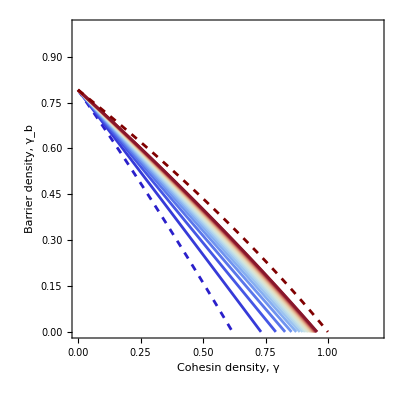

```mathematica
Show[Plot[Evaluate[Table[((-6-15 α-6 α^2-6 γo-12 α γo+√3 √(28+140 α+231 α^2+140 α^3+28 α^4+8 γo+28 α γo+12 α^2 γo-32 α^3 γo-16 α^4 γo-4 γo^2+12 α^2 γo^2-8 α^3 γo^2))/(2 (2+5 α+2 α^2))),{α,0,10,0.5}]],{γo,0,1.2},PlotRange->{0,1},Frame->True,FrameStyle->Directive[FSize,FontFamily->"CMU Serif",Black],PlotStyle->Table[Directive[ColorData[{"ThermometerColors","Reverse"}][1-α/10],If[α==0,Dashing[Small],Dashing[None]]],{α,0,10,0.5}],AspectRatio->1,FrameLabel->{{Style["Barrier density, γ_(<b>)"],None},{Style["Cohesin density, γ"],None}},FrameTicksStyle->Directive[FTicksSize,FontFamily->"CMU Serif",Black]],Plot[1/(2 (2+5 α+2 α^2))(-6-15 α-6 α^2-6 γo-12 α γo+√3 √(28+140 α+231 α^2+140 α^3+28 α^4+8 γo+28 α γo+12 α^2 γo-32 α^3 γo-16 α^4 γo-4 γo^2+12 α^2 γo^2-8 α^3 γo^2))/.α->1000,{γo,0,1},PlotRange->{0,1.2},PlotStyle->Directive[RGBColor[0.5,0,0],Dashed]]]
```

```mathematica
FullSimplify[Solve[p==0,γ]/.γo->0]
```

```mathematica
{{γ->-3/2-(√21 (2+α) (1+2 α))/(2 √((2+5 α+2 α^2)^2))},{γ->1/2 (-3+√21)}}
```

```mathematica
Solve[(-6-15 α-6 α^2-6 γo-12 α γo+√3 √(28+140 α+231 α^2+140 α^3+28 α^4+8 γo+28 α γo+12 α^2 γo-32 α^3 γo-16 α^4 γo-4 γo^2+12 α^2 γo^2-8 α^3 γo^2))/(2 (2+5 α+2 α^2))==0,γo]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{γo→1/2 (-1-2 α-√(5+12 α+4 α^2))},{γo→1/2 (-1-2 α+√(5+12 α+4 α^2))}}

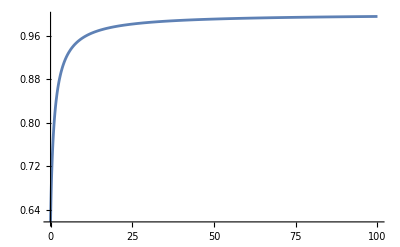

```mathematica
Plot[Solve[(-6-15 α-6 α^2-6 γo-12 α γo+√3 √(28+140 α+231 α^2+140 α^3+28 α^4+8 γo+28 α γo+12 α^2 γo-32 α^3 γo-16 α^4 γo-4 γo^2+12 α^2 γo^2-8 α^3 γo^2))/(2 (2+5 α+2 α^2)),{α,0,100},PlotRange->All]
```

```mathematica
Plot[1/2 (-1-2 α+√(5+12 α+4 α^2)),{α,0,100},PlotRange->All]
```

-Graphics-

```mathematica
Plot[]
```

```mathematica
Solve[]
```

```mathematica
1/2 (-3-3 γo-√3 √(7+2 γo-γo^2))/.
```

```mathematica
Simplify[(Simplify[A/.γ->0.2/.γo->0.2/.α->0.1])]
```

-0.0989457 ⅇ^(-4.39096 x)-0.325925 ⅇ^(-2.50428 x)+1.42487 ⅇ^(-1.23333 x)

```mathematica
Integrate[-0.09894572429430779 ⅇ^(-4.390957068328058 x)-0.32592474202693583 ⅇ^(-2.5042810269100384 x)+1.4248704663212433 ⅇ^(-1.2333333333333343 x),{x,0,Infinity}]
```

1.00262

```mathematica
Integrate[-0.6767806911856127 ⅇ^(-5.962509925842902 x)-1.894647880242959 ⅇ^(-3.7136805503475743 x)+3.5714285714285716 ⅇ^(-2.166666666666666 x),{x,0,Infinity}]
```

1.02467

```mathematica
ⅇ^(-x (1+γo)) (1+γo)^2-γo (2+γo)ⅇ^(-x (2+γo))
```

```mathematica
Series[ⅇ^(-x (1+γo)) (1+γo)^2-γo (2+γo)ⅇ^(-x (2+γo)) ,{γo,Infinity,1}]
```

ⅇ^(-x γo-2 x+O[1/γo]^3) (-γo^2-2 γo+O[1/γo]^2)+ⅇ^(-x γo-x+O[1/γo]^2) (γo^2+2 γo+1+O[1/γo]^2)

```mathematica
Manipulate[Plot[ⅇ^(-x (2+γo)) (ⅇ^x (1+γo)^2-γo (2+γo)),{x,0,10},PlotRange->All],{γo,1,10}]
```

Set::shape: Lists {System`SampledPlotsDump`labelprims$16263,System`SampledPlotsDump`imagepadding$16263,System`SampledPlotsDump`plotrangepadding$16263,System`SampledPlotsDump`plotrangeclipping$16263} and $Aborted[] are not the same shape.

```mathematica
Simplify[(ⅇ^(-1/6 x (7 γ+6 (5+γo))) (-ⅇ^(x+(x γ)/6) γ (4+γ+γo)^2-2 ⅇ^(3 x+(2 x γ)/3) (9+2 γ) γo (4+γ+2 γo)+ⅇ^(x (4+(5 γ)/6)) (4+γ) (3+γ+3 γo)^2))/((4+γ) (9+2 γ))]
```

0

```mathematica
Integrate[A,{x,0,Infinity}]
```

ConditionalExpression[(4 (2+α) (1+2 α)^2 (32 α^9 (9+2 γ) (24+2 γ^2+γ (14+3 γo))+16 α^8 (4 γ^4+γ^3 (98+20 γo)+216 (13+6 γo+γo^2)+γ^2 (772+298 γo+22 γo^2)+3 γ (826+407 γo+58 γo^2))+(4+γ)^2 (9+2 γ) (γ^3+γ^2 (11+6 γo)+γ (40+45 γo+11 γo^2)+6 (8+14 γo+7 γo^2+γo^3))+8 α^7 (4 γ^4 (5+2 γo)+γ^3 (442+294 γo+28 γo^2)+216 (53+65 γo+25 γo^2+4 γo^3)+γ^2 (3308+3054 γo+628 γo^2+26 γo^3)+3 γ (3434+3873 γo+1205 γo^2+120 γo^3))+α (14 γ^6+γ^5 (325+94 γo)+γ^4 (3135+1784 γo+260 γo^2)+2 γ^3 (8041+6743 γo+1941 γo^2+157 γo^3)+432 (104+164 γo+112 γo^2+31 γo^3+3 γo^4)+2 γ^2 (23132+25374 γo+10793 γo^2+1691 γo^3+66 γo^4)+12 γ (5896+7920 γo+4414 γo^2+987 γo^3+73 γo^4))-4 α^6 (16 γ^5-4 γ^4 (-73+6 γo+γo^2)-2 γ^3 (-931+395 γo+147 γo^2+6 γo^3)-2 γ^2 (-2344+4089 γo+2055 γo^2+265 γo^3+5 γo^4)-216 (19+197 γo+151 γo^2+50 γo^3+6 γo^4)-3 γ (-842+10799 γo+6839 γo^2+1589 γo^3+102 γo^4))+2 α^5 (16 γ^5 (-6+γo)+4 γ^4 (-481-4 γo+17 γo^2)+2 γ^3 (-7543-1294 γo+483 γo^2+65 γo^3)+2 γ^2 (-28937-8540 γo+2968 γo^2+1329 γo^3+77 γo^4)+216 (-370-108 γo+194 γo^2+157 γo^3+45 γo^4+4 γo^5)+3 γ (-36220-12572 γo+7728 γo^2+5439 γo^3+901 γo^4+31 γo^5))+α^2 (36 γ^6+γ^5 (810+238 γo)+8 γ^4 (944+517 γo+82 γo^2)+γ^3 (37334+28043 γo+8124 γo^2+988 γo^3)+γ^2 (103180+91996 γo+34591 γo^2+7188 γo^3+778 γo^4)-54 (-1696-1560 γo-364 γo^2+210 γo^3+117 γo^4+15 γo^5)+3 γ (50368+48044 γo+18416 γo^2+3363 γo^3+509 γo^4+76 γo^5))+α^3 (40 γ^6+28 γ^5 (29+9 γo)+γ^4 (6628+3480 γo+742 γo^2)+γ^3 (27436+15158 γo+6271 γo^2+1224 γo^3)+γ^2 (59044+10176 γo+3809 γo^2+5308 γo^3+1244 γo^4)+6 γ (9764-12920 γo-12885 γo^2-2874 γo^3+335 γo^4+117 γo^5)+108 (152-1256 γo-1462 γo^2-680 γo^3-127 γo^4-2 γo^5+γo^6))+α^4 (16 γ^6+8 γ^5 (19+16 γo)+γ^4 (-832+816 γo+436 γo^2)+2 γ^3 (-8414-3872 γo+1301 γo^2+413 γo^3)+2 γ^2 (-43114-43224 γo-5652 γo^2+2717 γo^3+423 γo^4)+3 γ (-63800-91464 γo-31646 γo^2+1095 γo^3+2115 γo^4+168 γo^5)+216 (-740-1334 γo-658 γo^2-62 γo^3+56 γo^4+16 γo^5+γo^6))))/((3+γ+2 α (3+γ)+3 γo) (12+4 α^3+3 γ+4 γo+2 α^2 (11+2 γ+γo)+α (34+8 γ+9 γo)-√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))) (12+4 α^3+3 γ+4 γo+2 α^2 (11+2 γ+γo)+α (34+8 γ+9 γo)+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))) (16 α^6 (9+2 γ)+(4+γ)^2 (9+2 γ)+8 α^5 (27 (2+γo)+4 γ (3+γo))+2 α (4 γ^3+108 (2+γo)+γ^2 (46+11 γo)+γ (174+73 γo))-4 α^4 (8 γ^2-27 (-1+4 γo+γo^2)-2 γ (-21+8 γo+γo^2))+α^2 (8 γ^3+4 γ^2 (15+4 γo)-27 (4+20 γo+5 γo^2)+γ (84-56 γo+38 γo^2))+2 α^3 (8 γ^2 (-4+γo)+4 γ (-62-3 γo+γo^2)+9 (-52-18 γo+6 γo^2+γo^3)))), ]

## Фит для CTCF - CTCF Loops (Fig 4e)

```mathematica
Aoos
```

```mathematica
lst=Import["C:\\петли\\ЭКСПЕРИМЕНТЫ\\chia-pet\\K562_rad21.txt","Table"];
```

```mathematica
model=Ai*A/.x->x/lp;
```

{{126.607,0.00354145},{154.069,0.00304111},{187.488,0.00208529},{228.156,0.001292},{277.646,0.000955532},{337.87,0.000564801},{411.158,0.000286778},{500.342,0.000176745},{608.871,0.0000586061},{740.942,0.0000230329},{901.66,0.0000172067}}

```mathematica
FindFit[lst[[10;;Length[lst]]],Am*Exp[-k*x],{{Am,0.001},{k,0.001}},x]
```

{Am→0.0114217,k→0.00903441}

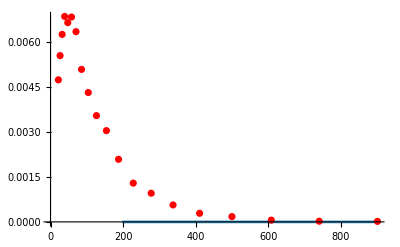

```mathematica
Show[ListPlot[lst,PlotStyle->Red],Plot[Am Exp[-k x]/.{Am->2.5300264137567883,k->0.9291143166956148},{x,21.63363493,901.65956}]]
```

```mathematica
posLeft=0.1+0.14;
posDown=2;
```

```mathematica
w=0.03;
```

```mathematica
FSize=20;
FTicksSize=15;
```

```mathematica
intN=Interpolation[lst];
```

```mathematica
tbls={};
For[γi=0,γi<=4,γi=γi+0.2,{
For[γoi=0,γoi<=4,γoi=γoi+0.2,{
For[αi=0,αi<=1,αi=αi+0.2,{
ft = FindFit[lst,model/.lp->400/.α->αi/.γ->γi/.γo->γoi,{{α,1.5},{γ,2},{γo,2},{Ai,0.003}},{x}];
f=(int[x]-(model/.lp->400/.α->αi/.γ->γi/.γo->γoi/.ft))^2;
rmse=NIntegrate[f,{x,1,800}];
AppendTo[tbls,{γi,γoi,αi, rmse}];
}];
}];
Print[γi]
}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. Ai ⅇ^(-0.0025 x) ComplexInfinity encountered.

FindFit::nrlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of real numbers with dimensions {20} at {α,γ,γo,Ai} = {1.5,2.,2.,0.003}.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. Ai ⅇ^(-0.0025 x) ComplexInfinity encountered.

ReplaceAll::reps: {FindFit[{{21.6336,0.0047332},{26.3262,0.00553962},{32.0366,0.00624717},{38.9857,0.00684484},{47.4421,0.00663854},{57.7328,0.00682577},{70.2556,0.00633784},{85.4948,0.00508111},{104.039,0.00430963},{126.607,0.00354145},{154.069,0.00304111},{187.488,0.00208529},{228.156,0.001292},{277.646,0.000955532},{337.87,0.000564801},{411.158,0.000286778},{500.342,0.000176745},{608.871,0.0000586061},{740.942,0.0000230329},{901.66,0.0000172067}},Indeterminate,{{α,1.5},{γ,2},{γo,2},{Ai,0.003}},{x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumri: The integrand (-(Indeterminate/.FindFit[«1»])+«1»)^2 has evaluated to Overflow, Indeterminate or Infinity for all sampling points in the region with boundaries {{1,21.6336}}.

ReplaceAll::reps: {FindFit[{{21.6336,0.0047332},{26.3262,0.00553962},{32.0366,0.00624717},{38.9857,0.00684484},{47.4421,0.00663854},{57.7328,0.00682577},{70.2556,0.00633784},{85.4948,0.00508111},{104.039,0.00430963},{126.607,0.00354145},{154.069,0.00304111},{187.488,0.00208529},{228.156,0.001292},{277.646,0.000955532},{337.87,0.000564801},{411.158,0.000286778},{500.342,0.000176745},{608.871,0.0000586061},{740.942,0.0000230329},{901.66,0.0000172067}},Indeterminate,{{α,1.5},{γ,2},{γo,2},{Ai,0.003}},{x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NIntegrate::inumri: The integrand (-(Indeterminate/.FindFit[«1»])+«1»)^2 has evaluated to Overflow, Indeterminate or Infinity for all sampling points in the region with boundaries {{1,21.6336}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

0

0.2

0.4

0.6

0.8

1.

1.2

1.4

1.6

1.8

2.

2.2

2.4

2.6

2.8

3.

3.2

3.4

3.6

3.8

4.

```mathematica
tblsN={{0,0,0,0.0020077997501810455},{0,0,0.2,0.0020077997501810455},{0,0,0.4,0.0020077997501810455},{0,0,0.6000000000000001,0.0020077997501810455},{0,0,0.8,0.0020077997501810455},{0,0,1.,0.0020173964019897603},{0,0.2,0,0.0020173964019897603},{0,0.2,0.2,0.0020031281012651463},{0,0.2,0.4,0.0019923660065526956},{0,0.2,0.6000000000000001,0.001984459630805268},{0,0.2,0.8,0.0019787021639090844},{0,0.2,1.,0.0019745382208119},{0,0.4,0,0.0019764928378731192},{0,0.4,0.2,0.0019639129119585898},{0,0.4,0.4,0.0019519470885384683},{0,0.4,0.6000000000000001,0.0019424345738567302},{0,0.4,0.8,0.0019353063203167238},{0,0.4,1.,0.0019301458198200967},{0,0.6000000000000001,0,0.0018960018158081307},{0,0.6000000000000001,0.2,0.0018972911396181844},{0,0.6000000000000001,0.4,0.001891613801875026},{0,0.6000000000000001,0.6000000000000001,0.001885468846766252},{0,0.6000000000000001,0.8,0.0018804452915096388},{0,0.6000000000000001,1.,0.0018768062532831232},{0,0.8,0,0.001788415371348393},{0,0.8,0.2,0.0018107548139826336},{0,0.8,0.4,0.001816374894515857},{0,0.8,0.6000000000000001,0.0018171219985015704},{0,0.8,0.8,0.0018167493439250305},{0,0.8,1.,0.0018165174575814512},{0,1.,0,0.0016646889887842558},{0,1.,0.2,0.0017110144883853466},{0,1.,0.4,0.001730714789260304},{0,1.,0.6000000000000001,0.001740567928995206},{0,1.,0.8,0.0017465556893230196},{0,1.,1.,0.001751051116957826},{0,1.2,0,0.0015333074404785322},{0,1.2,0.2,0.0016035784320862824},{0,1.2,0.4,0.001638411449993371},{0,1.2,0.6000000000000001,0.0016585168769575926},{0,1.2,0.8,0.0016718766125211862},{0,1.2,1.,0.001681941556328189},{0,1.4,0,0.0014003839611695533},{0,1.4,0.2,0.0014927239079398236},{0,1.4,0.4,0.0015425178742935032},{0,1.4,0.6000000000000001,0.001573211656749273},{0,1.4,0.8,0.001209836571361664},{0,1.4,1.,0.0016104929087448442},{0,1.5999999999999999,0,0.0012701134026954152},{0,1.5999999999999999,0.2,0.0013816449090094524},{0,1.5999999999999999,0.4,0.0014454264001513607},{0,1.5999999999999999,0.6000000000000001,0.0014864638531786518},{0,1.5999999999999999,0.8,0.0015155311259075275},{0,1.5999999999999999,1.,0.001537796631852808},{0,1.7999999999999998,0,0.0011452608024999653},{0,1.7999999999999998,0.2,0.001272653984206437},{0,1.7999999999999998,0.4,0.0013489658555332715},{0,1.7999999999999998,0.6000000000000001,0.0013997077778120017},{0,1.7999999999999998,0.8,0.001436390726992619},{0,1.7999999999999998,1.,0.0014647539990311844},{0,1.9999999999999998,0,0.001027570418106583},{0,1.9999999999999998,0.2,0.0011673784523764026},{0,1.9999999999999998,0.4,0.0012545037531957392},{0,1.9999999999999998,0.6000000000000001,0.0013140589205930424},{0,1.9999999999999998,0.8,0.0013578866836390904},{0,1.9999999999999998,1.,0.001392100106364792},{0,2.1999999999999997,0,0.0009180740011382534},{0,2.1999999999999997,0.2,0.0010669275260791866},{0,2.1999999999999997,0.4,0.0011630399531344766},{0,2.1999999999999997,0.6000000000000001,0.0012303696777745871},{0,2.1999999999999997,0.8,0.0012807315208456847},{0,2.1999999999999997,1.,0.0013204273029435362},{0,2.4,0,0.0008173115891462451},{0,2.4,0.2,0.0009720252898687524},{0,2.4,0.4,0.001075286535937454},{0,2.4,0.6000000000000001,0.0011492789569051396},{0,2.4,0.8,0.0012054780910100875},{0,2.4,1.,0.0012502068852190576},{0,2.6,0,0.000725485926663358},{0,2.6,0.2,0.0008831125197923566},{0,2.6,0.4,0.0009917330657424998},{0,2.6,0.6000000000000001,0.001071254515606347},{0,2.6,0.8,0.0011325478037325198},{0,2.6,1.,0.0011818085074988534},{0,2.8000000000000003,0,0.0006425695875737229},{0,2.8000000000000003,0.2,0.0008004229647192981},{0,2.8000000000000003,0.4,0.0009126985085951048},{0,2.8000000000000003,0.6000000000000001,0.0009966281217628442},{0,2.8000000000000003,0.8,0.001062254783604242},{0,2.8000000000000003,1.,0.0011155171432117468},{0,3.0000000000000004,0,0.0005683793601186761},{0,3.0000000000000004,0.2,0.0007240398478105385},{0,3.0000000000000004,0.4,0.000838371845098681},{0,3.0000000000000004,0.6000000000000001,0.0009256242193774488},{0,3.0000000000000004,0.8,0.0009948261722118224},{0,3.0000000000000004,1.,0.001051547657429012},{0,3.2000000000000006,0,0.0005026282075904875},{0,3.2000000000000006,0.2,0.0006539375267115392},{0,3.2000000000000006,0.4,0.0007688435150714733},{0,3.2000000000000006,0.6000000000000001,0.0008583830105325335},{0,3.2000000000000006,0.8,0.0009304189720134423},{0,3.2000000000000006,1.,0.0009900571732907458},{0,3.400000000000001,0,0.0004449618529821997},{0,3.400000000000001,0.2,0.0005900122085953115},{0,3.400000000000001,0.4,0.0007041296257695172},{0,3.400000000000001,0.6000000000000001,0.0007949788881261015},{0,3.400000000000001,0.8,0.0008691338940105921},{0,3.400000000000001,1.,0.0009311554709785558},{0,3.600000000000001,0,0.000394984736326313},{0,3.600000000000001,0.2,0.0005321046570738887},{0,3.600000000000001,0.4,0.0006441905431631735},{0,3.600000000000001,0.6000000000000001,0.0007354350788109517},{0,3.600000000000001,0.8,0.0008110266691528037},{0,3.600000000000001,1.,0.0008749136733968864},{0,3.800000000000001,0,0.00035227854035291045},{0,3.800000000000001,0.2,0.00048001704907512743},{0,3.800000000000001,0.4,0.0005889451663608866},{0,3.800000000000001,0.6000000000000001,0.0006797352401107301},{0,3.800000000000001,0.8,0.0007561172472435158},{0,3.800000000000001,1.,0.0008213714648834667},{0,4.000000000000001,0,0.00031641545026317154},{0,4.000000000000001,0.2,0.00043352554623090207},{0,4.000000000000001,0.4,0.0005382819012509406},{0,4.000000000000001,0.6000000000000001,0.0006278326323139585},{0,4.000000000000001,0.8,0.0007043972561850631},{0,4.000000000000001,1.,0.0007705430691201665},{0.2,0,0,0.0019745382208118975},{0.2,0,0.2,0.001974538220811898},{0.2,0,0.4,0.001974538220811897},{0.2,0,0.6000000000000001,0.001974538220811896},{0.2,0,0.8,0.0019745382208118958},{0.2,0,1.,0.001974538220811902},{0.2,0.2,0,0.0019617283239654767},{0.2,0.2,0.2,0.0019506767662469027},{0.2,0.2,0.4,0.0019425473028718858},{0.2,0.2,0.6000000000000001,0.0019368013717992513},{0.2,0.2,0.8,0.0019328271964616287},{0.2,0.2,1.,0.001930145819820097},{0.2,0.4,0,0.0019045268732651192},{0.2,0.4,0.2,0.0018969957867315333},{0.2,0.4,0.4,0.0018893728294665595},{0.2,0.4,0.6000000000000001,0.0018835002071094264},{0.2,0.4,0.8,0.0018794142471794876},{0.2,0.4,1.,0.0018768062532831227},{0.2,0.6000000000000001,0,0.0018141391832681342},{0.2,0.6000000000000001,0.2,0.0018206114767589368},{0.2,0.6000000000000001,0.4,0.0018199305827721899},{0.2,0.6000000000000001,0.6000000000000001,0.0018181812132511072},{0.2,0.6000000000000001,0.8,0.0018169324599139965},{0.2,0.6000000000000001,1.,0.0018165174575814507},{0.2,0.8,0,0.0017020025149258062},{0.2,0.8,0.2,0.0017283856196239024},{0.2,0.8,0.4,0.0017387795151115677},{0.2,0.8,0.6000000000000001,0.0017440569844440821},{0.2,0.8,0.8,0.0017477346511515631},{0.2,0.8,1.,0.0017510511169578275},{0.2,1.,0,0.0015776892432534009},{0.2,1.,0.2,0.0016262036432231576},{0.2,1.,0.4,0.0016498513917387876},{0.2,1.,0.6000000000000001,0.0016639021884552634},{0.2,1.,0.8,0.0016738552075519972},{0.2,1.,1.,0.0016819415563281868},{0.2,1.2,0,0.0014484380651120332},{0.2,1.2,0.2,0.001518774230076106},{0.2,1.2,0.4,0.0015563781905948565},{0.2,1.2,0.6000000000000001,0.0015800331663159898},{0.2,1.2,0.8,0.0015970100233522648},{0.2,1.2,1.,0.0016104929087448433},{0.2,1.4,0,0.0013193941127907047},{0.2,1.4,0.2,0.0014096934818824437},{0.2,1.4,0.4,0.0014609267129019657},{0.2,1.4,0.6000000000000001,0.0014943343441728577},{0.2,1.4,0.8,0.0015186180403825211},{0.2,1.4,1.,0.0015377966318528076},{0.2,1.5999999999999999,0,0.0011940558515935941},{0.2,1.5999999999999999,0.2,0.0013016148448070646},{0.2,1.5999999999999999,0.4,0.0013654817068874886},{0.2,1.5999999999999999,0.6000000000000001,0.0014083070348549973},{0.2,1.5999999999999999,0.8,0.0014398333045235654},{0.2,1.5999999999999999,1.,0.0014647539990311825},{0.2,1.7999999999999998,0,0.0010747089967851388},{0.2,1.7999999999999998,0.2,0.0011964400676625151},{0.2,1.7999999999999998,0.4,0.0012715432331197967},{0.2,1.7999999999999998,0.6000000000000001,0.0013231256570516371},{0.2,1.7999999999999998,0.8,0.0013615805383401449},{0.2,1.7999999999999998,1.,0.0013921001063647938},{0.2,1.9999999999999998,0,0.0009627765656708489},{0.2,1.9999999999999998,0.2,0.0010954928102192558},{0.2,1.9999999999999998,0.4,0.001180220397993497},{0.2,1.9999999999999998,0.6000000000000001,0.001239692953465547},{0.2,1.9999999999999998,0.8,0.0012845901125561566},{0.2,1.9999999999999998,1.,0.0013204273029435356},{0.2,2.1999999999999997,0,0.0008590788339003642},{0.2,2.1999999999999997,0.2,0.0009996619206814306},{0.2,2.1999999999999997,0.4,0.001092313576299886},{0.2,2.1999999999999997,0.6000000000000001,0.0011586900176116142},{0.2,2.1999999999999997,0.8,0.0012094302239833356},{0.2,2.1999999999999997,1.,0.0012502068852190556},{0.2,2.4,0,0.000764018776979653},{0.2,2.4,0.2,0.0009095136312025293},{0.2,2.4,0.4,0.0010083828189463696},{0.2,2.4,0.6000000000000001,0.0010806194928824609},{0.2,2.4,0.8,0.0011365353082976731},{0.2,2.4,1.,0.001181808507498855},{0.2,2.6,0,0.0006777120338877573},{0.2,2.6,0.2,0.0008253768215272247},{0.2,2.6,0.4,0.0009288029438713046},{0.2,2.6,0.6000000000000001,0.001005841741418151},{0.2,2.6,0.8,0.0010662304479507959},{0.2,2.6,1.,0.0011155171432117453},{0.2,2.8000000000000003,0,0.0006000775653541468},{0.2,2.8000000000000003,0.2,0.0007474067496083942},{0.2,2.8000000000000003,0.4,0.0008538070002735205},{0.2,2.8000000000000003,0.6000000000000001,0.0009346045081451835},{0.2,2.8000000000000003,0.8,0.000998751943382869},{0.2,2.8000000000000003,1.,0.0010515476574290104},{0.2,3.0000000000000004,0,0.000530901071811121},{0.2,3.0000000000000004,0.2,0.0006756323066289675},{0.2,3.0000000000000004,0.4,0.0007835201245518088},{0.2,3.0000000000000004,0.6000000000000001,0.000867066912362418},{0.2,3.0000000000000004,0.8,0.0009342644179139043},{0.2,3.0000000000000004,1.,0.0009900571732907454},{0.2,3.2000000000000006,0,0.00046987964737400274},{0.2,3.2000000000000006,0.2,0.0006099909721649123},{0.2,3.2000000000000006,0.4,0.0007179857157934256},{0.2,3.2000000000000006,0.6000000000000001,0.0008033186708560084},{0.2,3.2000000000000006,0.8,0.0008728749042266773},{0.2,3.2000000000000006,1.,0.0009311554709785548},{0.2,3.400000000000001,0,0.00041665346239419727},{0.2,3.400000000000001,0.2,0.0005503547029326667},{0.2,3.400000000000001,0.4,0.0006571855976206507},{0.2,3.400000000000001,0.6000000000000001,0.0007433954074017896},{0.2,3.400000000000001,0.8,0.0008146443665145245},{0.2,3.400000000000001,1.,0.0008749136733968863},{0.2,3.600000000000001,0,0.0003708283960161583},{0.2,3.600000000000001,0.2,0.0004965491710165283},{0.2,3.600000000000001,0.4,0.0006010555304699983},{0.2,3.600000000000001,0.6000000000000001,0.0006872908012303113},{0.2,3.600000000000001,0.8,0.0007595970809619812},{0.2,3.600000000000001,1.,0.0008213714648834668},{0.2,3.800000000000001,0,0.0003319922784366782},{0.2,3.800000000000001,0.2,0.0004483681213167005},{0.2,3.800000000000001,0.4,0.000549497154153737},{0.2,3.800000000000001,0.6000000000000001,0.0006349662092289204},{0.2,3.800000000000001,0.8,0.0007077282488931088},{0.2,3.800000000000001,1.,0.0007705430691201659},{0.2,4.000000000000001,0,0.000299726562889145},{0.2,4.000000000000001,0.2,0.00040558413221062066},{0.2,4.000000000000001,0.4,0.0005023871980272752},{0.2,4.000000000000001,0.6000000000000001,0.0005863582827528462},{0.2,4.000000000000001,0.8,0.0006590101636876445},{0.2,4.000000000000001,1.,0.0007224221868713592},{0.4,0,0,0.0019301458198200964},{0.4,0,0.2,0.0019301458198200964},{0.4,0,0.4,0.0019301458198200964},{0.4,0,0.6000000000000001,0.0019301458198200967},{0.4,0,0.8,0.001930145819820097},{0.4,0,1.,0.0019301458198200995},{0.4,0.2,0,0.0018984366794112175},{0.4,0.2,0.2,0.0018902561040093939},{0.4,0.2,0.4,0.0018844624201507542},{0.4,0.2,0.6000000000000001,0.001880618234968141},{0.4,0.2,0.8,0.0018782017682073455},{0.4,0.2,1.,0.001876806253283126},{0.4,0.4,0,0.001828356305788843},{0.4,0.4,0.2,0.0018251148774016891},{0.4,0.4,0.4,0.0018212070224659248},{0.4,0.4,0.6000000000000001,0.0018184472019562468},{0.4,0.4,0.8,0.001816956092667356},{0.4,0.4,1.,0.0018165174575814477},{0.4,0.6000000000000001,0,0.0017308172579588027},{0.4,0.6000000000000001,0.2,0.0017414932499859861},{0.4,0.6000000000000001,0.4,0.0017449543704341466},{0.4,0.6000000000000001,0.6000000000000001,0.001746871560158799},{0.4,0.6000000000000001,0.8,0.0017487756169586922},{0.4,0.6000000000000001,1.,0.001751051116957828},{0.4,0.8,0,0.001616099568659046},{0.4,0.8,0.2,0.0016455399165622973},{0.4,0.8,0.4,0.0016597592530611816},{0.4,0.8,0.6000000000000001,0.001668723460668355},{0.4,0.8,0.8,0.0016757159013446907},{0.4,0.8,1.,0.0016819415563281868},{0.4,1.,0,0.0014925021793170165},{0.4,1.,0.2,0.0015423564506449195},{0.4,1.,0.4,0.0015690196344828866},{0.4,1.,0.6000000000000001,0.0015863894892275128},{0.4,1.,0.8,0.0015995168379094842},{0.4,1.,1.,0.0016104929087448435},{0.4,1.2,0,0.00136618225888685},{0.4,1.2,0.2,0.001435941428812571},{0.4,1.2,0.4,0.0014754741131239174},{0.4,1.2,0.6000000000000001,0.001501825912383823},{0.4,1.2,0.8,0.0015216214907029994},{0.4,1.2,1.,0.0015377966318528063},{0.4,1.4,0,0.0012414672826295862},{0.4,1.4,0.2,0.001329306463337737},{0.4,1.4,0.4,0.001381266082810839},{0.4,1.4,0.6000000000000001,0.0014166013595351044},{0.4,1.4,0.8,0.0014432066064166995},{0.4,1.4,1.,0.0014647539990311823},{0.4,1.5999999999999999,0,0.0011212753460644812},{0.4,1.5999999999999999,0.2,0.00122465005207219},{0.4,1.5999999999999999,0.4,0.0012880332507513893},{0.4,1.5999999999999999,0.6000000000000001,0.0013319501754663313},{0.4,1.5999999999999999,0.8,0.0013652174111856768},{0.4,1.5999999999999999,1.,0.001392100106364793},{0.4,1.7999999999999998,0,0.0010074951184063656},{0.4,1.7999999999999998,0.2,0.0011235320150002987},{0.4,1.7999999999999998,0.4,0.0011969997342543238},{0.4,1.7999999999999998,0.6000000000000001,0.0012488267343257302},{0.4,1.7999999999999998,0.8,0.0012884022940888046},{0.4,1.7999999999999998,1.,0.0013204273029435354},{0.4,1.9999999999999998,0,0.000901284143427233},{0.4,1.9999999999999998,0.2,0.001027024833585993},{0.4,1.9999999999999998,0.4,0.0011090597521138193},{0.4,1.9999999999999998,0.6000000000000001,0.0011679556574246699},{0.4,1.9999999999999998,0.8,0.0012133449882661955},{0.4,1.9999999999999998,1.,0.001250206885219059},{0.4,2.1999999999999997,0,0.0008032881273046454},{0.4,2.1999999999999997,0.2,0.0009358356950853019},{0.4,2.1999999999999997,0.4,0.001024848785764045},{0.4,2.1999999999999997,0.6000000000000001,0.0010898757479264338},{0.4,2.1999999999999997,0.8,0.0011404931468057802},{0.4,2.1999999999999997,1.,0.0011818085074988553},{0.4,2.4,0,0.0007137971443550138},{0.4,2.4,0.2,0.00085040096540244},{0.4,2.4,0.4,0.0009448017216011302},{0.4,2.4,0.6000000000000001,0.0010149771094556373},{0.4,2.4,0.8,0.001070182989746896},{0.4,2.4,1.,0.0011155171432117468},{0.4,2.6,0,0.0006328554980126323},{0.4,2.6,0.2,0.0007709576385486372},{0.4,2.6,0.4,0.0008691991827067912},{0.4,2.6,0.6000000000000001,0.0009435317880687713},{0.4,2.6,0.8,0.0010026601391331575},{0.4,2.6,1.,0.0010515476574290113},{0.4,2.8000000000000003,0,0.0005603388405567197},{0.4,2.8000000000000003,0.2,0.0006975967097281396},{0.4,2.8000000000000003,0.4,0.0007982038725588137},{0.4,2.8000000000000003,0.6000000000000001,0.0008757186745674202},{0.4,2.8000000000000003,0.8,0.0009380969830356815},{0.4,2.8000000000000003,1.,0.0009900571732907454},{0.4,3.0000000000000004,0,0.0004960085310901721},{0.4,3.0000000000000004,0.2,0.0006303028351510574},{0.4,3.0000000000000004,0.4,0.0007318888135094435},{0.4,3.0000000000000004,0.6000000000000001,0.000811643529771843},{0.4,3.0000000000000004,0.8,0.0008766070010002281},{0.4,3.0000000000000004,1.,0.0009311554709785553},{0.4,3.2000000000000006,0,0.0004395502097377398},{0.4,3.2000000000000006,0.2,0.000568983782325711},{0.4,3.2000000000000006,0.4,0.0006702591735604613},{0.4,3.2000000000000006,0.6000000000000001,0.0007513549767490761},{0.4,3.2000000000000006,0.8,0.0008182564981903954},{0.4,3.2000000000000006,1.,0.0008749136733968863},{0.4,3.400000000000001,0,0.0003906013659876306},{0.4,3.400000000000001,0.2,0.0005134923470682102},{0.4,3.400000000000001,0.4,0.0006132691005216152},{0.4,3.400000000000001,0.6000000000000001,0.0006948572176443118},{0.4,3.400000000000001,0.8,0.0007630741692080595},{0.4,3.400000000000001,1.,0.0008213714648834673},{0.4,3.600000000000001,0,0.0003487711554495134},{0.4,3.600000000000001,0.2,0.00046364272487549107},{0.4,3.600000000000001,0.4,0.0005608347043738498},{0.4,3.600000000000001,0.6000000000000001,0.0006421201222583854},{0.4,3.600000000000001,0.8,0.000711058867070401},{0.4,3.600000000000001,1.,0.0007705430691201675},{0.4,3.800000000000001,0,0.00031365469127499196},{0.4,3.800000000000001,0.2,0.0004192227909875144},{0.4,3.800000000000001,0.4,0.0005128440817475154},{0.4,3.800000000000001,0.6000000000000001,0.0005930872240213935},{0.4,3.800000000000001,0.8,0.0006621859009940909},{0.4,3.800000000000001,1.,0.0007224221868713582},{0.4,4.000000000000001,0,0.0002848433488600233},{0.4,4.000000000000001,0.2,0.0003800033464880511},{0.4,4.000000000000001,0.4,0.00046916507189453764},{0.4,4.000000000000001,0.6000000000000001,0.0005476820576141424},{0.4,4.000000000000001,0.8,0.0006164121356178442},{0.4,4.000000000000001,1.,0.0006769860673821992},{0.6000000000000001,0,0,0.0018768062532831232},{0.6000000000000001,0,0.2,0.0018768062532831238},{0.6000000000000001,0,0.4,0.0018768062532831232},{0.6000000000000001,0,0.6000000000000001,0.0018768062532831227},{0.6000000000000001,0,0.8,0.0018768062532831232},{0.6000000000000001,0,1.,0.0018768062532831253},{0.6000000000000001,0.2,0,0.001829524376893545},{0.6000000000000001,0.2,0.2,0.0018238593624964293},{0.6000000000000001,0.2,0.4,0.001820099950428608},{0.6000000000000001,0.2,0.6000000000000001,0.0018178991254417848},{0.6000000000000001,0.2,0.8,0.0018168183677451123},{0.6000000000000001,0.2,1.,0.001816517457581451},{0.6000000000000001,0.4,0,0.001749550265182068},{0.6000000000000001,0.4,0.2,0.001749903178046328},{0.6000000000000001,0.4,0.4,0.0017491276370700233},{0.6000000000000001,0.4,0.6000000000000001,0.0017489895998380994},{0.6000000000000001,0.4,0.8,0.00174967663240773},{0.6000000000000001,0.4,1.,0.0017510511169578267},{0.6000000000000001,0.6000000000000001,0,0.001647151328120667},{0.6000000000000001,0.6000000000000001,0.2,0.0016611809020236719},{0.6000000000000001,0.6000000000000001,0.4,0.0016680274227016873},{0.6000000000000001,0.6000000000000001,0.6000000000000001,0.0016729591956118014},{0.6000000000000001,0.6000000000000001,0.8,0.0016774567815832466},{0.6000000000000001,0.6000000000000001,1.,0.00168194155632819},{0.6000000000000001,0.8,0,0.0015314458237596835},{0.6000000000000001,0.8,0.2,0.0015631152195147023},{0.6000000000000001,0.8,0.4,0.0015803444062327822},{0.6000000000000001,0.8,0.6000000000000001,0.0015922606563943226},{0.6000000000000001,0.8,0.8,0.0016019221857986703},{0.6000000000000001,0.8,1.,0.0016104929087448446},{0.6000000000000001,1.,0,0.0014095891481652964},{0.6000000000000001,1.,0.2,0.0014600895262438386},{0.6000000000000001,1.,0.4,0.0014889827581289314},{0.6000000000000001,1.,0.6000000000000001,0.0015089205644841024},{0.6000000000000001,1.,0.8,0.0015245398277182142},{0.6000000000000001,1.,1.,0.001537796631852808},{0.6000000000000001,1.2,0,0.001286808820325016},{0.6000000000000001,1.2,0.2,0.0013554822662449183},{0.6000000000000001,1.2,0.4,0.0013962452469746234},{0.6000000000000001,1.2,0.6000000000000001,0.0014245748591815747},{0.6000000000000001,1.2,0.8,0.001446509147573378},{0.6000000000000001,1.2,1.,0.0014647539990311847},{0.6000000000000001,1.4,0,0.0011667439628065628},{0.6000000000000001,1.4,0.2,0.001251807676035451},{0.6000000000000001,1.4,0.4,0.0013039113180645327},{0.6000000000000001,1.4,0.6000000000000001,0.0013405186238243053},{0.6000000000000001,1.4,0.8,0.001368795981242128},{0.6000000000000001,1.4,1.,0.0013921001063647933},{0.6000000000000001,1.5999999999999999,0,0.0010518289145304235},{0.6000000000000001,1.5999999999999999,0.2,0.001150882799663735},{0.6000000000000001,1.5999999999999999,0.4,0.0012133254434359645},{0.6000000000000001,1.5999999999999999,0.6000000000000001,0.0012577590529708003},{0.6000000000000001,1.5999999999999999,0.8,0.0012921669006312568},{0.6000000000000001,1.5999999999999999,1.,0.001320427302943535},{0.6000000000000001,1.7999999999999998,0,0.0009436227796475575},{0.6000000000000001,1.7999999999999998,0.2,0.0010539831742576973},{0.6000000000000001,1.7999999999999998,0.4,0.0011254811401064644},{0.6000000000000001,1.7999999999999998,0.6000000000000001,0.0011770655965282135},{0.6000000000000001,1.7999999999999998,0.8,0.0012172213628541201},{0.6000000000000001,1.7999999999999998,1.,0.0012502068852190589},{0.6000000000000001,1.9999999999999998,0,0.0008430630683950205},{0.6000000000000001,1.9999999999999998,0.2,0.000961973419755877},{0.6000000000000001,1.9999999999999998,0.4,0.0010410943329446736},{0.6000000000000001,1.9999999999999998,0.6000000000000001,0.0010990144826905819},{0.6000000000000001,1.9999999999999998,0.8,0.001144420427963768},{0.6000000000000001,1.9999999999999998,1.,0.0011818085074988551},{0.6000000000000001,2.1999999999999997,0,0.0007506509456502696},{0.6000000000000001,2.1999999999999997,0.2,0.0008754107761770113},{0.6000000000000001,2.1999999999999997,0.4,0.000960664334135834},{0.6000000000000001,2.1999999999999997,0.6000000000000001,0.0010240267127156828},{0.6000000000000001,2.1999999999999997,0.8,0.0010741116330536644},{0.6000000000000001,2.1999999999999997,1.,0.001115517143211747},{0.6000000000000001,2.4,0,0.0006665832708888549},{0.6000000000000001,2.4,0.2,0.0007946246063251349},{0.6000000000000001,2.4,0.4,0.000884523007418477},{0.6000000000000001,2.4,0.6000000000000001,0.0009523996515071969},{0.6000000000000001,2.4,0.8,0.0010065500851367485},{0.6000000000000001,2.4,1.,0.0010515476574290104},{0.6000000000000001,2.6,0,0.0005908458965624712},{0.6000000000000001,2.6,0.2,0.0007197763623198806},{0.6000000000000001,2.6,0.4,0.000812873650379773},{0.6000000000000001,2.6,0.6000000000000001,0.0008843328363757193},{0.6000000000000001,2.6,0.8,0.0009419160819985308},{0.6000000000000001,2.6,1.,0.000990057173290745},{0.6000000000000001,2.8000000000000003,0,0.000523279607611365},{0.6000000000000001,2.8000000000000003,0.2,0.0006509044151634579},{0.6000000000000001,2.8000000000000003,0.4,0.0007458213803347643},{0.6000000000000001,2.8000000000000003,0.6000000000000001,0.0008199488132287608},{0.6000000000000001,2.8000000000000003,0.8,0.0008803296764981812},{0.6000000000000001,2.8000000000000003,1.,0.0009311554709785554},{0.6000000000000001,3.0000000000000004,0,0.000463626954157243},{0.6000000000000001,3.0000000000000004,0.2,0.0005879574653439783},{0.6000000000000001,3.0000000000000004,0.4,0.0006833967168152043},{0.6000000000000001,3.0000000000000004,0.6000000000000001,0.0007593098261230037},{0.6000000000000001,3.0000000000000004,0.8,0.0008218626238005949},{0.6000000000000001,3.0000000000000004,1.,0.0008749136733968866},{0.6000000000000001,3.2000000000000006,0,0.0004115657358821588},{0.6000000000000001,3.2000000000000006,0.2,0.0005308194595083008},{0.6000000000000001,3.2000000000000006,0.4,0.0006255738219284499},{0.6000000000000001,3.2000000000000006,0.6000000000000001,0.0007024311187924068},{0.6000000000000001,3.2000000000000006,0.8,0.0007665481302115252},{0.6000000000000001,3.2000000000000006,1.,0.0008213714648834674},{0.6000000000000001,3.400000000000001,0,0.0003667330954569438},{0.6000000000000001,3.400000000000001,0.2,0.0004793282255416461},{0.6000000000000001,3.400000000000001,0.4,0.0005722845954060673},{0.6000000000000001,3.400000000000001,0.6000000000000001,0.0006492915054712432},{0.6000000000000001,3.400000000000001,0.8,0.0007143887798620692},{0.6000000000000001,3.400000000000001,1.,0.0007705430691201662},{0.6000000000000001,3.600000000000001,0,0.00032874293563933346},{0.6000000000000001,3.600000000000001,0.2,0.0004332894632316418},{0.6000000000000001,3.600000000000001,0.4,0.0005234295738931596},{0.6000000000000001,3.600000000000001,0.6000000000000001,0.0005998417603954665},{0.6000000000000001,3.600000000000001,0.8,0.0006653629652262958},{0.6000000000000001,3.600000000000001,1.,0.0007224221868713586},{0.6000000000000001,3.800000000000001,0,0.0002971985341283476},{0.6000000000000001,3.800000000000001,0.2,0.0003924872889078838},{0.6000000000000001,3.800000000000001,0.4,0.0004788863730713182},{0.6000000000000001,3.800000000000001,0.6000000000000001,0.0005540112744530445},{0.6000000000000001,3.800000000000001,0.8,0.0006194300970873197},{0.6000000000000001,3.800000000000001,1.,0.0006769860673821996},{0.6000000000000001,4.000000000000001,0,0.00027170166449955614},{0.6000000000000001,4.000000000000001,0.2,0.0003566922081056173},{0.6000000000000001,4.000000000000001,0.4,0.0004385162402334842},{0.6000000000000001,4.000000000000001,0.6000000000000001,0.0005117133393480639},{0.6000000000000001,4.000000000000001,0.8,0.0005765348230663382},{0.6000000000000001,4.000000000000001,1.,0.000634198861565059},{0.8,0,0,0.0018165174575814516},{0.8,0,0.2,0.0018165174575814538},{0.8,0,0.4,0.0018165174575814527},{0.8,0,0.6000000000000001,0.0018165174575814518},{0.8,0,0.8,0.0018165174575814516},{0.8,0,1.,0.0018165174575814488},{0.8,0.2,0,0.0017567025860710447},{0.8,0.2,0.2,0.0017532080850641242},{0.8,0.2,0.4,0.0017511928215001922},{0.8,0.2,0.6000000000000001,0.0017503896694118135},{0.8,0.2,0.8,0.0017504357670399164},{0.8,0.2,1.,0.0017510511169578288},{0.8,0.4,0,0.0016693947265015796},{0.8,0.4,0.2,0.0016727194500655116},{0.8,0.4,0.4,0.001674549242772585},{0.8,0.4,0.6000000000000001,0.001676588075633056},{0.8,0.4,0.8,0.0016790759444279331},{0.8,0.4,1.,0.0016819415563281907},{0.8,0.6000000000000001,0,0.0015640276645263085},{0.8,0.6000000000000001,0.2,0.0015806814121645787},{0.8,0.6000000000000001,0.4,0.0015902533178078994},{0.8,0.6000000000000001,0.6000000000000001,0.0015976266135349388},{0.8,0.6000000000000001,0.8,0.0016042242665821108},{0.8,0.6000000000000001,1.,0.0016104929087448448},{0.8,0.8,0,0.0014486119981160768},{0.8,0.8,0.2,0.0014818201245668339},{0.8,0.8,0.4,0.001501364294122958},{0.8,0.8,0.6000000000000001,0.0015156000755074312},{0.8,0.8,0.8,0.0015273713950001},{0.8,0.8,1.,0.0015377966318528063},{0.8,1.,0,0.001329293716131722},{0.8,1.,0.2,0.001379876881251142},{0.8,1.,0.4,0.0014103425525937414},{0.8,1.,0.6000000000000001,0.0014322113399390965},{0.8,1.,0.8,0.0014497394323872734},{0.8,1.,1.,0.0014647539990311842},{0.8,1.2,0,0.0012105064602606346},{0.8,1.2,0.2,0.001277694973969754},{0.8,1.2,0.4,0.001319112037554508},{0.8,1.2,0.6000000000000001,0.0013488168267838043},{0.8,1.2,0.8,0.001372314915609391},{0.8,1.2,1.,0.0013921001063647933},{0.8,1.4,0,0.001095310793888577},{0.8,1.4,0.2,0.0011773678302537229},{0.8,1.4,0.4,0.0012291422994138287},{0.8,1.4,0.6000000000000001,0.001266477624146835},{0.8,1.4,0.8,0.0012958827550713264},{0.8,1.4,1.,0.0013204273029435362},{0.8,1.5999999999999999,0,0.0009857374015253555},{0.8,1.5999999999999999,0.2,0.0010803934018167362},{0.8,1.5999999999999999,0.4,0.0011415313951821107},{0.8,1.5999999999999999,0.6000000000000001,0.0011860092574977872},{0.8,1.5999999999999999,0.8,0.0012210583147899098},{0.8,1.5999999999999999,1.,0.0012502068852190578},{0.8,1.7999999999999998,0,0.0008830711499392039},{0.8,1.7999999999999998,0.2,0.0009878109309024484},{0.8,1.7999999999999998,0.4,0.0010570807106396688},{0.8,1.7999999999999998,0.6000000000000001,0.0011080266286081035},{0.8,1.7999999999999998,0.8,0.0011483162492549016},{0.8,1.7999999999999998,1.,0.0011818085074988556},{0.8,1.9999999999999998,0,0.0007880666188053309},{0.8,1.9999999999999998,0.2,0.0009003128643322465},{0.8,1.9999999999999998,0.4,0.000976358448893902},{0.8,1.9999999999999998,0.6000000000000001,0.0010329827966785174},{0.8,1.9999999999999998,0.8,0.0010780155916247033},{0.8,1.9999999999999998,1.,0.0011155171432117468},{0.8,2.1999999999999997,0,0.0007011049508112687},{0.8,2.1999999999999997,0.2,0.0008183324937255928},{0.8,2.1999999999999997,0.4,0.0008997515279115995},{0.8,2.1999999999999997,0.6000000000000001,0.0009612014780043749},{0.8,2.1999999999999997,0.8,0.001010421097740781},{0.8,2.1999999999999997,1.,0.0010515476574290113},{0.8,2.4,0,0.0006223059012682371},{0.8,2.4,0.2,0.0007421108934838285},{0.8,2.4,0.4,0.0008275070183010228},{0.8,2.4,0.6000000000000001,0.0008929037507454786},{0.8,2.4,0.8,0.0009457211210662735},{0.8,2.4,1.,0.0009900571732907463},{0.8,2.6,0,0.000551607447090888},{0.8,2.6,0.2,0.0006717473615907311},{0.8,2.6,0.4,0.0007597647447993615},{0.8,2.6,0.6000000000000001,0.0008282297072538898},{0.8,2.6,0.8,0.0008840424154509497},{0.8,2.6,1.,0.0009311554709785558},{0.8,2.8000000000000003,0,0.0004888224500074581},{0.8,2.8000000000000003,0.2,0.0006072371975484802},{0.8,2.8000000000000003,0.4,0.0006965827088972555},{0.8,2.8000000000000003,0.6000000000000001,0.000767255853656334},{0.8,2.8000000000000003,0.8,0.0008254622963754078},{0.8,2.8000000000000003,1.,0.0008749136733968858},{0.8,3.0000000000000004,0,0.0004336792033296568},{0.8,3.0000000000000004,0.2,0.000548499958950677},{0.8,3.0000000000000004,0.4,0.0006379568184963022},{0.8,3.0000000000000004,0.6000000000000001,0.0007100090115122403},{0.8,3.0000000000000004,0.8,0.0007700185763777489},{0.8,3.0000000000000004,1.,0.0008213714648834671},{0.8,3.2000000000000006,0,0.0003858506292469226},{0.8,3.2000000000000006,0.2,0.0004954006310100658},{0.8,3.2000000000000006,0.4,0.0005838361697502793},{0.8,3.2000000000000006,0.6000000000000001,0.0006564773864334964},{0.8,3.2000000000000006,0.8,0.0007177176512727454},{0.8,3.2000000000000006,1.,0.0007705430691201681},{0.8,3.400000000000001,0,0.00034497541918123494},{0.8,3.400000000000001,0.2,0.00044776553779538877},{0.8,3.400000000000001,0.4,0.0005341348838608207},{0.8,3.400000000000001,0.6000000000000001,0.0006066193654774182},{0.8,3.400000000000001,0.8,0.0006685410652453517},{0.8,3.400000000000001,1.,0.0007224221868713593},{0.8,3.600000000000001,0,0.0003106733937121806},{0.8,3.600000000000001,0.2,0.0004053943462555059},{0.8,3.600000000000001,0.4,0.0004887412867916599},{0.8,3.600000000000001,0.6000000000000001,0.0005603705054587987},{0.8,3.600000000000001,0.8,0.0006224508332909358},{0.8,3.600000000000001,1.,0.0006769860673821995},{0.8,3.800000000000001,0,0.0002825566686358552},{0.8,3.800000000000001,0.2,0.00036806915372885636},{0.8,3.800000000000001,0.4,0.0004475250417296288},{0.8,3.800000000000001,0.6000000000000001,0.0005176490856043844},{0.8,3.800000000000001,0.8,0.0005793937531624986},{0.8,3.800000000000001,1.,0.000634198861565059},{0.8,4.000000000000001,0,0.0002602377459231793},{0.8,4.000000000000001,0.2,0.00033556138446512923},{0.8,4.000000000000001,0.4,0.00041034270207945247},{0.8,4.000000000000001,0.6000000000000001,0.00047836052269957757},{0.8,4.000000000000001,0.8,0.0005393048979483026},{0.8,4.000000000000001,1.,0.0005940143816848366},{1.,0,0,0.0017510511169578262},{1.,0,0.2,0.0017510511169578275},{1.,0,0.4,0.0017510511169578273},{1.,0,0.6000000000000001,0.0017510511169578267},{1.,0,0.8,0.001751051116957828},{1.,0,1.,0.001751051116957826},{1.,0.2,0,0.0016814077022731437},{1.,0.2,0.2,0.0016797610421606921},{1.,0.2,0.4,0.001679220558510704},{1.,0.2,0.6000000000000001,0.0016795890706396872},{1.,0.2,0.8,0.001680571496396424},{1.,0.2,1.,0.001681941556328191},{1.,0.4,0,0.001588930630826611},{1.,0.4,0.2,0.001594679069624796},{1.,0.4,0.4,0.001598646710172799},{1.,0.4,0.6000000000000001,0.001602467290064859},{1.,0.4,0.8,0.0016064212797358057},{1.,0.4,1.,0.0016104929087448429},{1.,0.6000000000000001,0,0.001482142487010134},{1.,0.6000000000000001,0.2,0.0015008002701368867},{1.,0.6000000000000001,0.4,0.0015125283601646127},{1.,0.6000000000000001,0.6000000000000001,0.0015218460310159716},{1.,0.6000000000000001,0.8,0.0015301145296820313},{1.,0.6000000000000001,1.,0.0015377966318528063},{1.,0.8,0,0.0013680321683692744},{1.,0.8,0.2,0.0014022071744185093},{1.,0.8,0.4,0.0014234786894299425},{1.,0.8,0.6000000000000001,0.0014394943309753655},{1.,0.8,0.8,0.0014528959552720716},{1.,0.8,1.,0.0014647539990311825},{1.,1.,0,0.0012518652737453528},{1.,1.,0.2,0.0013020767326242556},{1.,1.,0.4,0.0013335671971437357},{1.,1.,0.6000000000000001,0.001356830298213475},{1.,1.,0.8,0.0013757728697336873},{1.,1.,1.,0.0013921001063647936},{1.,1.2,0,0.0011374003703675459},{1.,1.2,0.2,0.0012027942996772993},{1.,1.2,0.4,0.0012443923782139473},{1.,1.2,0.6000000000000001,0.0012749698499520492},{1.,1.2,0.8,0.0012995486681651454},{1.,1.2,1.,0.0013204273029435343},{1.,1.4,0,0.0010272119254276751},{1.,1.4,0.2,0.0011060986460056906},{1.,1.4,0.4,0.0011571617161518707},{1.,1.4,0.6000000000000001,0.0011947757661205402},{1.,1.4,0.8,0.001224854799236924},{1.,1.4,1.,0.0012502068852190587},{1.,1.5999999999999999,0,0.000922993223631051},{1.,1.5999999999999999,0.2,0.0010132211151732827},{1.,1.5999999999999999,0.4,0.0010727669982213371},{1.,1.5999999999999999,0.6000000000000001,0.001116902844910961},{1.,1.5999999999999999,0.8,0.0011521796969517504},{1.,1.5999999999999999,1.,0.0011818085074988547},{1.,1.7999999999999998,0,0.0008258002963616417},{1.,1.7999999999999998,0.2,0.0009250044663120658},{1.,1.7999999999999998,0.4,0.000991849847850119},{1.,1.7999999999999998,0.6000000000000001,0.0010418373624833724},{1.,1.7999999999999998,0.8,0.0010818940688825135},{1.,1.7999999999999998,1.,0.0011155171432117466},{1.,1.9999999999999998,0,0.0007362351739747166},{1.,1.9999999999999998,0.2,0.0008419983602592456},{1.,1.9999999999999998,0.4,0.0009148561765257617},{1.,1.9999999999999998,0.6000000000000001,0.0009699304307484578},{1.,1.9999999999999998,0.8,0.0010142724839211665},{1.,1.9999999999999998,1.,0.0010515476574290113},{1.,2.1999999999999997,0,0.0006545790777141511},{1.,2.1999999999999997,0.2,0.0007645334813289333},{1.,2.1999999999999997,0.4,0.0008420801502921889},{1.,2.1999999999999997,0.6000000000000001,0.0009014255807008101},{1.,2.1999999999999997,0.8,0.0009495114980920789},{1.,2.1999999999999997,1.,0.0009900571732907458},{1.,2.4,0,0.0005808879030646237},{1.,2.4,0.2,0.0006927779722123782},{1.,2.4,0.4,0.0007736990529337833},{1.,2.4,0.6000000000000001,0.0008364812320036412},{1.,2.4,0.8,0.0008877446950938537},{1.,2.4,1.,0.0009311554709785559},{1.,2.6,0,0.0005150604710172974},{1.,2.6,0.2,0.0006267799778050619},{1.,2.6,0.4,0.0007098006233440778},{1.,2.6,0.6000000000000001,0.0007751888130475851},{1.,2.6,0.8,0.0008290550622967831},{1.,2.6,1.,0.0008749136733968864},{1.,2.8000000000000003,0,0.00045688745575084245},{1.,2.8000000000000003,0.2,0.0005664995940673315},{1.,2.8000000000000003,0.4,0.0006504043544259382},{1.,2.8000000000000003,0.6000000000000001,0.0007175872770424353},{1.,2.8000000000000003,0.8,0.0007734851142318004},{1.,2.8000000000000003,1.,0.000821371464883468},{1.,3.0000000000000004,0,0.0004060866505212707},{1.,3.0000000000000004,0.2,0.0005118328611777473},{1.,3.0000000000000004,0.4,0.0005954780360292114},{1.,3.0000000000000004,0.6000000000000001,0.0006636746835227906},{1.,3.0000000000000004,0.8,0.0007210451401143706},{1.,3.0000000000000004,1.,0.0007705430691201666},{1.,3.2000000000000006,0,0.0003623285323058805},{1.,3.2000000000000006,0.2,0.0004626298236991883},{1.,3.2000000000000006,0.4,0.0005449505936363635},{1.,3.2000000000000006,0.6000000000000001,0.0006134174179101642},{1.,3.2000000000000006,0.8,0.000671719905330109},{1.,3.2000000000000006,1.,0.0007224221868713586},{1.,3.400000000000001,0,0.00032525487770015434},{1.,3.400000000000001,0.2,0.0004187081707958038},{1.,3.400000000000001,0.4,0.0004987220592952627},{1.,3.400000000000001,0.6000000000000001,0.0005667575242292047},{1.,3.400000000000001,0.8,0.0006254740880718743},{1.,3.400000000000001,1.,0.0006769860673821994},{1.,3.600000000000001,0,0.00029449234942851145},{1.,3.600000000000001,0.2,0.00037986357430349753},{1.,3.600000000000001,0.4,0.0004566713276061183},{1.,3.600000000000001,0.6000000000000001,0.0005236185372324212},{1.,3.600000000000001,0.8,0.00058225668626622},{1.,3.600000000000001,1.,0.0006341988615650583},{1.,3.800000000000001,0,0.0002696624040570197},{1.,3.800000000000001,0.2,0.00034587754664516254},{1.,3.800000000000001,0.4,0.00041866220039774954},{1.,3.800000000000001,0.6000000000000001,0.0004839101237216978},{1.,3.800000000000001,0.8,0.0005420045888093969},{1.,3.800000000000001,1.,0.0005940143816848359},{1.,4.000000000000001,0,0.00025038848272414526},{1.,4.000000000000001,0.2,0.00031652342348034924},{1.,4.000000000000001,0.4,0.00038454810622108745},{1.,4.000000000000001,0.6000000000000001,0.00044753177931552794},{1.,4.000000000000001,0.8,0.0005046454697072442},{1.,4.000000000000001,1.,0.0005563783716161121},{1.2,0,0,0.0016819415563281885},{1.2,0,0.2,0.0016819415563281881},{1.2,0,0.4,0.0016819415563281864},{1.2,0,0.6000000000000001,0.0016819415563281885},{1.2,0,0.8,0.001681941556328186},{1.2,0,1.,0.0016819415563281846},{1.2,0.2,0,0.0016048279720046266},{1.2,0.2,0.2,0.0016047351810360145},{1.2,0.2,0.4,0.0016054255755192856},{1.2,0.2,0.6000000000000001,0.0016067626761914295},{1.2,0.2,0.8,0.00160851142599153},{1.2,0.2,1.,0.001610492908744844},{1.2,0.4,0,0.0015089908802732336},{1.2,0.4,0.2,0.0015166865583363966},{1.2,0.4,0.4,0.0015223832301676228},{1.2,0.4,0.6000000000000001,0.0015276398751494016},{1.2,0.4,0.8,0.00153276756334556},{1.2,0.4,1.,0.0015377966318528076},{1.2,0.6000000000000001,0,0.0014020358579935144},{1.2,0.6000000000000001,0.2,0.0014221742808502719},{1.2,0.6000000000000001,0.4,0.0014355720199703743},{1.2,0.6000000000000001,0.6000000000000001,0.001446407112774688},{1.2,0.6000000000000001,0.8,0.0014559772012241467},{1.2,0.6000000000000001,1.,0.0014647539990311831},{1.2,0.8,0,0.0012900302456172272},{1.2,0.8,0.2,0.001324701019236961},{1.2,0.8,0.4,0.0013472059206495939},{1.2,0.8,0.6000000000000001,0.0013645442564963475},{1.2,0.8,0.8,0.001379168487745379},{1.2,0.8,1.,0.0013921001063647925},{1.2,1.,0,0.0011774781405652012},{1.2,1.,0.2,0.0012269537233737973},{1.2,1.,0.4,0.0012590151012427222},{1.2,1.,0.6000000000000001,0.0012832228268848207},{1.2,1.,0.8,0.0013031634387227827},{1.2,1.,1.,0.0013204273029435343},{1.2,1.2,0,0.0010675654719041216},{1.2,1.2,0.2,0.0011309281931468536},{1.2,1.2,0.4,0.0011723208308300017},{1.2,1.2,0.6000000000000001,0.0012033539533933808},{1.2,1.2,0.8,0.001228609759564398},{1.2,1.2,1.,0.0012502068852190543},{1.2,1.4,0,0.0009624580614899867},{1.2,1.4,0.2,0.001038065014512026},{1.2,1.4,0.4,0.0010881100607841462},{1.2,1.4,0.6000000000000001,0.0011256335176885375},{1.2,1.4,0.8,0.0011560098461374359},{1.2,1.4,1.,0.0011818085074988547},{1.2,1.5999999999999999,0,0.0008635665496351327},{1.2,1.5999999999999999,0.2,0.0009493728511860595},{1.2,1.5999999999999999,0.4,0.0010071023724944849},{1.2,1.5999999999999999,0.6000000000000001,0.0010505821643988977},{1.2,1.5999999999999999,0.8,0.0010857462579004636},{1.2,1.5999999999999999,1.,0.0011155171432117453},{1.2,1.7999999999999998,0,0.0007717554561955355},{1.2,1.7999999999999998,0.2,0.0008655309466299411},{1.2,1.7999999999999998,0.4,0.0009298067072221279},{1.2,1.7999999999999998,0.6000000000000001,0.0009785794532944673},{1.2,1.7999999999999998,0.8,0.0010181035412418786},{1.2,1.7999999999999998,1.,0.0010515476574290104},{1.2,1.9999999999999998,0,0.000687499223792503},{1.2,1.9999999999999998,0.2,0.0007869703844790658},{1.2,1.9999999999999998,0.4,0.0008565677794118082},{1.2,1.9999999999999998,0.6000000000000001,0.0009098922958113616},{1.2,1.9999999999999998,0.8,0.000953286602466019},{1.2,1.9999999999999998,1.,0.0009900571732907445},{1.2,2.1999999999999997,0,0.0006109957012950781},{1.2,2.1999999999999997,0.2,0.0007139367928410311},{1.2,2.1999999999999997,0.4,0.0007876032184611889},{1.2,2.1999999999999997,0.6000000000000001,0.0008446982382896855},{1.2,2.1999999999999997,0.8,0.0008914359851099239},{1.2,2.1999999999999997,1.,0.0009311554709785551},{1.2,2.4,0,0.0005422478623458013},{1.2,2.4,0.2,0.0006465380194961694},{1.2,2.4,0.4,0.0007230328814129911},{1.2,2.4,0.6000000000000001,0.0007831043102879344},{1.2,2.4,0.8,0.000832640461240728},{1.2,2.4,1.,0.0008749136733968848},{1.2,2.6,0,0.0004811225930962841},{1.2,2.6,0.2,0.0005847801261009083},{1.2,2.6,0.4,0.0006629017954718575},{1.2,2.6,0.6000000000000001,0.0007251621680225682},{1.2,2.6,0.8,0.0007769473443629053},{1.2,2.6,1.,0.0008213714648834673},{1.2,2.8000000000000003,0,0.00042739313523907453},{1.2,2.8000000000000003,0.2,0.0005285945078301746},{1.2,2.8000000000000003,0.4,0.000607198035214106},{1.2,2.8000000000000003,0.6000000000000001,0.0006708802032251938},{1.2,2.8000000000000003,0.8,0.000724370899954185},{1.2,2.8000000000000003,1.,0.0007705430691201663},{1.2,3.0000000000000004,0,0.0003807698898665327},{1.2,3.0000000000000004,0.2,0.00047785834772002845},{1.2,3.0000000000000004,0.4,0.0005558666285505301},{1.2,3.0000000000000004,0.6000000000000001,0.000620233198967119},{1.2,3.0000000000000004,0.8,0.0006748991851292755},{1.2,3.0000000000000004,1.,0.0007224221868713582},{1.2,3.2000000000000006,0,0.0003409228860500191},{1.2,3.2000000000000006,0.2,0.0004324100858044642},{1.2,3.2000000000000006,0.4,0.000508820374369532},{1.2,3.2000000000000006,0.6000000000000001,0.000573170019575214},{1.2,3.2000000000000006,0.8,0.0006284996011864644},{1.2,3.2000000000000006,1.,0.0006769860673821994},{1.2,3.400000000000001,0,0.0003074982265671088},{1.2,3.400000000000001,0.2,0.0003920611569735058},{1.2,3.400000000000001,0.4,0.00046594826775485165},{1.2,3.400000000000001,0.6000000000000001,0.0005296197333748219},{1.2,3.400000000000001,0.8,0.0005851233970755479},{1.2,3.400000000000001,1.,0.0006341988615650582},{1.2,3.600000000000001,0,0.00028013013766836555},{1.2,3.600000000000001,0.2,0.00035660492517516657},{1.2,3.600000000000001,0.4,0.0004271220733297023},{1.2,3.600000000000001,0.6000000000000001,0.0004894964896513983},{1.2,3.600000000000001,0.8,0.0005447093206735091},{1.2,3.600000000000001,1.,0.0005940143816848377},{1.2,3.800000000000001,0,0.0002584497787519216},{1.2,3.800000000000001,0.2,0.0003258234986834853},{1.2,3.800000000000001,0.4,0.00039220146309056775},{1.2,3.800000000000001,0.6000000000000001,0.0004527034062426974},{1.2,3.800000000000001,0.8,0.0005071865791026707},{1.2,3.800000000000001,1.,0.0005563783716161117},{1.2,4.000000000000001,0,0.00024209164304154316},{1.2,4.000000000000001,0.2,0.00029949293304410606},{1.2,4.000000000000001,0.4,0.000361038038143772},{1.2,4.000000000000001,0.6000000000000001,0.0004191356710029354},{1.2,4.000000000000001,0.8,0.0004724772392177286},{1.2,4.000000000000001,1.,0.0005212303739655761},{1.4,0,0,0.0016104929087448446},{1.4,0,0.2,0.0016104929087448427},{1.4,0,0.4,0.0016104929087448448},{1.4,0,0.6000000000000001,0.001610492908744844},{1.4,0,0.8,0.0016104929087448442},{1.4,0,1.,0.0016104929087448435},{1.4,0.2,0,0.0015279338852378763},{1.4,0.2,0.2,0.0015291321745776233},{1.4,0.2,0.4,0.001530836613012486},{1.4,0.2,0.6000000000000001,0.0015329629650105518},{1.4,0.2,0.8,0.0015353288229565953},{1.4,0.2,1.,0.0015377966318528078},{1.4,0.4,0,0.0014302342017890577},{1.4,0.4,0.2,0.0014394669390695252},{1.4,0.4,0.4,0.001446539019799739},{1.4,0.4,0.6000000000000001,0.0014529327498779576},{1.4,0.4,0.8,0.001458981646421548},{1.4,0.4,1.,0.001464753999031179},{1.4,0.6000000000000001,0,0.001324120481670627},{1.4,0.6000000000000001,0.2,0.0013453004454533045},{1.4,0.6000000000000001,0.4,0.001359954884396391},{1.4,0.6000000000000001,0.6000000000000001,0.0013719436428698412},{1.4,0.6000000000000001,0.8,0.001382500402822919},{1.4,0.6000000000000001,1.,0.0013921001063647927},{1.4,0.8,0,0.001214841684604521},{1.4,0.8,0.2,0.0012496221285501353},{1.4,0.8,0.4,0.0012729473191057975},{1.4,0.8,0.6000000000000001,0.0012912233549154588},{1.4,0.8,0.8,0.0013067258538123053},{1.4,0.8,1.,0.0013204273029435354},{1.4,1.,0,0.0011062469469533321},{1.4,1.,0.2,0.001154697169389657},{1.4,1.,0.4,0.0011869550051884328},{1.4,1.,0.6000000000000001,0.0012117323588393448},{1.4,1.,0.8,0.001232322127445504},{1.4,1.,1.,0.0012502068852190556},{1.4,1.2,0,0.0010010369930914624},{1.4,1.2,0.2,0.0010621913099296038},{1.4,1.2,0.4,0.001103064519335009},{1.4,1.2,0.6000000000000001,0.0011342087597842252},{1.4,1.2,0.8,0.0011598057607355293},{1.4,1.2,1.,0.001181808507498856},{1.4,1.4,0,0.0009010336668946332},{1.4,1.4,0.2,0.0009732947599904915},{1.4,1.4,0.4,0.0010220778761526673},{1.4,1.4,0.6000000000000001,0.001059208707811382},{1.4,1.4,0.8,0.0010895713413905063},{1.4,1.4,1.,0.0011155171432117466},{1.4,1.5999999999999999,0,0.00080741023394388},{1.4,1.5999999999999999,0.2,0.0008888301415386657},{1.4,1.5999999999999999,0.4,0.0009445711419719777},{1.4,1.5999999999999999,0.6000000000000001,0.000987141266595108},{1.4,1.5999999999999999,0.8,0.0010219135578180584},{1.4,1.5999999999999999,1.,0.0010515476574290115},{1.4,1.7999999999999998,0,0.0007208704632131918},{1.4,1.7999999999999998,0.2,0.0008093404647968164},{1.4,1.7999999999999998,0.4,0.0008709431446508735},{1.4,1.7999999999999998,0.6000000000000001,0.0009182976688455075},{1.4,1.7999999999999998,0.8,0.000957045815065032},{1.4,1.7999999999999998,1.,0.000990057173290747},{1.4,1.9999999999999998,0,0.000641781796294042},{1.4,1.9999999999999998,0.2,0.0007351582030165817},{1.4,1.9999999999999998,0.4,0.0008014548732260252},{1.4,1.9999999999999998,0.6000000000000001,0.0008528754041937951},{1.4,1.9999999999999998,0.8,0.0008951157475741935},{1.4,1.9999999999999998,1.,0.0009311554709785549},{1.4,2.1999999999999997,0,0.0005702723951107231},{1.4,2.1999999999999997,0.2,0.0006664583965185661},{1.4,2.1999999999999997,0.4,0.0007362608073824806},{1.4,2.1999999999999997,0.6000000000000001,0.0007909978004247877},{1.4,2.1999999999999997,0.8,0.0008362180261205257},{1.4,2.1999999999999997,1.,0.0008749136733968874},{1.4,2.4,0,0.0005063013857835404},{1.4,2.4,0.2,0.0006032990287204829},{1.4,2.4,0.4,0.000675433569407986},{1.4,2.4,0.6000000000000001,0.0007327298054987449},{1.4,2.4,0.8,0.0007804048613693892},{1.4,2.4,1.,0.0008213714648834681},{1.4,2.6,0,0.00044970972465614267},{1.4,2.6,0.2,0.0005456515809806479},{1.4,2.6,0.4,0.0006189832060435275},{1.4,2.6,0.6000000000000001,0.0006780906374197498},{1.4,2.6,0.8,0.0007276945790628602},{1.4,2.6,1.,0.0007705430691201662},{1.4,2.8000000000000003,0,0.0004002571760933096},{1.4,2.8000000000000003,0.2,0.0004934241401687432},{1.4,2.8000000000000003,0.4,0.0005668722272144262},{1.4,2.8000000000000003,0.6000000000000001,0.0006270638901204655},{1.4,2.8000000000000003,0.8,0.000678078599613571},{1.4,2.8000000000000003,1.,0.0007224221868713585},{1.4,3.0000000000000004,0,0.0003576493248599667},{1.4,3.0000000000000004,0.2,0.00044647890453782495},{1.4,3.0000000000000004,0.4,0.0005190273272906859},{1.4,3.0000000000000004,0.6000000000000001,0.0005796055933601301},{1.4,3.0000000000000004,0.8,0.0006315271082605402},{1.4,3.0000000000000004,1.,0.0006769860673821989},{1.4,3.2000000000000006,0,0.000321557391207653},{1.4,3.2000000000000006,0.2,0.00040464548425561084},{1.4,3.2000000000000006,0.4,0.00047534852710705484},{1.4,3.2000000000000006,0.6000000000000001,0.0005356506373644975},{1.4,3.2000000000000006,0.8,0.0005879936566407229},{1.4,3.2000000000000006,1.,0.0006341988615650595},{1.4,3.400000000000001,0,0.0002916328011598967},{1.4,3.400000000000001,0.2,0.00036773103818996193},{1.4,3.400000000000001,0.4,0.00043571631484760513},{1.4,3.400000000000001,0.6000000000000001,0.0004951178950859006},{1.4,3.400000000000001,0.8,0.0005474188954921314},{1.4,3.400000000000001,1.,0.0005940143816848357},{1.4,3.600000000000001,0,0.0002675178982266941},{1.4,3.600000000000001,0.2,0.00033552801940995637},{1.4,3.600000000000001,0.4,0.0003999972335688201},{1.4,3.600000000000001,0.6000000000000001,0.00045791430873432946},{1.4,3.600000000000001,0.8,0.0005097336023561429},{1.4,3.600000000000001,1.,0.0005563783716161124},{1.4,3.800000000000001,0,0.0002488537908486129},{1.4,3.800000000000001,0.2,0.00030782010218003574},{1.4,3.800000000000001,0.4,0.00036804826015496744},{1.4,3.800000000000001,0.6000000000000001,0.00042393815256850596},{1.4,3.800000000000001,0.8,0.00047486113774579587},{1.4,3.800000000000001,1.,0.0005212303739655757},{1.4,4.000000000000001,0,0.00023528605715012922},{1.4,4.000000000000001,0.2,0.00028438671672386724},{1.4,4.000000000000001,0.4,0.00033972024062695614},{1.4,4.000000000000001,0.6000000000000001,0.0003930816397183939},{1.4,4.000000000000001,0.8,0.0004427194379455898},{1.4,4.000000000000001,1.,0.0004885052652817448},{1.5999999999999999,0,0,0.0015377966318528059},{1.5999999999999999,0,0.2,0.0015377966318528076},{1.5999999999999999,0,0.4,0.001537796631852807},{1.5999999999999999,0,0.6000000000000001,0.0015377966318528059},{1.5999999999999999,0,0.8,0.0015377966318528065},{1.5999999999999999,0,1.,0.0015377966318528074},{1.5999999999999999,0.2,0,0.0014515087306750905},{1.5999999999999999,0.2,0.2,0.0014537664955646926},{1.5999999999999999,0.2,0.4,0.0014562948385493974},{1.5999999999999999,0.2,0.6000000000000001,0.0014590541284451458},{1.5999999999999999,0.2,0.8,0.0014619077588605561},{1.5999999999999999,0.2,1.,0.001464753999031185},{1.5999999999999999,0.4,0,0.0013531750152616122},{1.5999999999999999,0.4,0.2,0.0013635944080885923},{1.5999999999999999,0.4,0.4,0.0013717386118108003},{1.5999999999999999,0.4,0.6000000000000001,0.0013790131430893326},{1.5999999999999999,0.4,0.8,0.0013857672375838083},{1.5999999999999999,0.4,1.,0.0013921001063647936},{1.5999999999999999,0.6000000000000001,0,0.0012487057777386466},{1.5999999999999999,0.6000000000000001,0.2,0.001270560786499659},{1.5999999999999999,0.6000000000000001,0.4,0.001286123444170036},{1.5999999999999999,0.6000000000000001,0.6000000000000001,0.0012989579487929673},{1.5999999999999999,0.6000000000000001,0.8,0.0013102346889829436},{1.5999999999999999,0.6000000000000001,1.,0.001320427302943536},{1.5999999999999999,0.8,0,0.0011426311471657816},{1.5999999999999999,0.8,0.2,0.0011772065102262225},{1.5999999999999999,0.8,0.4,0.0012010080819965503},{1.5999999999999999,0.8,0.6000000000000001,0.0012198992352930834},{1.5999999999999999,0.8,0.8,0.0012359908229687445},{1.5999999999999999,0.8,1.,0.0012502068852190584},{1.5999999999999999,1.,0,0.0010382389790455319},{1.5999999999999999,1.,0.2,0.0010854359460635706},{1.5999999999999999,1.,0.4,0.001117582738193988},{1.5999999999999999,1.,0.6000000000000001,0.001142618411635622},{1.5999999999999999,1.,0.8,0.0011635664935490727},{1.5999999999999999,1.,1.,0.0011818085074988551},{1.5999999999999999,1.2,0,0.0009378189099298325},{1.5999999999999999,1.2,0.2,0.0009966359066742256},{1.5999999999999999,1.2,0.4,0.0010367361859082078},{1.5999999999999999,1.2,0.6000000000000001,0.0010677082478033775},{1.5999999999999999,1.2,0.8,0.001093368491697063},{1.5999999999999999,1.2,1.,0.0011155171432117464},{1.5999999999999999,1.4,0,0.0008429027150171253},{1.5999999999999999,1.4,0.2,0.0009117864687737136},{1.5999999999999999,1.4,0.4,0.0009591157221517147},{1.5999999999999999,1.4,0.6000000000000001,0.0009956083663891918},{1.5999999999999999,1.4,0.8,0.0010257018122831084},{1.5999999999999999,1.4,1.,0.0010515476574290122},{1.5999999999999999,1.5999999999999999,0,0.0007544637629583611},{1.5999999999999999,1.5999999999999999,0.2,0.0008315547099660675},{1.5999999999999999,1.5999999999999999,0.4,0.0008851779400812105},{1.5999999999999999,1.5999999999999999,0.6000000000000001,0.0009266352726302992},{1.5999999999999999,1.5999999999999999,0.8,0.0009607885082055154},{1.5999999999999999,1.5999999999999999,1.,0.0009900571732907463},{1.5999999999999999,1.7999999999999998,0,0.0006730705018130361},{1.5999999999999999,1.7999999999999998,0.2,0.0007563699922885328},{1.5999999999999999,1.7999999999999998,0.4,0.0008152303183886432},{1.5999999999999999,1.7999999999999998,0.6000000000000001,0.0008610072317935249},{1.5999999999999999,1.7999999999999998,0.8,0.0008987834368995957},{1.5999999999999999,1.7999999999999998,1.,0.0009311554709785557},{1.5999999999999999,1.9999999999999998,0,0.000599000420033513},{1.5999999999999999,1.9999999999999998,0.2,0.0006864826763588461},{1.5999999999999999,1.9999999999999998,0.4,0.0007494645837793775},{1.5999999999999999,1.9999999999999998,0.6000000000000001,0.0007988645843765551},{1.5999999999999999,1.9999999999999998,0.8,0.0008397872830309196},{1.5999999999999999,1.9999999999999998,1.,0.000874913673396887},{1.5999999999999999,2.1999999999999997,0,0.000532323360754644},{1.5999999999999999,2.1999999999999997,0.2,0.0006220091742920354},{1.5999999999999999,2.1999999999999997,0.4,0.0006879831259901576},{1.5999999999999999,2.1999999999999997,0.6000000000000001,0.0007402861759442196},{1.5999999999999999,2.1999999999999997,0.8,0.0007838572538041038},{1.5999999999999999,2.1999999999999997,1.,0.0008213714648834678},{1.5999999999999999,2.4,0,0.00047296216396709587},{1.5999999999999999,2.4,0.2,0.000562966242278367},{1.5999999999999999,2.4,0.4,0.0006308197497460017},{1.5999999999999999,2.4,0.6000000000000001,0.0006853025606570198},{1.5999999999999999,2.4,0.8,0.0007310158203629133},{1.5999999999999999,2.4,1.,0.0007705430691201663},{1.5999999999999999,2.6,0,0.0004207368693053644},{1.5999999999999999,2.6,0.2,0.0005092970089256517},{1.5999999999999999,2.6,0.4,0.0005779559106974737},{1.5999999999999999,2.6,0.6000000000000001,0.0006339065705917532},{1.5999999999999999,2.6,0.8,0.0006812578390278816},{1.5999999999999999,2.6,1.,0.0007224221868713585},{1.5999999999999999,2.8000000000000003,0,0.0003753970629931399},{1.5999999999999999,2.8000000000000003,0.2,0.0004608907388011228},{1.5999999999999999,2.8000000000000003,0.4,0.0005293333980162626},{1.5999999999999999,2.8000000000000003,0.6000000000000001,0.0005860617583153264},{1.5999999999999999,2.8000000000000003,0.8,0.0006345563407457431},{1.5999999999999999,2.8000000000000003,1.,0.0006769860673821995},{1.5999999999999999,3.0000000000000004,0,0.00033664565081843967},{1.5999999999999999,3.0000000000000004,0.2,0.00041759787176995686},{1.5999999999999999,3.0000000000000004,0.4,0.00048486424236677866},{1.5999999999999999,3.0000000000000004,0.6000000000000001,0.0005417091347876886},{1.5999999999999999,3.0000000000000004,0.8,0.0005908672323246054},{1.5999999999999999,3.0000000000000004,1.,0.0006341988615650595},{1.5999999999999999,3.2000000000000006,0,0.0003041563869692548},{1.5999999999999999,3.2000000000000006,0.2,0.0003792415003091801},{1.5999999999999999,3.2000000000000006,0.4,0.0004444384649735827},{1.5999999999999999,3.2000000000000006,0.6000000000000001,0.0005007725467478354},{1.5999999999999999,3.2000000000000006,0.8,0.0005501331119579162},{1.5999999999999999,3.2000000000000006,1.,0.0005940143816848366},{1.5999999999999999,3.400000000000001,0,0.00027758681561857167},{1.5999999999999999,3.400000000000001,0.2,0.00034562615246702027},{1.5999999999999999,3.400000000000001,0.4,0.00040793014786782587},{1.5999999999999999,3.400000000000001,0.6000000000000001,0.0004631629704950545},{1.5999999999999999,3.400000000000001,0.8,0.0005122863655260186},{1.5999999999999999,3.400000000000001,1.,0.0005563783716161123},{1.5999999999999999,3.600000000000001,0,0.00025658781245815085},{1.5999999999999999,3.600000000000001,0.2,0.0003165445261520986},{1.5999999999999999,3.600000000000001,0.4,0.0003752021966552231},{1.5999999999999999,3.600000000000001,0.6000000000000001,0.0004287819429367993},{1.5999999999999999,3.600000000000001,0.8,0.0004772516794885265},{1.5999999999999999,3.600000000000001,1.,0.000521230373965576},{1.5999999999999999,3.800000000000001,0,0.00024081058567249354},{1.5999999999999999,3.800000000000001,0.2,0.00029178265598249964},{1.5999999999999999,3.800000000000001,0.4,0.00034611008196719904},{1.5999999999999999,3.800000000000001,0.6000000000000001,0.0003975243051270734},{1.5999999999999999,3.800000000000001,0.8,0.00044494808056782506},{1.5999999999999999,3.800000000000001,1.,0.0004885052652817471},{1.5999999999999999,4.000000000000001,0,0.00022991176565033598},{1.5999999999999999,4.000000000000001,0.2,0.00027112387305753817},{1.5999999999999999,4.000000000000001,0.4,0.00032050477998397584},{1.5999999999999999,4.000000000000001,0.6000000000000001,0.00036928039690674227},{1.5999999999999999,4.000000000000001,0.8,0.00041529059133681693},{1.5999999999999999,4.000000000000001,1.,0.0004581345179480808},{1.7999999999999998,0,0,0.0014647539990311834},{1.7999999999999998,0,0.2,0.0014647539990311825},{1.7999999999999998,0,0.4,0.0014647539990311836},{1.7999999999999998,0,0.6000000000000001,0.0014647539990311842},{1.7999999999999998,0,0.8,0.0014647539990311827},{1.7999999999999998,0,1.,0.0014647539990311831},{1.7999999999999998,0.2,0,0.001376177280382747},{1.7999999999999998,0.2,0.2,0.0013792925965879872},{1.7999999999999998,0.2,0.4,0.001382479859103831},{1.7999999999999998,0.2,0.6000000000000001,0.001385737212718488},{1.7999999999999998,0.2,0.8,0.0013889676045037156},{1.7999999999999998,0.2,1.,0.0013921001063647927},{1.7999999999999998,0.4,0,0.0012782091245109501},{1.7999999999999998,0.4,0.2,0.0012895176740389735},{1.7999999999999998,0.4,0.4,0.0012984756410836377},{1.7999999999999998,0.4,0.6000000000000001,0.0013064128518122855},{1.7999999999999998,0.4,0.8,0.0013136887085082236},{1.7999999999999998,0.4,1.,0.0013204273029435354},{1.7999999999999998,0.6000000000000001,0,0.0011760177732904134},{1.7999999999999998,0.6000000000000001,0.2,0.001198243329938035},{1.7999999999999998,0.6000000000000001,0.4,0.0012144215551787888},{1.7999999999999998,0.6000000000000001,0.6000000000000001,0.0012278425553179867},{1.7999999999999998,0.6000000000000001,0.8,0.0012396147547632335},{1.7999999999999998,0.6000000000000001,1.,0.0012502068852190574},{1.7999999999999998,0.8,0,0.0010735067981639524},{1.7999999999999998,0.8,0.2,0.001107621963580091},{1.7999999999999998,0.8,0.4,0.001131614833702475},{1.7999999999999998,0.8,0.6000000000000001,0.0011508520431727975},{1.7999999999999998,0.8,0.8,0.0011672910863091512},{1.7999999999999998,0.8,1.,0.001181808507498855},{1.7999999999999998,1.,0,0.0009734840691793246},{1.7999999999999998,1.,0.2,0.001019250579189986},{1.7999999999999998,1.,0.4,0.001051035076762311},{1.7999999999999998,1.,0.6000000000000001,0.0010760717884020716},{1.7999999999999998,1.,0.8,0.001097136870797334},{1.7999999999999998,1.,1.,0.0011155171432117473},{1.7999999999999998,1.2,0,0.0008778906846237317},{1.7999999999999998,1.2,0.2,0.0009342806162898167},{1.7999999999999998,1.2,0.4,0.0009734048666119607},{1.7999999999999998,1.2,0.6000000000000001,0.001003973021001757},{1.7999999999999998,1.2,0.8,0.0010294675737601122},{1.7999999999999998,1.2,1.,0.0010515476574290113},{1.7999999999999998,1.4,0,0.0007880132797747922},{1.7999999999999998,1.4,0.2,0.0008535157679368829},{1.7999999999999998,1.4,0.4,0.0008992422673496432},{1.7999999999999998,1.4,0.6000000000000001,0.0009348984771547129},{1.7999999999999998,1.4,0.8,0.0009645140455986446},{1.7999999999999998,1.4,1.,0.0009900571732907452},{1.7999999999999998,1.5999999999999999,0,0.0007046564187997434},{1.7999999999999998,1.5999999999999999,0.2,0.0007774929336040302},{1.7999999999999998,1.5999999999999999,0.4,0.000828904477028171},{1.7999999999999998,1.5999999999999999,0.6000000000000001,0.0008690880440232826},{1.7999999999999998,1.5999999999999999,0.8,0.0009024384997845847},{1.7999999999999998,1.5999999999999999,1.,0.0009311554709785547},{1.7999999999999998,1.7999999999999998,0,0.0006282743257154562},{1.7999999999999998,1.7999999999999998,0.2,0.000706546543699366},{1.7999999999999998,1.7999999999999998,0.4,0.0007626232069239727},{1.7999999999999998,1.7999999999999998,0.6000000000000001,0.0008066998058149181},{1.7999999999999998,1.7999999999999998,0.8,0.0008433477511933221},{1.7999999999999998,1.7999999999999998,1.,0.0008749136733968864},{1.7999999999999998,1.9999999999999998,0,0.0005590687131760712},{1.7999999999999998,1.9999999999999998,0.2,0.0006408585083197395},{1.7999999999999998,1.9999999999999998,0.4,0.0007005328966520906},{1.7999999999999998,1.9999999999999998,0.6000000000000001,0.0007478271283057847},{1.7999999999999998,1.9999999999999998,0.8,0.0007873041041204438},{1.7999999999999998,1.9999999999999998,1.,0.0008213714648834685},{1.7999999999999998,2.1999999999999997,0,0.0004970605908175891},{1.7999999999999998,2.1999999999999997,0.2,0.0005804965263090537},{1.7999999999999998,2.1999999999999997,0.4,0.000642692994207323},{1.7999999999999998,2.1999999999999997,0.6000000000000001,0.0006925124274385411},{1.7999999999999998,2.1999999999999997,0.8,0.0007343342613773175},{1.7999999999999998,2.1999999999999997,1.,0.0007705430691201666},{1.7999999999999998,2.4,0,0.00044214283966389085},{1.7999999999999998,2.4,0.2,0.000525443302050406},{1.7999999999999998,2.4,0.4,0.0005891054510299105},{1.7999999999999998,2.4,0.6000000000000001,0.0006407582148893346},{1.7999999999999998,2.4,0.8,0.0006844365888435196},{1.7999999999999998,2.4,1.,0.0007224221868713594},{1.7999999999999998,2.6,0,0.000394118782351155},{1.7999999999999998,2.6,0.2,0.0004756187971581393},{1.7999999999999998,2.6,0.4,0.0005397284236752555},{1.7999999999999998,2.6,0.6000000000000001,0.0005925359358354061},{1.7999999999999998,2.6,0.8,0.0006375870258757554},{1.7999999999999998,2.6,1.,0.0006769860673821993},{1.7999999999999998,2.8000000000000003,0,0.0003527305853864784},{1.7999999999999998,2.8000000000000003,0.2,0.0004308971967802697},{1.7999999999999998,2.8000000000000003,0.4,0.0004944869980641779},{1.7999999999999998,2.8000000000000003,0.6000000000000001,0.0005477930315231849},{1.7999999999999998,2.8000000000000003,0.8,0.0005937438877629792},{1.7999999999999998,2.8000000000000003,1.,0.0006341988615650589},{1.7999999999999998,3.0000000000000004,0,0.0003176802497994764},{1.7999999999999998,3.0000000000000004,0.2,0.0003911198768812815},{1.7999999999999998,3.0000000000000004,0.4,0.00045328158896474973},{1.7999999999999998,3.0000000000000004,0.6000000000000001,0.0005064585817484903},{1.7999999999999998,3.0000000000000004,0.8,0.0005528517654688809},{1.7999999999999998,3.0000000000000004,1.,0.0005940143816848374},{1.7999999999999998,3.2000000000000006,0,0.0002886451603162554},{1.7999999999999998,3.2000000000000006,0.2,0.0003561053417786872},{1.7999999999999998,3.2000000000000006,0.4,0.00041599452761832017},{1.7999999999999998,3.2000000000000006,0.6000000000000001,0.000468447814381812},{1.7999999999999998,3.2000000000000006,0.8,0.0005148446917564644},{1.7999999999999998,3.2000000000000006,1.,0.0005563783716161129},{1.7999999999999998,3.400000000000001,0,0.00026528960610209114},{1.7999999999999998,3.400000000000001,0.2,0.000325656857070577},{1.7999999999999998,3.400000000000001,0.4,0.00038249523639662336},{1.7999999999999998,3.400000000000001,0.6000000000000001,0.0004336657117925895},{1.7999999999999998,3.400000000000001,0.8,0.0004796487118576034},{1.7999999999999998,3.400000000000001,1.,0.0005212303739655758},{1.7999999999999998,3.600000000000001,0,0.0002472732948167084},{1.7999999999999998,3.600000000000001,0.2,0.00029956831983718294},{1.7999999999999998,3.600000000000001,0.4,0.0003526442989893361},{1.7999999999999998,3.600000000000001,0.6000000000000001,0.0004020098970092091},{1.7999999999999998,3.600000000000001,0.8,0.00044718397093602383},{1.7999999999999998,3.600000000000001,1.,0.0004885052652817448},{1.7999999999999998,3.800000000000001,0,0.00023425760636517013},{1.7999999999999998,3.800000000000001,0.2,0.00027762877223833977},{1.7999999999999998,3.800000000000001,0.4,0.00032629666425556896},{1.7999999999999998,3.800000000000001,0.6000000000000001,0.0003733729445287036},{1.7999999999999998,3.800000000000001,0.8,0.00041736640920178825},{1.7999999999999998,3.800000000000001,1.,0.0004581345179480807},{1.7999999999999998,4.000000000000001,0,0.00022591013744384196},{1.7999999999999998,4.000000000000001,0.2,0.00025962586456969576},{1.7999999999999998,4.000000000000001,0.4,0.0003033041676910528},{1.7999999999999998,4.000000000000001,0.6000000000000001,0.000347644230462313},{1.7999999999999998,4.000000000000001,0.8,0.00039010913806533984},{1.7999999999999998,4.000000000000001,1.,0.0004300472368696074},{1.9999999999999998,0,0,0.0013921001063647931},{1.9999999999999998,0,0.2,0.0013921001063647923},{1.9999999999999998,0,0.4,0.0013921001063647942},{1.9999999999999998,0,0.6000000000000001,0.0013921001063647925},{1.9999999999999998,0,0.8,0.0013921001063647936},{1.9999999999999998,0,1.,0.0013921001063647942},{1.9999999999999998,0.2,0,0.001302431599162952},{1.9999999999999998,0.2,0.2,0.0013062298908627157},{1.9999999999999998,0.2,0.4,0.001309934085572064},{1.9999999999999998,0.2,0.6000000000000001,0.0013135740522815897},{1.9999999999999998,0.2,0.8,0.0013170866656499005},{1.9999999999999998,0.2,1.,0.0013204273029435371},{1.9999999999999998,0.4,0,0.0012056354299885361},{1.9999999999999998,0.4,0.2,0.0012175818337199127},{1.9999999999999998,0.4,0.4,0.00122713468699276},{1.9999999999999998,0.4,0.6000000000000001,0.0012355500194293563},{1.9999999999999998,0.4,0.8,0.001243192820138585},{1.9999999999999998,0.4,1.,0.0012502068852190587},{1.9999999999999998,0.6000000000000001,0,0.0011062154049595108},{1.9999999999999998,0.6000000000000001,0.2,0.0011285596256226129},{1.9999999999999998,0.6000000000000001,0.4,0.0011451087089736063},{1.9999999999999998,0.6000000000000001,0.6000000000000001,0.0011588989568984591},{1.9999999999999998,0.6000000000000001,0.8,0.0011709785697335236},{1.9999999999999998,0.6000000000000001,1.,0.0011818085074988553},{1.9999999999999998,0.8,0,0.0010075318362137678},{1.9999999999999998,0.8,0.2,0.0010409813912737658},{1.9999999999999998,0.8,0.4,0.001064930261113394},{1.9999999999999998,0.8,0.6000000000000001,0.0010842900825836176},{1.9999999999999998,0.8,0.8,0.001100875630308431},{1.9999999999999998,0.8,1.,0.001115517143211745},{1.9999999999999998,1.,0,0.0009119825145341326},{1.9999999999999998,1.,0.2,0.0009561830362696675},{1.9999999999999998,1.,0.4,0.000987401138390951},{1.9999999999999998,1.,0.6000000000000001,0.0010122272696150778},{1.9999999999999998,1.,0.8,0.0010332101018377467},{1.9999999999999998,1.,1.,0.0010515476574290109},{1.9999999999999998,1.2,0,0.0008212126502838748},{1.9999999999999998,1.2,0.2,0.0008751175095835465},{1.9999999999999998,1.2,0.4,0.0009131045927595851},{1.9999999999999998,1.2,0.6000000000000001,0.000943080446956369},{1.9999999999999998,1.2,0.8,0.0009682217823086462},{1.9999999999999998,1.2,1.,0.0009900571732907458},{1.9999999999999998,1.4,0,0.0007363012110859897},{1.9999999999999998,1.4,0.2,0.0007984403628860738},{1.9999999999999998,1.4,0.4,0.0008424508489272635},{1.9999999999999998,1.4,0.6000000000000001,0.0008771119816976491},{1.9999999999999998,1.4,0.8,0.0009060803751626415},{1.9999999999999998,1.4,1.,0.0009311554709785547},{1.9999999999999998,1.5999999999999999,0,0.0006579098210250941},{1.9999999999999998,1.5999999999999999,0.2,0.0007265794195205964},{1.9999999999999998,1.5999999999999999,0.4,0.0007757144432703731},{1.9999999999999998,1.5999999999999999,0.6000000000000001,0.0008144984481325023},{1.9999999999999998,1.5999999999999999,0.8,0.0008468989429021336},{1.9999999999999998,1.5999999999999999,1.,0.0008749136733968859},{1.9999999999999998,1.7999999999999998,0,0.0005863960486940453},{1.9999999999999998,1.7999999999999998,0.2,0.0006597897147101788},{1.9999999999999998,1.7999999999999998,0.4,0.0007130642542264591},{1.9999999999999998,1.7999999999999998,0.6000000000000001,0.0007553483710878387},{1.9999999999999998,1.7999999999999998,0.8,0.000790744988618968},{1.9999999999999998,1.7999999999999998,1.,0.0008213714648834685},{1.9999999999999998,1.9999999999999998,0,0.0005218976718924137},{1.9999999999999998,1.9999999999999998,0.2,0.0005981960511474962},{1.9999999999999998,1.9999999999999998,0.4,0.0006545873577588162},{1.9999999999999998,1.9999999999999998,0.6000000000000001,0.0006997165695051002},{1.9999999999999998,1.9999999999999998,0.8,0.0007376495341784912},{1.9999999999999998,1.9999999999999998,1.,0.0007705430691201665},{1.9999999999999998,2.1999999999999997,0,0.0004643948153018396},{1.9999999999999998,2.1999999999999997,0.2,0.0005418256596060135},{1.9999999999999998,2.1999999999999997,0.4,0.0006003078391348381},{1.9999999999999998,2.1999999999999997,0.6000000000000001,0.0006476156903377895},{1.9999999999999998,2.1999999999999997,0.8,0.0006876145297105619},{1.9999999999999998,2.1999999999999997,1.,0.000722422186871358},{1.9999999999999998,2.4,0,0.0004137557161463479},{1.9999999999999998,2.4,0.2,0.0004906331730241458},{1.9999999999999998,2.4,0.4,0.0005502015704169864},{1.9999999999999998,2.4,0.6000000000000001,0.000599025453756123},{1.9999999999999998,2.4,0.8,0.0006406188866225316},{1.9999999999999998,2.4,1.,0.0006769860673821995},{1.9999999999999998,2.6,0,0.0003697705092663028},{1.9999999999999998,2.6,0.2,0.0004445197175677482},{1.9999999999999998,2.6,0.4,0.0005042078019627856},{1.9999999999999998,2.6,0.6000000000000001,0.0005539000517597704},{1.9999999999999998,2.6,0.8,0.0005966233828247457},{1.9999999999999998,2.6,1.,0.0006341988615650607},{1.9999999999999998,2.8000000000000003,0,0.00033217625180688356},{1.9999999999999998,2.8000000000000003,0.2,0.000403347530080337},{1.9999999999999998,2.8000000000000003,0.4,0.0004622382558818822},{1.9999999999999998,2.8000000000000003,0.6000000000000001,0.0005121740658275916},{1.9999999999999998,2.8000000000000003,0.8,0.0005555746480924879},{1.9999999999999998,2.8000000000000003,1.,0.0005940143816848382},{1.9999999999999998,3.0000000000000004,0,0.0003006755121400208},{1.9999999999999998,3.0000000000000004,0.2,0.0003669511772091523},{1.9999999999999998,3.0000000000000004,0.4,0.000424184267211628},{1.9999999999999998,3.0000000000000004,0.6000000000000001,0.00047376720084543457},{1.9999999999999998,3.0000000000000004,0.8,0.0005174084012451659},{1.9999999999999998,3.0000000000000004,1.,0.0005563783716161124},{1.9999999999999998,3.2000000000000006,0,0.0002749501968757899},{1.9999999999999998,3.2000000000000006,0.2,0.00033514618669842173},{1.9999999999999998,3.2000000000000006,0.4,0.00038992239999382264},{1.9999999999999998,3.2000000000000006,0.6000000000000001,0.00043858807420739523},{1.9999999999999998,3.2000000000000006,0.8,0.00048205207965613185},{1.9999999999999998,3.2000000000000006,1.,0.0005212303739655762},{1.9999999999999998,3.400000000000001,0,0.00025467182692555585},{1.9999999999999998,3.400000000000001,0.2,0.0003077356990364938},{1.9999999999999998,3.400000000000001,0.4,0.00035931887008378813},{1.9999999999999998,3.400000000000001,0.6000000000000001,0.00040653725067872534},{1.9999999999999998,3.400000000000001,0.8,0.00044942697540132124},{1.9999999999999998,3.400000000000001,1.,0.0004885052652817448},{1.9999999999999998,3.600000000000001,0,0.0002395091460936445},{1.9999999999999998,3.600000000000001,0.2,0.0002845155961290006},{1.9999999999999998,3.600000000000001,0.4,0.0003322330315653979},{1.9999999999999998,3.600000000000001,0.6000000000000001,0.0003775096744028574},{1.9999999999999998,3.600000000000001,0.8,0.00041944997066645944},{1.9999999999999998,3.600000000000001,1.,0.00045813451794808065},{1.9999999999999998,3.800000000000001,0,0.0002291337131594953},{1.9999999999999998,3.800000000000001,0.2,0.0002652784512781594},{1.9999999999999998,3.800000000000001,0.4,0.0003085201255383114},{1.9999999999999998,3.800000000000001,0.6000000000000001,0.0003513966180414847},{1.9999999999999998,3.800000000000001,0.8,0.00039203494728253104},{1.9999999999999998,3.800000000000001,1.,0.0004300472368696073},{1.9999999999999998,4.000000000000001,0,0.00022322396192688923},{1.9999999999999998,4.000000000000001,0.2,0.0002498165616078133},{1.9999999999999998,4.000000000000001,0.4,0.00028803344536297137},{1.9999999999999998,4.000000000000001,0.6000000000000001,0.0003280872441228671},{1.9999999999999998,4.000000000000001,0.8,0.0003670939308472591},{1.9999999999999998,4.000000000000001,1.,0.000404171010410039},{2.1999999999999997,0,0,0.001320427302943533},{2.1999999999999997,0,0.2,0.0013204273029435371},{2.1999999999999997,0,0.4,0.0013204273029435362},{2.1999999999999997,0,0.6000000000000001,0.0013204273029435373},{2.1999999999999997,0,0.8,0.001320427302943535},{2.1999999999999997,0,1.,0.0013204273029435365},{2.1999999999999997,0.2,0,0.0012306536172070966},{2.1999999999999997,0.2,0.2,0.00123498494851022},{2.1999999999999997,0.2,0.4,0.0012390846760563915},{2.1999999999999997,0.2,0.6000000000000001,0.001243009066310247},{2.1999999999999997,0.2,0.8,0.0012467239052399684},{2.1999999999999997,0.2,1.,0.0012502068852190587},{2.1999999999999997,0.4,0,0.0011356740500128297},{2.1999999999999997,0.4,0.2,0.0011480469474011573},{2.1999999999999997,0.4,0.4,0.0011580101201189568},{2.1999999999999997,0.4,0.6000000000000001,0.0011667481922835736},{2.1999999999999997,0.4,0.8,0.0011746279635957153},{2.1999999999999997,0.4,1.,0.0011818085074988553},{2.1999999999999997,0.6000000000000001,0,0.0010394038027496976},{2.1999999999999997,0.6000000000000001,0.2,0.0010616592502197134},{2.1999999999999997,0.6000000000000001,0.4,0.0010783753971373424},{2.1999999999999997,0.6000000000000001,0.6000000000000001,0.0010923536331270902},{2.1999999999999997,0.6000000000000001,0.8,0.0011045839115016208},{2.1999999999999997,0.6000000000000001,1.,0.0011155171432117464},{2.1999999999999997,0.8,0,0.000944733775091964},{2.1999999999999997,0.8,0.2,0.0009773536543116175},{2.1999999999999997,0.8,0.4,0.001001065222385403},{2.1999999999999997,0.8,0.6000000000000001,0.0010203629210752715},{2.1999999999999997,0.8,0.8,0.0010369286465509477},{2.1999999999999997,0.8,1.,0.0010515476574290113},{2.1999999999999997,1.,0,0.0008537114179695259},{2.1999999999999997,1.,0.2,0.0008962446414590551},{2.1999999999999997,1.,0.4,0.0009267317104117467},{2.1999999999999997,1.,0.6000000000000001,0.0009511741388358001},{2.1999999999999997,1.,0.8,0.0009719110647141687},{2.1999999999999997,1.,1.,0.000990057173290745},{2.1999999999999997,1.2,0,0.0007677303198578514},{2.1999999999999997,1.2,0.2,0.000819117777185554},{2.1999999999999997,1.2,0.4,0.0008558414684639522},{2.1999999999999997,1.2,0.6000000000000001,0.0008850730007268502},{2.1999999999999997,1.2,0.8,0.0009097084941537106},{2.1999999999999997,1.2,1.,0.000931155470978558},{2.1999999999999997,1.4,0,0.0006876930824883729},{2.1999999999999997,1.4,0.2,0.0007465040826229442},{2.1999999999999997,1.4,0.4,0.0007887147871182559},{2.1999999999999997,1.4,0.6000000000000001,0.0008222553315159319},{2.1999999999999997,1.4,0.8,0.0008504403634722971},{2.1999999999999997,1.4,1.,0.0008749136733968868},{2.1999999999999997,1.5999999999999999,0,0.0006141399725961092},{2.1999999999999997,1.5999999999999999,0.2,0.0006787398756751586},{2.1999999999999997,1.5999999999999999,0.4,0.0007255574730468582},{2.1999999999999997,1.5999999999999999,0.6000000000000001,0.0007628454694873669},{2.1999999999999997,1.5999999999999999,0.8,0.000794179477394734},{2.1999999999999997,1.5999999999999999,1.,0.0008213714648834683},{2.1999999999999997,1.7999999999999998,0,0.0005473465919907429},{2.1999999999999997,1.7999999999999998,0.2,0.0006160137202184821},{2.1999999999999997,1.7999999999999998,0.4,0.0006664863128043753},{2.1999999999999997,1.7999999999999998,0.6000000000000001,0.0007069111931425288},{2.1999999999999997,1.7999999999999998,0.8,0.0007409612653375762},{2.1999999999999997,1.7999999999999998,1.,0.000770543069120169},{2.1999999999999997,1.9999999999999998,0,0.00048739671555480396},{2.1999999999999997,1.9999999999999998,0.2,0.0005584027557596797},{2.1999999999999997,1.9999999999999998,0.4,0.0006115492523217671},{2.1999999999999997,1.9999999999999998,0.6000000000000001,0.0006544757546050425},{2.1999999999999997,1.9999999999999998,0.8,0.0006907913374103439},{2.1999999999999997,1.9999999999999998,1.,0.0007224221868713568},{2.1999999999999997,2.1999999999999997,0,0.0004342362713540743},{2.1999999999999997,2.1999999999999997,0.2,0.0005059006231438962},{2.1999999999999997,2.1999999999999997,0.4,0.0005607413046974308},{2.1999999999999997,2.1999999999999997,0.6000000000000001,0.0006055275441187885},{2.1999999999999997,2.1999999999999997,0.8,0.0006436516416525079},{2.1999999999999997,2.1999999999999997,1.,0.0006769860673821996},{2.1999999999999997,2.4,0,0.0003877133339053476},{2.1999999999999997,2.4,0.2,0.0004584388838248934},{2.1999999999999997,2.4,0.4,0.0005140170598665257},{2.1999999999999997,2.4,0.6000000000000001,0.0005600278359943297},{2.1999999999999997,2.4,0.8,0.0005995054735720325},{2.1999999999999997,2.4,1.,0.0006341988615650585},{2.1999999999999997,2.6,0,0.00034760782384139673},{2.1999999999999997,2.6,0.2,0.00041590345686604306},{2.1999999999999997,2.6,0.4,0.0004713005165669597},{2.1999999999999997,2.6,0.6000000000000001,0.0005179169915712487},{2.1999999999999997,2.6,0.8,0.0005583015485295556},{2.1999999999999997,2.6,1.,0.0005940143816848368},{2.1999999999999997,2.8000000000000003,0,0.00031365362620544085},{2.1999999999999997,2.8000000000000003,0.2,0.00037814725614022487},{2.1999999999999997,2.8000000000000003,0.4,0.0004324928145834154},{2.1999999999999997,2.8000000000000003,0.6000000000000001,0.00047911942634980026},{2.1999999999999997,2.8000000000000003,0.8,0.000519977311210863},{2.1999999999999997,2.8000000000000003,1.,0.000556378371616113},{2.1999999999999997,3.0000000000000004,0,0.00028555509637088897},{2.1999999999999997,3.0000000000000004,0.2,0.00034499992818410344},{2.1999999999999997,3.0000000000000004,0.4,0.0003974783231671506},{2.1999999999999997,3.0000000000000004,0.6000000000000001,0.0004435475892397592},{2.1999999999999997,3.0000000000000004,0.8,0.000484461625049503},{2.1999999999999997,3.0000000000000004,1.,0.0005212303739655759},{2.1999999999999997,3.2000000000000006,0,0.0002629993824392018},{2.1999999999999997,3.2000000000000006,0.2,0.00031627537048168274},{2.1999999999999997,3.2000000000000006,0.4,0.0003661294416350724},{2.1999999999999997,3.2000000000000006,0.6000000000000001,0.0004111051523783833},{2.1999999999999997,3.2000000000000006,0.8,0.00045167695797750177},{2.1999999999999997,3.2000000000000006,1.,0.0004885052652817464},{2.1999999999999997,3.400000000000001,0,0.0002456656067922117},{2.1999999999999997,3.400000000000001,0.2,0.0002917775422254093},{2.1999999999999997,3.400000000000001,0.4,0.00033831038869935274},{2.1999999999999997,3.400000000000001,0.6000000000000001,0.00038168956952119393},{2.1999999999999997,3.400000000000001,0.8,0.00042154115890120084},{2.1999999999999997,3.400000000000001,1.,0.0004581345179480808},{2.1999999999999997,3.600000000000001,0,0.0002332316741220647},{2.1999999999999997,3.600000000000001,0.2,0.0002713049540642442},{2.1999999999999997,3.600000000000001,0.4,0.0003138801949902696},{2.1999999999999997,3.600000000000001,0.6000000000000001,0.00035519412845692546},{2.1999999999999997,3.600000000000001,0.8,0.00039396890127121523},{2.1999999999999997,3.600000000000001,1.,0.00043004723686960783},{2.1999999999999997,3.800000000000001,0,0.00022537927597021006},{2.1999999999999997,3.800000000000001,0.2,0.0002546541300029872},{2.1999999999999997,3.800000000000001,0.4,0.0002926950652287847},{2.1999999999999997,3.800000000000001,0.6000000000000001,0.0003315095969680072},{2.1999999999999997,3.800000000000001,0.8,0.00036887285545335026},{2.1999999999999997,3.800000000000001,1.,0.00040417101041003784},{2.1999999999999997,4.000000000000001,0,0.0002217975191966089},{2.1999999999999997,4.000000000000001,0.2,0.00024162226526177634},{2.1999999999999997,4.000000000000001,0.4,0.00027461023959874737},{2.1999999999999997,4.000000000000001,0.6000000000000001,0.0003105255413394837},{2.1999999999999997,4.000000000000001,0.8,0.00034616463975239986},{2.1999999999999997,4.000000000000001,1.,0.0003804326079286514},{2.4,0,0,0.0012502068852190578},{2.4,0,0.2,0.0012502068852190576},{2.4,0,0.4,0.0012502068852190578},{2.4,0,0.6000000000000001,0.001250206885219056},{2.4,0,0.8,0.0012502068852190556},{2.4,0,1.,0.001250206885219055},{2.4,0.2,0,0.0011611344841902132},{2.4,0.2,0.2,0.0011658707647241987},{2.4,0.2,0.4,0.0011702627801422865},{2.4,0.2,0.6000000000000001,0.0011743885316220731},{2.4,0.2,0.8,0.0011782382768051607},{2.4,0.2,1.,0.0011818085074988547},{2.4,0.4,0,0.0010684813085554894},{2.4,0.4,0.2,0.0010811036238124094},{2.4,0.4,0.4,0.0010913221202024782},{2.4,0.4,0.6000000000000001,0.0011002526944194821},{2.4,0.4,0.8,0.0011082608453241083},{2.4,0.4,1.,0.001115517143211746},{2.4,0.6000000000000001,0,0.0009756450724565732},{2.4,0.6000000000000001,0.2,0.000997641737222186},{2.4,0.6000000000000001,0.4,0.0010143559166788706},{2.4,0.6000000000000001,0.6000000000000001,0.001028371553304849},{2.4,0.6000000000000001,0.8,0.0010406224483666432},{2.4,0.6000000000000001,1.,0.001051547657429009},{2.4,0.8,0,0.0008851119072877364},{2.4,0.8,0.2,0.0009167723974972125},{2.4,0.8,0.4,0.0009400887131382366},{2.4,0.8,0.6000000000000001,0.0009591722999465254},{2.4,0.8,0.8,0.0009755812304729824},{2.4,0.8,1.,0.0009900571732907458},{2.4,1.,0,0.0007986297691063437},{2.4,1.,0.2,0.0008394224679935143},{2.4,1.,0.4,0.0008690468667106264},{2.4,1.,0.6000000000000001,0.0008929648695569923},{2.4,1.,0.8,0.0009133222800177718},{2.4,1.,1.,0.000931155470978553},{2.4,1.2,0,0.0007173778398054932},{2.4,1.2,0.2,0.0007662363030033072},{2.4,1.2,0.4,0.0008015994203868746},{2.4,1.2,0.6000000000000001,0.0008299651101462654},{2.4,1.2,0.8,0.0008539715111881256},{2.4,1.2,1.,0.0008749136733968865},{2.4,1.4,0,0.0006421085595112084},{2.4,1.4,0.2,0.0006976401315887292},{2.4,1.4,0.4,0.0007379916898611928},{2.4,1.4,0.6000000000000001,0.0007703138425945561},{2.4,1.4,0.8,0.00079760713428538},{2.4,1.4,1.,0.0008213714648834666},{2.4,1.5999999999999999,0,0.0005732589094468525},{2.4,1.5999999999999999,0.2,0.0006338934184233218},{2.4,1.5999999999999999,0.4,0.0006783723495526194},{2.4,1.5999999999999999,0.6000000000000001,0.0007140923765147968},{2.4,1.5999999999999999,0.8,0.0007442690758741546},{2.4,1.5999999999999999,1.,0.0007705430691201659},{2.4,1.7999999999999998,0,0.0005110348552618626},{2.4,1.7999999999999998,0.2,0.0005751290327698149},{2.4,1.7999999999999998,0.4,0.0006228150215051557},{2.4,1.7999999999999998,0.6000000000000001,0.0006613350532336343},{2.4,1.7999999999999998,0.8,0.0006939666828080878},{2.4,1.7999999999999998,1.,0.0007224221868713584},{2.4,1.9999999999999998,0,0.0004554745344524913},{2.4,1.9999999999999998,0.2,0.000521384337292847},{2.4,1.9999999999999998,0.4,0.0005713353641023015},{2.4,1.9999999999999998,0.6000000000000001,0.0006120393409254031},{2.4,1.9999999999999998,0.8,0.0006466850052828239},{2.4,1.9999999999999998,1.,0.000676986067382199},{2.4,2.1999999999999997,0,0.0004064953282942528},{2.4,2.1999999999999997,0.2,0.00047262513846562054},{2.4,2.1999999999999997,0.4,0.000523904549885762},{2.4,2.1999999999999997,0.6000000000000001,0.0005661739390133638},{2.4,2.1999999999999997,0.8,0.0006023899122202305},{2.4,2.1999999999999997,1.,0.0006341988615650597},{2.4,2.4,0,0.000363928938691306},{2.4,2.4,0.2,0.0004287641189505437},{2.4,2.4,0.4,0.0004804598810639894},{2.4,2.4,0.6000000000000001,0.0005236852766097498},{2.4,2.4,0.8,0.000561032252078086},{2.4,2.4,1.,0.0005940143816848362},{2.4,2.6,0,0.00032754758290603494},{2.4,2.6,0.2,0.00038967503780302305},{2.4,2.6,0.4,0.0004409131514582226},{2.4,2.6,0.6000000000000001,0.0004845027217696387},{2.4,2.6,0.8,0.0005225512358607511},{2.4,2.6,1.,0.0005563783716161114},{2.4,2.8000000000000003,0,0.0002970835990216165},{2.4,2.8000000000000003,0.2,0.00035520369132960273},{2.4,2.8000000000000003,0.4,0.0004051572394806313},{2.4,2.8000000000000003,0.6000000000000001,0.0004485427585143429},{2.4,2.8000000000000003,0.8,0.0004868771875361331},{2.4,2.8000000000000003,1.,0.0005212303739655762},{2.4,3.0000000000000004,0,0.00027224413729934983},{2.4,3.0000000000000004,0.2,0.0003251763904218547},{2.4,3.0000000000000004,0.4,0.0003730713129448926},{2.4,3.0000000000000004,0.6000000000000001,0.00041571233802117403},{2.4,3.0000000000000004,0.8,0.00045393378031478073},{2.4,3.0000000000000004,1.,0.0004885052652817468},{2.4,3.2000000000000006,0,0.0002527221628144389},{2.4,3.2000000000000006,0.2,0.00029940652642711463},{2.4,3.2000000000000006,0.4,0.00034452494278219777},{2.4,3.2000000000000006,0.6000000000000001,0.00038591156874075085},{2.4,3.2000000000000006,0.8,0.00042363985498009856},{2.4,3.2000000000000006,1.,0.00045813451794808054},{2.4,3.400000000000001,0,0.0002382046712159923},{2.4,3.400000000000001,0.2,0.00027769965838510074},{2.4,3.400000000000001,0.4,0.00031938135667519473},{2.4,3.400000000000001,0.6000000000000001,0.00035903587650785616},{2.4,3.400000000000001,0.8,0.0003959108981550513},{2.4,3.400000000000001,1.,0.00043004723686960653},{2.4,3.600000000000001,0,0.00022837878684976804},{2.4,3.600000000000001,0.2,0.0002598574501710592},{2.4,3.600000000000001,0.4,0.00029750001220607623},{2.4,3.600000000000001,0.6000000000000001,0.0003349777387605919},{2.4,3.600000000000001,0.8,0.00037066024347838343},{2.4,3.600000000000001,1.,0.00040417101041003887},{2.4,3.800000000000001,0,0.00022293624427953494},{2.4,3.800000000000001,0.2,0.00024568070828616894},{2.4,3.800000000000001,0.4,0.00027873862940891794},{2.4,3.800000000000001,0.6000000000000001,0.000313628075590793},{2.4,3.800000000000001,0.8,0.0003478000465900172},{2.4,3.800000000000001,1.,0.00038043260792865196},{2.4,4.000000000000001,0,0.00022157663152536525},{2.4,4.000000000000001,0.2,0.00023497171294161853},{2.4,4.000000000000001,0.4,0.000262954792065936},{2.4,4.000000000000001,0.6000000000000001,0.00029487736344937544},{2.4,4.000000000000001,0.8,0.00032724207509116657},{2.4,4.000000000000001,1.,0.00035875855044692506},{2.6,0,0,0.0011818085074988558},{2.6,0,0.2,0.0011818085074988551},{2.6,0,0.4,0.001181808507498856},{2.6,0,0.6000000000000001,0.0011818085074988558},{2.6,0,0.8,0.0011818085074988556},{2.6,0,1.,0.0011818085074988556},{2.6,0.2,0,0.0010940909291984706},{2.6,0.2,0.2,0.0010991232107343063},{2.6,0.2,0.4,0.0011037201020603566},{2.6,0.2,0.6000000000000001,0.0011079772753214263},{2.6,0.2,0.8,0.0011119055524286996},{2.6,0.2,1.,0.0011155171432117468},{2.6,0.4,0,0.001004162051584181},{2.6,0.4,0.2,0.0010168859827259012},{2.6,0.4,0.4,0.0010272301406599894},{2.6,0.4,0.6000000000000001,0.0010362445133978997},{2.6,0.4,0.8,0.0010442907381747895},{2.6,0.4,1.,0.0010515476574290109},{2.6,0.6000000000000001,0,0.0009149670260776048},{2.6,0.6000000000000001,0.2,0.0009365663471901897},{2.6,0.6000000000000001,0.4,0.000953138973261877},{2.6,0.6000000000000001,0.6000000000000001,0.0009670674663137406},{2.6,0.6000000000000001,0.8,0.00097923160849019},{2.6,0.6000000000000001,1.,0.0009900571732907467},{2.6,0.8,0,0.0008286433046312847},{2.6,0.8,0.2,0.0008592432116055417},{2.6,0.8,0.4,0.0008820360390400572},{2.6,0.8,0.6000000000000001,0.0009007811668711159},{2.6,0.8,0.8,0.0009169211481107014},{2.6,0.8,1.,0.0009311554709785567},{2.6,1.,0,0.0007466825204691266},{2.6,1.,0.2,0.0007856844997214101},{2.6,1.,0.4,0.0008143421752745589},{2.6,1.,0.6000000000000001,0.0008376222695511071},{2.6,1.,0.8,0.00085749187725355},{2.6,1.,1.,0.0008749136733968868},{2.6,1.2,0,0.0006700807629655126},{2.6,1.2,0.2,0.0007164153480351658},{2.6,1.2,0.4,0.0007503448660736567},{2.6,1.2,0.6000000000000001,0.0007777487606753228},{2.6,1.2,0.8,0.0008010275168200483},{2.6,1.2,1.,0.0008213714648834682},{2.6,1.4,0,0.0005994623058215195},{2.6,1.4,0.2,0.0006517737066458376},{2.6,1.4,0.4,0.0006902269401770914},{2.6,1.4,0.6000000000000001,0.000721256067035264},{2.6,1.4,0.8,0.0007475725812064077},{2.6,1.4,1.,0.0007705430691201684},{2.6,1.5999999999999999,0,0.0005351760319662427},{2.6,1.5999999999999999,0.2,0.0005919544291711071},{2.6,1.5999999999999999,0.4,0.0006340895983483291},{2.6,1.5999999999999999,0.6000000000000001,0.0006681901171833761},{2.6,1.5999999999999999,0.8,0.0006971402318057633},{2.6,1.5999999999999999,1.,0.0007224221868713586},{2.6,1.7999999999999998,0,0.0004773686640133414},{2.6,1.7999999999999998,0.2,0.0005370437004721452},{2.6,1.7999999999999998,0.4,0.000581970727830257},{2.6,1.7999999999999998,0.6000000000000001,0.0006185578778892637},{2.6,1.7999999999999998,0.8,0.0006497186874376129},{2.6,1.7999999999999998,1.,0.0006769860673821999},{2.6,1.9999999999999998,0,0.0004260397765239413},{2.6,1.9999999999999998,0.2,0.00048704571151802844},{2.6,1.9999999999999998,0.4,0.0005338593962375316},{2.6,1.9999999999999998,0.6000000000000001,0.0005723358278610323},{2.6,1.9999999999999998,0.8,0.0006052764470979749},{2.6,1.9999999999999998,1.,0.000634198861565059},{2.6,2.1999999999999997,0,0.00038108299370605113},{2.6,2.1999999999999997,0.2,0.00044190326508678217},{2.6,2.1999999999999997,0.4,0.0004897072955279773},{2.6,2.1999999999999997,0.6000000000000001,0.0005294767617973044},{2.6,2.1999999999999997,0.8,0.0005637665405969329},{2.6,2.1999999999999997,1.,0.0005940143816848368},{2.6,2.4,0,0.00034231685955088333},{2.6,2.4,0.2,0.0004015136904741173},{2.6,2.4,0.4,0.0004494377730806726},{2.6,2.4,0.6000000000000001,0.0004899152507683029},{2.6,2.4,0.8,0.0005251299863577235},{2.6,2.4,1.,0.0005563783716161127},{2.6,2.6,0,0.0003095080114922658},{2.6,2.6,0.2,0.00036574115138595953},{2.6,2.6,0.4,0.00041295296258892807},{2.6,2.6,0.6000000000000001,0.00045357202478063215},{2.6,2.6,0.8,0.0004892986039180279},{2.6,2.6,1.,0.0005212303739655753},{2.6,2.8000000000000003,0,0.0002823886035440786},{2.6,2.8000000000000003,0.2,0.0003344261818637978},{2.6,2.8000000000000003,0.4,0.00038013942069793},{2.6,2.8000000000000003,0.6000000000000001,0.00042035749191190086},{2.6,2.8000000000000003,0.8,0.00045619730167340363},{2.6,2.8000000000000003,1.,0.0004885052652817457},{2.6,3.0000000000000004,0,0.0002606694104458789},{2.6,3.0000000000000004,0.2,0.00030739308643667026},{2.6,3.0000000000000004,0.4,0.0003508725876886943},{2.6,3.0000000000000004,0.6000000000000001,0.000390174565650469},{2.6,3.0000000000000004,0.8,0.0004257459378573266},{2.6,3.0000000000000004,1.,0.00045813451794808087},{2.6,3.2000000000000006,0,0.00024404966847028778},{2.6,3.2000000000000006,0.2,0.00028445568765911723},{2.6,3.2000000000000006,0.4,0.00032502032057026914},{2.6,3.2000000000000006,0.6000000000000001,0.0003629209372634446},{2.6,3.2000000000000006,0.8,0.0003978608341759501},{2.6,3.2000000000000006,1.,0.0004300472368696069},{2.6,3.400000000000001,0,0.0002322244362986997},{2.6,3.400000000000001,0.2,0.0002654217884008722},{2.6,3.400000000000001,0.4,0.00030244569207449036},{2.6,3.400000000000001,0.6000000000000001,0.00033849090204440775},{2.6,3.400000000000001,0.8,0.00037245600635380644},{2.6,3.400000000000001,1.,0.0004041710104100379},{2.6,3.600000000000001,0,0.00022489006195528422},{2.6,3.600000000000001,0.2,0.0002500966293575758},{2.6,3.600000000000001,0.4,0.0002830092064461832},{2.6,3.600000000000001,0.6000000000000001,0.00031677682601587127},{2.6,3.600000000000001,0.8,0.0003494441635536652},{2.6,3.600000000000001,1.,0.00038043260792865207},{2.6,3.800000000000001,0,0.0002217481977221652},{2.6,3.800000000000001,0.2,0.00023828555716350503},{2.6,3.800000000000001,0.4,0.00026657055002463515},{2.6,3.800000000000001,0.6000000000000001,0.0002976703220194251},{2.6,3.800000000000001,0.8,0.00032873751871177124},{2.6,3.800000000000001,1.,0.0003587585504469249},{2.6,4.000000000000001,0,0.00022250869889891463},{2.6,4.000000000000001,0.2,0.0002297960696192031},{2.6,4.000000000000001,0.4,0.0002529899692583837},{2.6,4.000000000000001,0.6000000000000001,0.0002810631901978621},{2.6,4.000000000000001,0.8,0.0003102484438440115},{2.6,4.000000000000001,1.,0.00033907557622077947},{2.8000000000000003,0,0,0.0011155171432117453},{2.8000000000000003,0,0.2,0.0011155171432117464},{2.8000000000000003,0,0.4,0.0011155171432117466},{2.8000000000000003,0,0.6000000000000001,0.001115517143211745},{2.8000000000000003,0,0.8,0.001115517143211745},{2.8000000000000003,0,1.,0.0011155171432117464},{2.8000000000000003,0.2,0,0.0010296789473451821},{2.8000000000000003,0.2,0.2,0.0010349149109993825},{2.8000000000000003,0.2,0.4,0.001039642963542884},{2.8000000000000003,0.2,0.6000000000000001,0.0010439729184808745},{2.8000000000000003,0.2,0.8,0.001047932737284985},{2.8000000000000003,0.2,1.,0.0010515476574290087},{2.8000000000000003,0.4,0,0.0009427797223413425},{2.8000000000000003,0.4,0.2,0.0009554823684363045},{2.8000000000000003,0.4,0.4,0.0009658441355478693},{2.8000000000000003,0.4,0.6000000000000001,0.0009748519618390675},{2.8000000000000003,0.4,0.8,0.0009828615188901143},{2.8000000000000003,0.4,1.,0.0009900571732907445},{2.8000000000000003,0.6000000000000001,0,0.0008573702408193018},{2.8000000000000003,0.6000000000000001,0.2,0.0008784600450618423},{2.8000000000000003,0.6000000000000001,0.4,0.000894776419766331},{2.8000000000000003,0.6000000000000001,0.6000000000000001,0.0009085152795903699},{2.8000000000000003,0.6000000000000001,0.8,0.0009205045058424843},{2.8000000000000003,0.6000000000000001,1.,0.0009311554709785548},{2.8000000000000003,0.8,0,0.0007752876446527472},{2.8000000000000003,0.8,0.2,0.0008047494399348145},{2.8000000000000003,0.8,0.4,0.0008269155007789128},{2.8000000000000003,0.8,0.6000000000000001,0.0008452211241350967},{2.8000000000000003,0.8,0.8,0.0008610009457438743},{2.8000000000000003,0.8,1.,0.0008749136733968854},{2.8000000000000003,1.,0,0.000697803861829712},{2.8000000000000003,1.,0.2,0.0007349837997287452},{2.8000000000000003,1.,0.4,0.0007625937519328293},{2.8000000000000003,1.,0.6000000000000001,0.0007851453425537467},{2.8000000000000003,1.,0.8,0.0008044401761691912},{2.8000000000000003,1.,1.,0.0008213714648834672},{2.8000000000000003,1.2,0,0.0006257582784252085},{2.8000000000000003,1.2,0.2,0.0006695875202282834},{2.8000000000000003,1.2,0.4,0.0007020305037930154},{2.8000000000000003,1.2,0.6000000000000001,0.0007283980787881442},{2.8000000000000003,1.2,0.8,0.0007508713911017591},{2.8000000000000003,1.2,1.,0.0007705430691201666},{2.8000000000000003,1.4,0,0.0005596655193868623},{2.8000000000000003,1.4,0.2,0.0006088241053673899},{2.8000000000000003,1.4,0.4,0.000645356522576001},{2.8000000000000003,1.4,0.6000000000000001,0.0006750373603933455},{2.8000000000000003,1.4,0.8,0.0007003116452951649},{2.8000000000000003,1.4,1.,0.0007224221868713584},{2.8000000000000003,1.5999999999999999,0,0.0004997991802910606},{2.8000000000000003,1.5999999999999999,0.2,0.0005528340494201151},{2.8000000000000003,1.5999999999999999,0.4,0.0005926335869877662},{2.8000000000000003,1.5999999999999999,0.6000000000000001,0.0006250800861863628},{2.8000000000000003,1.5999999999999999,0.8,0.0006527523936043129},{2.8000000000000003,1.5999999999999999,1.,0.0006769860673821992},{2.8000000000000003,1.7999999999999998,0,0.00044625553563381806},{2.8000000000000003,1.7999999999999998,0.2,0.000501664407110945},{2.8000000000000003,1.7999999999999998,0.4,0.0005438700426736019},{2.8000000000000003,1.7999999999999998,0.6000000000000001,0.0005785108797972308},{2.8000000000000003,1.7999999999999998,0.8,0.0006081648226070714},{2.8000000000000003,1.7999999999999998,1.,0.0006341988615650587},{2.8000000000000003,1.9999999999999998,0,0.0003990016023681309},{2.8000000000000003,1.9999999999999998,0.2,0.0004552917462117073},{2.8000000000000003,1.9999999999999998,0.4,0.0004990331186792137},{2.8000000000000003,1.9999999999999998,0.6000000000000001,0.0005352892093759807},{2.8000000000000003,1.9999999999999998,0.8,0.0005665041924694001},{2.8000000000000003,1.9999999999999998,1.,0.0005940143816848368},{2.8000000000000003,2.1999999999999997,0,0.00035791132144406135},{2.8000000000000003,2.1999999999999997,0.2,0.0004136399317868725},{2.8000000000000003,2.1999999999999997,0.4,0.0004580586674675001},{2.8000000000000003,2.1999999999999997,0.6000000000000001,0.0004953551081570283},{2.8000000000000003,2.1999999999999997,0.8,0.0005277133707874769},{2.8000000000000003,2.1999999999999997,1.,0.0005563783716161129},{2.8000000000000003,2.4,0,0.0003227928121186888},{2.8000000000000003,2.4,0.2,0.00037659391146004366},{2.8000000000000003,2.4,0.4,0.0004208588680127322},{2.8000000000000003,2.4,0.6000000000000001,0.00045863377045222514},{2.8000000000000003,2.4,0.8,0.0004917257082711779},{2.8000000000000003,2.4,1.,0.0005212303739655762},{2.8000000000000003,2.6,0,0.0002934089298881706},{2.8000000000000003,2.6,0.2,0.00034401041618253386},{2.8000000000000003,2.6,0.4,0.0003873283229806575},{2.8000000000000003,2.6,0.6000000000000001,0.00042503924544953385},{2.8000000000000003,2.6,0.8,0.0004584673788970974},{2.8000000000000003,2.6,1.,0.0004885052652817448},{2.8000000000000003,2.8000000000000003,0,0.0002694927863435928},{2.8000000000000003,2.8000000000000003,0.2,0.0003157262799668047},{2.8000000000000003,2.8000000000000003,0.4,0.00035734889004030286},{2.8000000000000003,2.8000000000000003,0.6000000000000001,0.0003944774074196791},{2.8000000000000003,2.8000000000000003,0.8,0.00042785928434334043},{2.8000000000000003,2.8000000000000003,1.,0.00045813451794808054},{2.8000000000000003,3.0000000000000004,0,0.00025075945970137856},{2.8000000000000003,3.0000000000000004,0.2,0.0002915649157718343},{2.8000000000000003,3.0000000000000004,0.4,0.0003307935137339034},{2.8000000000000003,3.0000000000000004,0.6000000000000001,0.00036684834504133277},{2.8000000000000003,3.0000000000000004,0.8,0.0003998186036727675},{2.8000000000000003,3.0000000000000004,1.,0.0004300472368696073},{2.8000000000000003,3.2000000000000006,0,0.00023691480942534618},{2.8000000000000003,3.2000000000000006,0.2,0.00027134135716569896},{2.8000000000000003,3.2000000000000006,0.4,0.00030752926602781725},{2.8000000000000003,3.2000000000000006,0.6000000000000001,0.0003420482835712188},{2.8000000000000003,3.2000000000000006,0.8,0.0003742600538205355},{2.8000000000000003,3.2000000000000006,1.,0.0004041710104100384},{2.8000000000000003,3.400000000000001,0,0.00022766207824733844},{2.8000000000000003,3.400000000000001,0.2,0.00025486617886120105},{2.8000000000000003,3.400000000000001,0.4,0.00028741975810314067},{2.8000000000000003,3.400000000000001,0.6000000000000001,0.0003199711304165603},{2.8000000000000003,3.400000000000001,0.8,0.00035109691392860485},{2.8000000000000003,3.400000000000001,1.,0.00038043260792865234},{2.8000000000000003,3.600000000000001,0,0.00022270679656975013},{2.8000000000000003,3.600000000000001,0.2,0.00024194853657329304},{2.8000000000000003,3.600000000000001,0.4,0.0002703270506044102},{2.8000000000000003,3.600000000000001,0.6000000000000001,0.0003005097162681735},{2.8000000000000003,3.600000000000001,0.8,0.000330241856458452},{2.8000000000000003,3.600000000000001,1.,0.000358758550446925},{2.8000000000000003,3.800000000000001,0,0.0002217603802872466},{2.8000000000000003,3.800000000000001,0.2,0.00023239851197779746},{2.8000000000000003,3.800000000000001,0.4,0.00025611316224977723},{2.8000000000000003,3.800000000000001,0.6000000000000001,0.0002835567893968226},{2.8000000000000003,3.800000000000001,0.8,0.0003116076198677973},{2.8000000000000003,3.800000000000001,1.,0.0003390755762207794},{2.8000000000000003,4.000000000000001,0,0.00022454272102286822},{2.8000000000000003,4.000000000000001,0.2,0.00022602890726697693},{2.8000000000000003,4.000000000000001,0.4,0.0002446412556034974},{2.8000000000000003,4.000000000000001,0.6000000000000001,0.00026900580922055916},{2.8000000000000003,4.000000000000001,0.8,0.0002951075510866573},{2.8000000000000003,4.000000000000001,1.,0.0003213110191151024},{3.0000000000000004,0,0,0.0010515476574290117},{3.0000000000000004,0,0.2,0.001051547657429011},{3.0000000000000004,0,0.4,0.0010515476574290104},{3.0000000000000004,0,0.6000000000000001,0.0010515476574290126},{3.0000000000000004,0,0.8,0.0010515476574290109},{3.0000000000000004,0,1.,0.0010515476574290104},{3.0000000000000004,0.2,0,0.0009680051638887605},{3.0000000000000004,0.2,0.2,0.0009733668461735629},{3.0000000000000004,0.2,0.4,0.0009781641250901244},{3.0000000000000004,0.2,0.6000000000000001,0.000982517897854115},{3.0000000000000004,0.2,0.8,0.0009864702729921507},{3.0000000000000004,0.2,1.,0.000990057173290745},{3.0000000000000004,0.4,0,0.0008843645780649565},{3.0000000000000004,0.4,0.2,0.000896944164384446},{3.0000000000000004,0.4,0.4,0.0009072338656068896},{3.0000000000000004,0.4,0.6000000000000001,0.0009161604012184693},{3.0000000000000004,0.4,0.8,0.0009240717526380271},{3.0000000000000004,0.4,1.,0.0009311554709785556},{3.0000000000000004,0.6000000000000001,0,0.0008028337632994805},{3.0000000000000004,0.6000000000000001,0.2,0.0008233240008481819},{3.0000000000000004,0.6000000000000001,0.4,0.0008392904342269171},{3.0000000000000004,0.6000000000000001,0.6000000000000001,0.0008527558149181749},{3.0000000000000004,0.6000000000000001,0.8,0.0008644981935591647},{3.0000000000000004,0.6000000000000001,1.,0.0008749136733968862},{3.0000000000000004,0.8,0,0.0007249910955400473},{3.0000000000000004,0.8,0.2,0.000753256884074311},{3.0000000000000004,0.8,0.4,0.0007747138533987278},{3.0000000000000004,0.8,0.6000000000000001,0.0007924985531142803},{3.0000000000000004,0.8,0.8,0.0008078446570953905},{3.0000000000000004,0.8,1.,0.0008213714648834682},{3.0000000000000004,1.,0,0.0006519198541892759},{3.0000000000000004,1.,0.2,0.0006872618788819964},{3.0000000000000004,1.,0.4,0.000713762372715215},{3.0000000000000004,1.,0.6000000000000001,0.0007355140900135204},{3.0000000000000004,1.,0.8,0.0007541651096280972},{3.0000000000000004,1.,1.,0.0007705430691201691},{3.0000000000000004,1.2,0,0.0005843250072429108},{3.0000000000000004,1.2,0.2,0.0006256781709835745},{3.0000000000000004,1.2,0.4,0.0006565983897485685},{3.0000000000000004,1.2,0.6000000000000001,0.0006818730773722224},{3.0000000000000004,1.2,0.8,0.0007034805791112662},{3.0000000000000004,1.2,1.,0.0007224221868713593},{3.0000000000000004,1.4,0,0.0005226271714948304},{3.0000000000000004,1.4,0.2,0.0005687064259649201},{3.0000000000000004,1.4,0.4,0.000603309314879819},{3.0000000000000004,1.4,0.6000000000000001,0.0006316027922135132},{3.0000000000000004,1.4,0.8,0.0006557858247901294},{3.0000000000000004,1.4,1.,0.0006769860673821998},{3.0000000000000004,1.5999999999999999,0,0.00046703550248023855},{3.0000000000000004,1.5999999999999999,0.2,0.0005164413850028667},{3.0000000000000004,1.5999999999999999,0.4,0.0005539242256515421},{3.0000000000000004,1.5999999999999999,0.6000000000000001,0.0005846963802496277},{3.0000000000000004,1.5999999999999999,0.8,0.0006110547791824305},{3.0000000000000004,1.5999999999999999,1.,0.0006341988615650585},{3.0000000000000004,1.7999999999999998,0,0.0004176032976409881},{3.0000000000000004,1.7999999999999998,0.2,0.0004688973242546254},{3.0000000000000004,1.7999999999999998,0.4,0.0005084270978743772},{3.0000000000000004,1.7999999999999998,0.6000000000000001,0.0005411203011264467},{3.0000000000000004,1.7999999999999998,0.8,0.0005692449825667321},{3.0000000000000004,1.7999999999999998,1.,0.0005940143816848395},{3.0000000000000004,1.9999999999999998,0,0.00037427013210084584},{3.0000000000000004,1.9999999999999998,0.2,0.00042602786258687},{3.0000000000000004,1.9999999999999998,0.4,0.0004667672942241178},{3.0000000000000004,1.9999999999999998,0.6000000000000001,0.000500820318237315},{3.0000000000000004,1.9999999999999998,0.8,0.0005303011941254966},{3.0000000000000004,1.9999999999999998,1.,0.0005563783716161132},{3.0000000000000004,2.1999999999999997,0,0.0003368937385158886},{3.0000000000000004,2.1999999999999997,0.2,0.00038774135873241355},{3.0000000000000004,2.1999999999999997,0.4,0.0004288678744686574},{3.0000000000000004,2.1999999999999997,0.6000000000000001,0.0004637263161277793},{3.0000000000000004,2.1999999999999997,0.8,0.0004941583319158396},{3.0000000000000004,2.1999999999999997,1.,0.000521230373965576},{3.0000000000000004,2.4,0,0.0003052741396925796},{3.0000000000000004,2.4,0.2,0.00035391288899501433},{3.0000000000000004,2.4,0.4,0.0003946321828678924},{3.0000000000000004,2.4,0.6000000000000001,0.000429756175811066},{3.0000000000000004,2.4,0.8,0.0004607438663863514},{3.0000000000000004,2.4,1.,0.0004885052652817457},{3.0000000000000004,2.6,0,0.00027917193206662976},{3.0000000000000004,2.6,0.2,0.0003243935777364014},{3.0000000000000004,2.6,0.4,0.0003639490747949946},{3.0000000000000004,2.6,0.6000000000000001,0.00039881889362860926},{3.0000000000000004,2.6,0.8,0.00042997976908093315},{3.0000000000000004,2.6,1.,0.0004581345179480808},{3.0000000000000004,2.8000000000000003,0,0.00025832213911430554},{3.0000000000000004,2.8000000000000003,0.2,0.0002990178749093804},{3.0000000000000004,2.8000000000000003,0.4,0.0003366970676620155},{3.0000000000000004,2.8000000000000003,0.6000000000000001,0.0003708170923691493},{3.0000000000000004,2.8000000000000003,0.8,0.0004017840990598491},{3.0000000000000004,2.8000000000000003,1.,0.0004300472368696069},{3.0000000000000004,3.0000000000000004,0,0.0002424446939819317},{3.0000000000000004,3.0000000000000004,0.2,0.0002776092357750499},{3.0000000000000004,3.0000000000000004,0.4,0.000312747639582136},{3.0000000000000004,3.0000000000000004,0.6000000000000001,0.00034564904337873676},{3.0000000000000004,3.0000000000000004,0.8,0.00037607229390973257},{3.0000000000000004,3.0000000000000004,1.,0.0004041710104100378},{3.0000000000000004,3.2000000000000006,0,0.0002312523449980671},{3.0000000000000004,3.2000000000000006,0.2,0.0002599845514466961},{3.0000000000000004,3.2000000000000006,0.4,0.00029196785064433353},{3.0000000000000004,3.2000000000000006,0.6000000000000001,0.0003232102943295095},{3.0000000000000004,3.2000000000000006,0.8,0.0003527582194802535},{3.0000000000000004,3.2000000000000006,1.,0.0003804326079286521},{3.0000000000000004,3.400000000000001,0,0.00022445658236376178},{3.0000000000000004,3.400000000000001,0.2,0.0002459575982072699},{3.0000000000000004,3.400000000000001,0.4,0.000274222423814472},{3.0000000000000004,3.400000000000001,0.6000000000000001,0.00030339497814677887},{3.0000000000000004,3.400000000000001,0.8,0.00033175502218302575},{3.0000000000000004,3.400000000000001,1.,0.00035875855044692506},{3.0000000000000004,3.600000000000001,0,0.0002217720401501602},{3.0000000000000004,3.600000000000001,0.2,0.00023534171259435288},{3.0000000000000004,3.600000000000001,0.4,0.000259375393108939},{3.0000000000000004,3.600000000000001,0.6000000000000001,0.0002860968633961244},{3.0000000000000004,3.600000000000001,0.8,0.0003129758193815307},{3.0000000000000004,3.600000000000001,1.,0.00033907557622077947},{3.0000000000000004,3.800000000000001,0,0.00022291972064081964},{3.0000000000000004,3.800000000000001,0.2,0.00022795185314091458},{3.0000000000000004,3.800000000000001,0.4,0.0002472914039480111},{3.0000000000000004,3.800000000000001,0.6000000000000001,0.00027121019441075494},{3.0000000000000004,3.800000000000001,0.8,0.00029633425671564347},{3.0000000000000004,3.800000000000001,1.,0.0003213110191151026},{3.0000000000000004,4.000000000000001,0,0.0002276293078674061},{3.0000000000000004,4.000000000000001,0.2,0.00022360617463276856},{3.0000000000000004,4.000000000000001,0.4,0.00023783673297582113},{3.0000000000000004,4.000000000000001,0.6000000000000001,0.00025863035993597847},{3.0000000000000004,4.000000000000001,0.8,0.0002817449558281912},{3.0000000000000004,4.000000000000001,1.,0.00030539311451338087},{3.2000000000000006,0,0,0.0009900571732907458},{3.2000000000000006,0,0.2,0.000990057173290745},{3.2000000000000006,0,0.4,0.0009900571732907454},{3.2000000000000006,0,0.6000000000000001,0.0009900571732907443},{3.2000000000000006,0,0.8,0.0009900571732907445},{3.2000000000000006,0,1.,0.0009900571732907467},{3.2000000000000006,0.2,0,0.0009091362186190207},{3.2000000000000006,0.2,0.2,0.0009145579918388094},{3.2000000000000006,0.2,0.4,0.0009193726500426239},{3.2000000000000006,0.2,0.6000000000000001,0.0009237095305763844},{3.2000000000000006,0.2,0.8,0.0009276222799006659},{3.2000000000000006,0.2,1.,0.0009311554709785553},{3.2000000000000006,0.4,0,0.0008289203779157195},{3.2000000000000006,0.4,0.2,0.0008412930226103675},{3.2000000000000006,0.4,0.4,0.0008514365791621032},{3.2000000000000006,0.4,0.6000000000000001,0.0008602203075137522},{3.2000000000000006,0.4,0.8,0.0008679830903793245},{3.2000000000000006,0.4,1.,0.0008749136733968849},{3.2000000000000006,0.6000000000000001,0,0.0007513197189822477},{3.2000000000000006,0.6000000000000001,0.2,0.0007711388810114777},{3.2000000000000006,0.6000000000000001,0.4,0.0007866794025542427},{3.2000000000000006,0.6000000000000001,0.6000000000000001,0.0007998032009455567},{3.2000000000000006,0.6000000000000001,0.8,0.0008112404979052015},{3.2000000000000006,0.6000000000000001,1.,0.0008213714648834682},{3.2000000000000006,0.8,0,0.0006776894465325726},{3.2000000000000006,0.8,0.2,0.0007047176178629132},{3.2000000000000006,0.8,0.4,0.0007254007605493165},{3.2000000000000006,0.8,0.6000000000000001,0.0007425996406706347},{3.2000000000000006,0.8,0.8,0.0007574533351055763},{3.2000000000000006,0.8,1.,0.0007705430691201665},{3.2000000000000006,1.,0,0.0006089505514833349},{3.2000000000000006,1.,0.2,0.0006424514197722171},{3.2000000000000006,1.,0.4,0.0006677968198489345},{3.2000000000000006,1.,0.6000000000000001,0.0006886934408268147},{3.2000000000000006,1.,0.8,0.0007066466839858809},{3.2000000000000006,1.,1.,0.0007224221868713582},{3.2000000000000006,1.2,0,0.0005456924500631671},{3.2000000000000006,1.2,0.2,0.0005846073306311161},{3.2000000000000006,1.2,0.4,0.0006139824375186592},{3.2000000000000006,1.2,0.6000000000000001,0.0006381227153598357},{3.2000000000000006,1.2,0.8,0.0006588186774785495},{3.2000000000000006,1.2,1.,0.0006769860673821988},{3.2000000000000006,1.4,0,0.00048825500628669734},{3.2000000000000006,1.4,0.2,0.0005313329386546643},{3.2000000000000006,1.4,0.4,0.0005640089473890794},{3.2000000000000006,1.4,0.6000000000000001,0.000590889520764083},{3.2000000000000006,1.4,0.8,0.0006139460532519609},{3.2000000000000006,1.4,1.,0.0006341988615650593},{3.2000000000000006,1.5999999999999999,0,0.00043679215461133993},{3.2000000000000006,1.5999999999999999,0.2,0.0004826844757704105},{3.2000000000000006,1.5999999999999999,0.4,0.0005178783448825078},{3.2000000000000006,1.5999999999999999,0.6000000000000001,0.0005469676365084517},{3.2000000000000006,1.5999999999999999,0.8,0.0005719886822115361},{3.2000000000000006,1.5999999999999999,1.,0.0005940143816848378},{3.2000000000000006,1.7999999999999998,0,0.0003913205850906009},{3.2000000000000006,1.7999999999999998,0.2,0.00043864879498464894},{3.2000000000000006,1.7999999999999998,0.4,0.0004755545629805587},{3.2000000000000006,1.7999999999999998,0.6000000000000001,0.0005063088331284121},{3.2000000000000006,1.7999999999999998,0.8,0.000532893258203907},{3.2000000000000006,1.7999999999999998,1.,0.0005563783716161128},{3.2000000000000006,1.9999999999999998,0,0.00035175680312146706},{3.2000000000000006,1.9999999999999998,0.2,0.0003991605148322549},{3.2000000000000006,1.9999999999999998,0.4,0.0004369724247872244},{3.2000000000000006,1.9999999999999998,0.6000000000000001,0.00046884791909487973},{3.2000000000000006,1.9999999999999998,0.8,0.0004965963033866294},{3.2000000000000006,1.9999999999999998,1.,0.0005212303739655766},{3.2000000000000006,2.1999999999999997,0,0.00031794530469147353},{3.2000000000000006,2.1999999999999997,0.2,0.000364115390455769},{3.2000000000000006,2.1999999999999997,0.4,0.00040204475159704697},{3.2000000000000006,2.1999999999999997,0.6000000000000001,0.00043450680461762836},{3.2000000000000006,2.1999999999999997,0.8,0.000463026616071562},{3.2000000000000006,2.1999999999999997,1.,0.0004885052652817461},{3.2000000000000006,2.4,0,0.0002896800024232026},{3.2000000000000006,2.4,0.2,0.00033338075130035427},{3.2000000000000006,2.4,0.4,0.00037066801044126585},{3.2000000000000006,2.4,0.6000000000000001,0.00040319777508145734},{3.2000000000000006,2.4,0.8,0.0004321072645211257},{3.2000000000000006,2.4,1.,0.00045813451794808065},{3.2000000000000006,2.6,0,0.000266720523378618},{3.2000000000000006,2.6,0.2,0.00030680365869633204},{3.2000000000000006,2.6,0.4,0.0003427268052737303},{3.2000000000000006,2.6,0.6000000000000001,0.00037482612892935654},{3.2000000000000006,2.6,0.8,0.00040375721080541515},{3.2000000000000006,2.6,1.,0.00043004723686960723},{3.2000000000000006,2.8000000000000003,0,0.0002488045980726897},{3.2000000000000006,2.8000000000000003,0.2,0.00028421728681104244},{3.2000000000000006,2.8000000000000003,0.4,0.000318097451142339},{3.2000000000000006,2.8000000000000003,0.6000000000000001,0.0003492923038529444},{3.2000000000000006,2.8000000000000003,0.8,0.0003778926329234437},{3.2000000000000006,2.8000000000000003,1.,0.0004041710104100383},{3.2000000000000006,3.0000000000000004,0,0.00023565745775592516},{3.2000000000000006,3.0000000000000004,0.2,0.000265445913982407},{3.2000000000000006,3.0000000000000004,0.4,0.0002966508191633323},{3.2000000000000006,3.0000000000000004,0.6000000000000001,0.0003264935901928487},{3.2000000000000006,3.0000000000000004,0.8,0.00035442800043682864},{3.2000000000000006,3.0000000000000004,1.,0.0003804326079286523},{3.2000000000000006,3.2000000000000006,0,0.00022699893233544977},{3.2000000000000006,3.2000000000000006,0.2,0.0002503088223504575},{3.2000000000000006,3.2000000000000006,0.4,0.00027825459967920177},{3.2000000000000006,3.2000000000000006,0.6000000000000001,0.0003063255105050366},{3.2000000000000006,3.2000000000000006,0.8,0.000333276948370066},{3.2000000000000006,3.2000000000000006,1.,0.00035875855044692495},{3.2000000000000006,3.400000000000001,0,0.0002225487746893106},{3.2000000000000006,3.400000000000001,0.2,0.00023862333603169163},{3.2000000000000006,3.400000000000001,0.4,0.00026277509948022547},{3.2000000000000006,3.400000000000001,0.6000000000000001,0.0002886829283951893},{3.2000000000000006,3.400000000000001,0.8,0.0003143529856618072},{3.2000000000000006,3.400000000000001,1.,0.0003390755762207795},{3.2000000000000006,3.600000000000001,0,0.00022203061311173333},{3.2000000000000006,3.600000000000001,0.2,0.00023020717674565364},{3.2000000000000006,3.600000000000001,0.4,0.0002500786645107329},{3.2000000000000006,3.600000000000001,0.6000000000000001,0.0002734609371605138},{3.2000000000000006,3.600000000000001,0.8,0.00029757006763002196},{3.2000000000000006,3.600000000000001,1.,0.0003213110191151032},{3.2000000000000006,3.800000000000001,0,0.00022517484071986818},{3.2000000000000006,3.800000000000001,0.2,0.00022488027675824417},{3.2000000000000006,3.800000000000001,0.4,0.00024003280049642145},{3.2000000000000006,3.800000000000001,0.6000000000000001,0.0002605555688345986},{3.2000000000000006,3.800000000000001,0.8,0.00028284305642504244},{3.2000000000000006,3.800000000000001,1.,0.0003053931145133802},{3.2000000000000006,4.000000000000001,0,0.0002317206805341921},{3.2000000000000006,4.000000000000001,0.2,0.000222466159159758},{3.2000000000000006,4.000000000000001,0.4,0.0002325070491660379},{3.2000000000000006,4.000000000000001,0.6000000000000001,0.00024986435635658896},{3.2000000000000006,4.000000000000001,0.8,0.00027008808902737215},{3.2000000000000006,4.000000000000001,1.,0.0002912512449145173},{3.400000000000001,0,0,0.0009311554709785554},{3.400000000000001,0,0.2,0.0009311554709785552},{3.400000000000001,0,0.4,0.0009311554709785559},{3.400000000000001,0,0.6000000000000001,0.0009311554709785571},{3.400000000000001,0,0.8,0.0009311554709785551},{3.400000000000001,0,1.,0.0009311554709785556},{3.400000000000001,0.2,0,0.0008531064854146127},{3.400000000000001,0.2,0.2,0.000858533287912412},{3.400000000000001,0.2,0.4,0.0008633220911601793},{3.400000000000001,0.2,0.6000000000000001,0.0008676083903820195},{3.400000000000001,0.2,0.8,0.0008714550986210811},{3.400000000000001,0.2,1.,0.0008749136733968864},{3.400000000000001,0.4,0,0.0007764298205549207},{3.400000000000001,0.4,0.2,0.0007885267806048066},{3.400000000000001,0.4,0.4,0.0007984633325775737},{3.400000000000001,0.4,0.6000000000000001,0.0008070539361498317},{3.400000000000001,0.4,0.8,0.0008146272304021756},{3.400000000000001,0.4,1.,0.0008213714648834683},{3.400000000000001,0.6000000000000001,0,0.0007027770385228293},{3.400000000000001,0.6000000000000001,0.2,0.000721869153208862},{3.400000000000001,0.6000000000000001,0.4,0.0007369227327693043},{3.400000000000001,0.6000000000000001,0.6000000000000001,0.0007496501300957663},{3.400000000000001,0.6000000000000001,0.8,0.0007607356600591268},{3.400000000000001,0.6000000000000001,1.,0.0007705430691201684},{3.400000000000001,0.8,0,0.0006333106331214792},{3.400000000000001,0.8,0.2,0.0006590730796888535},{3.400000000000001,0.8,0.4,0.0006789324270993584},{3.400000000000001,0.8,0.6000000000000001,0.000695494499339754},{3.400000000000001,0.8,0.8,0.0007098096055017},{3.400000000000001,0.8,1.,0.0007224221868713588},{3.400000000000001,1.,0,0.0005688117115838475},{3.400000000000001,1.,0.2,0.0006004784810319474},{3.400000000000001,1.,0.4,0.0006246366046166075},{3.400000000000001,1.,0.6000000000000001,0.000644636465798953},{3.400000000000001,1.,0.8,0.0006618506435860672},{3.400000000000001,1.,1.,0.0006769860673821995},{3.400000000000001,1.2,0,0.0005097701547400838},{3.400000000000001,1.2,0.2,0.0005462912725430461},{3.400000000000001,1.2,0.4,0.0005741104489709594},{3.400000000000001,1.2,0.6000000000000001,0.0005970873969583719},{3.400000000000001,1.2,0.8,0.0006168383771965181},{3.400000000000001,1.2,1.,0.0006341988615650582},{3.400000000000001,1.4,0,0.00045645634657909333},{3.400000000000001,1.4,0.2,0.0004966141919958029},{3.400000000000001,1.4,0.4,0.0005273753114732771},{3.400000000000001,1.4,0.6000000000000001,0.0005528287307943127},{3.400000000000001,1.4,0.8,0.000574735059141131},{3.400000000000001,1.4,1.,0.0005940143816848366},{3.400000000000001,1.5999999999999999,0,0.0004089768639811351},{3.400000000000001,1.5999999999999999,0.2,0.0004514710755400748},{3.400000000000001,1.5999999999999999,0.4,0.00048441081151454714},{3.400000000000001,1.5999999999999999,0.6000000000000001,0.0005118185310820524},{3.400000000000001,1.5999999999999999,0.8,0.0005354893616782258},{3.400000000000001,1.5999999999999999,1.,0.0005563783716161127},{3.400000000000001,1.7999999999999998,0,0.0003673172388486752},{3.400000000000001,1.7999999999999998,0.2,0.00041082588089844986},{3.400000000000001,1.7999999999999998,0.4,0.0004451644664612037},{3.400000000000001,1.7999999999999998,0.6000000000000001,0.0004739967718182864},{3.400000000000001,1.7999999999999998,0.8,0.0004990394484025249},{3.400000000000001,1.7999999999999998,1.,0.0005212303739655761},{3.400000000000001,1.9999999999999998,0,0.00033137465428542917},{3.400000000000001,1.9999999999999998,0.2,0.0003745975702540737},{3.400000000000001,1.9999999999999998,0.4,0.00040955935135590226},{3.400000000000001,1.9999999999999998,0.6000000000000001,0.00043928959658383283},{3.400000000000001,1.9999999999999998,0.8,0.00046531547738602416},{3.400000000000001,1.9999999999999998,1.,0.000488505265281745},{3.400000000000001,2.1999999999999997,0,0.00030098291620537333},{3.400000000000001,2.1999999999999997,0.2,0.0003426717558387558},{3.400000000000001,2.1999999999999997,0.4,0.0003775001938115866},{3.400000000000001,2.1999999999999997,0.6000000000000001,0.0004076127526025897},{3.400000000000001,2.1999999999999997,0.8,0.00043424164089892587},{3.400000000000001,2.1999999999999997,1.,0.0004581345179480808},{3.400000000000001,2.4,0,0.0002759315231712445},{3.400000000000001,2.4,0.2,0.0003149098206687322},{3.400000000000001,2.4,0.4,0.00034887822753474593},{3.400000000000001,2.4,0.6000000000000001,0.0003788743604877813},{3.400000000000001,2.4,0.8,0.00040573782740980813},{3.400000000000001,2.4,1.,0.00043004723686960723},{3.400000000000001,2.6,0,0.0002559802240970265},{3.400000000000001,2.6,0.2,0.0002911560683228401},{3.400000000000001,2.6,0.4,0.00032357506023080075},{3.400000000000001,2.6,0.6000000000000001,0.00035297714877497853},{3.400000000000001,2.6,0.8,0.0003797209754150879},{3.400000000000001,2.6,1.,0.0004041710104100379},{3.400000000000001,2.8000000000000003,0,0.00024087011608463706},{3.400000000000001,2.8000000000000003,0.2,0.000271243329697531},{3.400000000000001,2.8000000000000003,0.4,0.00030146575722899744},{3.400000000000001,2.8000000000000003,0.6000000000000001,0.00032982025649849555},{3.400000000000001,2.8000000000000003,0.8,0.0003561061754718666},{3.400000000000001,2.8000000000000003,1.,0.0003804326079286525},{3.400000000000001,3.0000000000000004,0,0.00023033207956770177},{3.400000000000001,3.0000000000000004,0.2,0.0002549973570505044},{3.400000000000001,3.0000000000000004,0.4,0.00028242129913309485},{3.400000000000001,3.0000000000000004,0.6000000000000001,0.0003093006863373125},{3.400000000000001,3.0000000000000004,0.8,0.000334807566121224},{3.400000000000001,3.0000000000000004,1.,0.000358758550446925},{3.400000000000001,3.2000000000000006,0,0.00022409315705200942},{3.400000000000001,3.2000000000000006,0.2,0.00024224026091368588},{3.400000000000001,3.2000000000000006,0.4,0.0002663105381068271},{3.400000000000001,3.2000000000000006,0.6000000000000001,0.00029131447433472903},{3.400000000000001,3.2000000000000006,0.8,0.0003157390607546066},{3.400000000000001,3.2000000000000006,1.,0.0003390755762207792},{3.400000000000001,3.400000000000001,0,0.0002218813390228656},{3.400000000000001,3.400000000000001,0.2,0.0002327931885129472},{3.400000000000001,3.400000000000001,0.4,0.0002530017511476635},{3.400000000000001,3.400000000000001,0.6000000000000001,0.00027575762907791656},{3.400000000000001,3.400000000000001,0.8,0.0002988149355165964},{3.400000000000001,3.400000000000001,1.,0.00032131101911510285},{3.400000000000001,3.600000000000001,0,0.0002234291134550718},{3.400000000000001,3.600000000000001,0.2,0.00022647839892660866},{3.400000000000001,3.600000000000001,0.4,0.00024236386827894988},{3.400000000000001,3.600000000000001,0.6000000000000001,0.000262526882825521},{3.400000000000001,3.600000000000001,0.8,0.00028395030273401076},{3.400000000000001,3.600000000000001,1.,0.0003053931145133803},{3.400000000000001,3.800000000000001,0,0.000228476054447883},{3.400000000000001,3.800000000000001,0.2,0.00022312085701118903},{3.400000000000001,3.800000000000001,0.4,0.00023426743768951834},{3.400000000000001,3.800000000000001,0.6000000000000001,0.00025152028882979356},{3.400000000000001,3.800000000000001,0.8,0.0002710614898502294},{3.400000000000001,3.800000000000001,1.,0.0002912512449145162},{3.400000000000001,4.000000000000001,0,0.00023677066398356098},{3.400000000000001,4.000000000000001,0.2,0.00022254944258357705},{3.400000000000001,4.000000000000001,0.4,0.00022858537743634504},{3.400000000000001,4.000000000000001,0.6000000000000001,0.00024263769255866377},{3.400000000000001,4.000000000000001,0.8,0.00026006634020883564},{3.400000000000001,4.000000000000001,1.,0.000278816135262122},{3.600000000000001,0,0,0.0008749136733968856},{3.600000000000001,0,0.2,0.000874913673396886},{3.600000000000001,0,0.4,0.0008749136733968862},{3.600000000000001,0,0.6000000000000001,0.0008749136733968863},{3.600000000000001,0,0.8,0.0008749136733968857},{3.600000000000001,0,1.,0.0008749136733968863},{3.600000000000001,0.2,0,0.0007999244053985438},{3.600000000000001,0.2,0.2,0.0008053102057838759},{3.600000000000001,0.2,0.4,0.0008100372584644353},{3.600000000000001,0.2,0.6000000000000001,0.0008142452483443461},{3.600000000000001,0.2,0.8,0.0008180043798410787},{3.600000000000001,0.2,1.,0.0008213714648834671},{3.600000000000001,0.4,0,0.0007268589630666707},{3.600000000000001,0.4,0.2,0.0007386242975309347},{3.600000000000001,0.4,0.4,0.0007483041805497631},{3.600000000000001,0.4,0.6000000000000001,0.0007566608147725151},{3.600000000000001,0.4,0.8,0.0007640116711716568},{3.600000000000001,0.4,1.,0.0007705430691201663},{3.600000000000001,0.6000000000000001,0,0.0006571444722552125},{3.600000000000001,0.6000000000000001,0.2,0.0006754665880282566},{3.600000000000001,0.6000000000000001,0.4,0.0006899847915024384},{3.600000000000001,0.6000000000000001,0.6000000000000001,0.0007022721751084462},{3.600000000000001,0.6000000000000001,0.8,0.0007129689840466946},{3.600000000000001,0.6000000000000001,1.,0.0007224221868713586},{3.600000000000001,0.8,0,0.0005917767762266069},{3.600000000000001,0.8,0.2,0.0006162565809836905},{3.600000000000001,0.8,0.4,0.0006352545613798778},{3.600000000000001,0.8,0.6000000000000001,0.0006511405423100514},{3.600000000000001,0.8,0.8,0.0006648814104190432},{3.600000000000001,0.8,1.,0.0006769860673821992},{3.600000000000001,1.,0,0.0005314161771870995},{3.600000000000001,1.,0.2,0.0005612642822842376},{3.600000000000001,1.,0.4,0.0005842141837111932},{3.600000000000001,1.,0.6000000000000001,0.0006032870064846647},{3.600000000000001,1.,0.8,0.0006197314793098567},{3.600000000000001,1.,1.,0.0006341988615650582},{3.600000000000001,1.2,0,0.0004764666580117345},{3.600000000000001,1.2,0.2,0.0005106437774758624},{3.600000000000001,1.2,0.4,0.0005369057649471704},{3.600000000000001,1.2,0.6000000000000001,0.0005587010131990639},{3.600000000000001,1.2,0.8,0.000577483877470857},{3.600000000000001,1.2,1.,0.0005940143816848361},{3.600000000000001,1.4,0,0.0004271387424359505},{3.600000000000001,1.4,0.2,0.0004644599048632681},{3.600000000000001,1.4,0.4,0.0004933257836443769},{3.600000000000001,1.4,0.6000000000000001,0.0005173472147868848},{3.600000000000001,1.4,0.8,0.0005380892999940009},{3.600000000000001,1.4,1.,0.0005563783716161122},{3.600000000000001,1.5999999999999999,0,0.0003834983804180481},{3.600000000000001,1.5999999999999999,0.2,0.00042270927808351873},{3.600000000000001,1.5999999999999999,0.4,0.00045343543187672327},{3.600000000000001,1.5999999999999999,0.6000000000000001,0.0004791710004141156},{3.600000000000001,1.5999999999999999,0.8,0.0005014875898367086},{3.600000000000001,1.5999999999999999,1.,0.0005212303739655757},{3.600000000000001,1.7999999999999998,0,0.0003455046222800572},{3.600000000000001,1.7999999999999998,0.2,0.0003853367977424252},{3.600000000000001,1.7999999999999998,0.4,0.0004171688577166903},{3.600000000000001,1.7999999999999998,0.6000000000000001,0.0004441029581514125},{3.600000000000001,1.7999999999999998,0.8,0.00046761029723877166},{3.600000000000001,1.7999999999999998,1.,0.0004885052652817464},{3.600000000000001,1.9999999999999998,0,0.00031303854913330276},{3.600000000000001,1.9999999999999998,0.2,0.0003522486081311825},{3.600000000000001,1.9999999999999998,0.4,0.00038443973453525563},{3.600000000000001,1.9999999999999998,0.6000000000000001,0.0004120624758165789},{3.600000000000001,1.9999999999999998,0.8,0.0004363827662089084},{3.600000000000001,1.9999999999999998,1.,0.0004581345179480806},{3.600000000000001,2.1999999999999997,0,0.0002859254629179624},{3.600000000000001,2.1999999999999997,0.2,0.00032332226818043935},{3.600000000000001,2.1999999999999997,0.4,0.00035514649973001657},{3.600000000000001,2.1999999999999997,0.6000000000000001,0.00038296064780624816},{3.600000000000001,2.1999999999999997,0.8,0.0004077258353836007},{3.600000000000001,2.1999999999999997,1.,0.0004300472368696073},{3.600000000000001,2.4,0,0.00026395189714221626},{3.600000000000001,2.4,0.2,0.00029841474179812585},{3.600000000000001,2.4,0.4,0.0003291765353843203},{3.600000000000001,2.4,0.6000000000000001,0.0003567026223528386},{3.600000000000001,2.4,0.8,0.000381557224169821},{3.600000000000001,2.4,1.,0.00040417101041003806},{3.600000000000001,2.6,0,0.0002468786443278884},{3.600000000000001,2.6,0.2,0.00027736867848297467},{3.600000000000001,2.6,0.4,0.00030640950622341426},{3.600000000000001,2.6,0.6000000000000001,0.00033318949693019595},{3.600000000000001,2.6,0.8,0.0003577926616866026},{3.600000000000001,2.6,1.,0.0003804326079286516},{3.600000000000001,2.8000000000000003,0,0.00023445071188077656},{3.600000000000001,2.8000000000000003,0.2,0.0002600173491767253},{3.600000000000001,2.8000000000000003,0.4,0.000286720024632476},{3.600000000000001,2.8000000000000003,0.6000000000000001,0.00031231984801526714},{3.600000000000001,2.8000000000000003,0.8,0.0003363468051394231},{3.600000000000001,2.8000000000000003,1.,0.0003587585504469249},{3.600000000000001,3.0000000000000004,0,0.00022640490205522466},{3.600000000000001,3.0000000000000004,0.2,0.0002461885203427951},{3.600000000000001,3.0000000000000004,0.4,0.00026997977656606167},{3.600000000000001,3.0000000000000004,0.6000000000000001,0.00029399096421361254},{3.600000000000001,3.0000000000000004,0.8,0.0003171339854611277},{3.600000000000001,3.0000000000000004,1.,0.0003390755762207795},{3.600000000000001,3.2000000000000006,0,0.00022247554881787908},{3.600000000000001,3.2000000000000006,0.2,0.0002357074863929505},{3.600000000000001,3.2000000000000006,0.4,0.00025605921406047854},{3.600000000000001,3.2000000000000006,0.6000000000000001,0.0002780998380701795},{3.600000000000001,3.2000000000000006,0.8,0.000300068810954087},{3.600000000000001,3.2000000000000006,1.,0.00032131101911510264},{3.600000000000001,3.400000000000001,0,0.00022239882163801702},{3.600000000000001,3.400000000000001,0.2,0.00022839943249360078},{3.600000000000001,3.400000000000001,0.4,0.00024482889812819117},{3.600000000000001,3.400000000000001,0.6000000000000001,0.00026454396102123097},{3.600000000000001,3.400000000000001,0.8,0.0002850666539490906},{3.600000000000001,3.400000000000001,1.,0.00030539311451338087},{3.600000000000001,3.600000000000001,0,0.00022591591330706605},{3.600000000000001,3.600000000000001,0.2,0.00022409126293593466},{3.600000000000001,3.600000000000001,0.4,0.0002361605587096022},{3.600000000000001,3.600000000000001,0.6000000000000001,0.00025322195732168333},{3.600000000000001,3.600000000000001,0.8,0.0002720440408898322},{3.600000000000001,3.600000000000001,1.,0.00029125124491451626},{3.600000000000001,3.800000000000001,0,0.00023277535816428608},{3.600000000000001,3.800000000000001,0.2,0.00022261300190072874},{3.600000000000001,3.800000000000001,0.4,0.00022992792499432877},{3.600000000000001,3.800000000000001,0.6000000000000001,0.00024403408593494985},{3.600000000000001,3.800000000000001,0.8,0.0002609189625390256},{3.600000000000001,3.800000000000001,1.,0.00027881613526212223},{3.600000000000001,4.000000000000001,0,0.00024273467294913593},{3.600000000000001,4.000000000000001,0.2,0.0002237988515048851},{3.600000000000001,4.000000000000001,0.4,0.00022600736894736817},{3.600000000000001,4.000000000000001,0.6000000000000001,0.00023688263392346128},{3.600000000000001,4.000000000000001,0.8,0.000251611118005285},{3.600000000000001,4.000000000000001,1.,0.0002680200063296689},{3.800000000000001,0,0,0.0008213714648834672},{3.800000000000001,0,0.2,0.0008213714648834673},{3.800000000000001,0,0.4,0.0008213714648834679},{3.800000000000001,0,0.6000000000000001,0.0008213714648834677},{3.800000000000001,0,0.8,0.0008213714648834677},{3.800000000000001,0,1.,0.0008213714648834675},{3.800000000000001,0.2,0,0.0007495776736373789},{3.800000000000001,0.2,0.2,0.0007548841474193835},{3.800000000000001,0.2,0.4,0.0007595197987529235},{3.800000000000001,0.2,0.6000000000000001,0.0007636268062342417},{3.800000000000001,0.2,0.8,0.0007672809492380762},{3.800000000000001,0.2,1.,0.0007705430691201691},{3.800000000000001,0.4,0,0.000680160812011358},{3.800000000000001,0.4,0.2,0.00069154940435143},{3.800000000000001,0.4,0.4,0.0007009324326883502},{3.800000000000001,0.4,0.6000000000000001,0.0007090222617586689},{3.800000000000001,0.4,0.8,0.0007161244547689902},{3.800000000000001,0.4,1.,0.0007224221868713581},{3.800000000000001,0.6000000000000001,0,0.0006143530307517898},{3.800000000000001,0.6000000000000001,0.2,0.0006318731080339308},{3.800000000000001,0.6000000000000001,0.4,0.000645818121478598},{3.800000000000001,0.6000000000000001,0.6000000000000001,0.000657631330136812},{3.800000000000001,0.6000000000000001,0.8,0.0006679106606307956},{3.800000000000001,0.6000000000000001,1.,0.0006769860673821999},{3.800000000000001,0.8,0,0.0005530058303414418},{3.800000000000001,0.8,0.2,0.0005761953422276611},{3.800000000000001,0.8,0.4,0.0005943047910122899},{3.800000000000001,0.8,0.6000000000000001,0.0006094852470068773},{3.800000000000001,0.8,0.8,0.0006226250837586753},{3.800000000000001,0.8,1.,0.0006341988615650596},{3.800000000000001,1.,0,0.0004966749906063425},{3.800000000000001,1.,0.2,0.0005247266500920817},{3.800000000000001,1.,0.4,0.0005464567637630813},{3.800000000000001,1.,0.6000000000000001,0.0005645818250113829},{3.800000000000001,1.,0.8,0.0005802348976573497},{3.800000000000001,1.,1.,0.0005940143816848389},{3.800000000000001,1.2,0,0.00044569024421996375},{3.800000000000001,1.2,0.2,0.0004775771553530258},{3.800000000000001,1.2,0.4,0.0005022886069915166},{3.800000000000001,1.2,0.6000000000000001,0.0005228926096653476},{3.800000000000001,1.2,0.8,0.0005406928653533833},{3.800000000000001,1.2,1.,0.0005563783716161123},{3.800000000000001,1.4,0,0.0004002104916434033},{3.800000000000001,1.4,0.2,0.00043477968453955486},{3.800000000000001,1.4,0.4,0.00046177621829114753},{3.800000000000001,1.4,0.6000000000000001,0.0004843686631118705},{3.800000000000001,1.4,0.8,0.0005039405476862954},{3.800000000000001,1.4,1.,0.000521230373965576},{3.800000000000001,1.5999999999999999,0,0.0003602668358492242},{3.800000000000001,1.5999999999999999,0.2,0.0003963080178118321},{3.800000000000001,1.5999999999999999,0.4,0.00042486568175717124},{3.800000000000001,1.5999999999999999,0.6000000000000001,0.00044894523610832367},{3.800000000000001,1.5999999999999999,0.8,0.0004699109199872933},{3.800000000000001,1.5999999999999999,1.,0.0004885052652817453},{3.800000000000001,1.7999999999999998,0,0.00032579587061607807},{3.800000000000001,1.7999999999999998,0.2,0.00036209126006573136},{3.800000000000001,1.7999999999999998,0.4,0.0003914803391560941},{3.800000000000001,1.7999999999999998,0.6000000000000001,0.00041654554191286375},{3.800000000000001,1.7999999999999998,0.8,0.0004385305061806943},{3.800000000000001,1.7999999999999998,1.,0.0004581345179480807},{3.800000000000001,1.9999999999999998,0,0.00029666534855133715},{3.800000000000001,1.9999999999999998,0.2,0.00033202515192454836},{3.800000000000001,1.9999999999999998,0.4,0.00036152643740115006},{3.800000000000001,1.9999999999999998,0.6000000000000001,0.00038708380553985176},{3.800000000000001,1.9999999999999998,0.8,0.0004097211192255467},{3.800000000000001,1.9999999999999998,1.,0.0004300472368696072},{3.800000000000001,2.1999999999999997,0,0.0002726939466855548},{3.800000000000001,2.1999999999999997,0.2,0.0003059809759872274},{3.800000000000001,2.1999999999999997,0.4,0.00033489764172813305},{3.800000000000001,2.1999999999999997,0.6000000000000001,0.00036046772823824575},{3.800000000000001,2.1999999999999997,0.8,0.0003834012801847569},{3.800000000000001,2.1999999999999997,1.,0.0004041710104100377},{3.800000000000001,2.4,0,0.0002536664712302157},{3.800000000000001,2.4,0.2,0.0002838125733600901},{3.800000000000001,2.4,0.4,0.0003114786443759343},{3.800000000000001,2.4,0.6000000000000001,0.0003366004794875175},{3.800000000000001,2.4,0.8,0.00035948737459222364},{3.800000000000001,2.4,1.,0.00038043260792865164},{3.800000000000001,2.6,0,0.00023934553492464564},{3.800000000000001,2.6,0.2,0.0002653618719928597},{3.800000000000001,2.6,0.4,0.000291148050485511},{3.800000000000001,2.6,0.6000000000000001,0.0003153823065074445},{3.800000000000001,2.6,0.8,0.00033789459371293595},{3.800000000000001,2.6,1.,0.000358758550446924},{3.800000000000001,2.8000000000000003,0,0.00022948050004622405},{3.800000000000001,2.8000000000000003,0.2,0.0002504632391801399},{3.800000000000001,2.8000000000000003,0.4,0.0002737806847462081},{3.800000000000001,2.8000000000000003,0.6000000000000001,0.00029671183339356316},{3.800000000000001,2.8000000000000003,0.8,0.0003185376993234784},{3.800000000000001,2.8000000000000003,1.,0.00033907557622077887},{3.800000000000001,3.0000000000000004,0,0.00022381429643394333},{3.800000000000001,3.0000000000000004,0.2,0.00023894690159439585},{3.800000000000001,3.0000000000000004,0.4,0.0002592494322863326},{3.800000000000001,3.0000000000000004,0.6000000000000001,0.000280487107724069},{3.800000000000001,3.0000000000000004,0.8,0.0003013316434002892},{3.800000000000001,3.0000000000000004,1.,0.00032131101911510204},{3.800000000000001,3.2000000000000006,0,0.00022208858431881865},{3.800000000000001,3.2000000000000006,0.2,0.00023064162316018038},{3.800000000000001,3.2000000000000006,0.4,0.0002474267037997318},{3.800000000000001,3.2000000000000006,0.6000000000000001,0.00026660644113804495},{3.800000000000001,3.2000000000000006,0.8,0.000286192068266198},{3.800000000000001,3.2000000000000006,1.,0.00030539311451338016},{3.800000000000001,3.400000000000001,0,0.00022404762569114425},{3.800000000000001,3.400000000000001,0.2,0.00022537679031307597},{3.800000000000001,3.400000000000001,0.4,0.00023818559653093592},{3.800000000000001,3.400000000000001,0.6000000000000001,0.0002549690813711511},{3.800000000000001,3.400000000000001,0.8,0.00027303570804232576},{3.800000000000001,3.400000000000001,1.,0.0002912512449145167},{3.800000000000001,3.600000000000001,0,0.00022944114702398144},{3.800000000000001,3.600000000000001,0.2,0.0002229840227802849},{3.800000000000001,3.600000000000001,0.4,0.00023140080837244414},{3.800000000000001,3.600000000000001,0.6000000000000001,0.0002454757460704892},{3.800000000000001,3.600000000000001,0.8,0.00026178070845999014},{3.800000000000001,3.600000000000001,1.,0.0002788161352621223},{3.800000000000001,3.800000000000001,0,0.00023802641413891792},{3.800000000000001,3.800000000000001,0.2,0.00022329840370889528},{3.800000000000001,3.800000000000001,0.4,0.00022694935105728938},{3.800000000000001,3.800000000000001,0.6000000000000001,0.00023802904300651074},{3.800000000000001,3.800000000000001,0.8,0.00025234687902566744},{3.800000000000001,3.800000000000001,1.,0.00026802000632966926},{3.800000000000001,4.000000000000001,0,0.00024956969218502907},{3.800000000000001,4.000000000000001,0.2,0.0002261594040381876},{3.800000000000001,4.000000000000001,0.4,0.0002247110995545355},{3.800000000000001,4.000000000000001,0.6000000000000001,0.00023253379674678838},{3.800000000000001,4.000000000000001,0.8,0.0002446558890555244},{3.800000000000001,4.000000000000001,1.,0.00025879669307529404},{4.000000000000001,0,0,0.0007705430691201663},{4.000000000000001,0,0.2,0.0007705430691201667},{4.000000000000001,0,0.4,0.0007705430691201669},{4.000000000000001,0,0.6000000000000001,0.000770543069120168},{4.000000000000001,0,0.8,0.0007705430691201666},{4.000000000000001,0,1.,0.0007705430691201681},{4.000000000000001,0.2,0,0.0007020374824964744},{4.000000000000001,0.2,0.2,0.0007072328774452401},{4.000000000000001,0.2,0.4,0.0007117527867511325},{4.000000000000001,0.2,0.6000000000000001,0.0007157404222474395},{4.000000000000001,0.2,0.8,0.0007192756475322079},{4.000000000000001,0.2,1.,0.0007224221868713584},{4.000000000000001,0.4,0,0.0006362782425441753},{4.000000000000001,0.4,0.2,0.0006472541292794227},{4.000000000000001,0.4,0.4,0.0006563081416355038},{4.000000000000001,0.4,0.6000000000000001,0.0006641050988942213},{4.000000000000001,0.4,0.8,0.0006709380721789349},{4.000000000000001,0.4,1.,0.0006769860673821993},{4.000000000000001,0.6000000000000001,0,0.0005743279622595348},{4.000000000000001,0.6000000000000001,0.2,0.0005910231065380463},{4.000000000000001,0.6000000000000001,0.4,0.0006043660710076612},{4.000000000000001,0.6000000000000001,0.6000000000000001,0.0006156789141996201},{4.000000000000001,0.6000000000000001,0.8,0.0006255189105427192},{4.000000000000001,0.6000000000000001,1.,0.0006341988615650598},{4.000000000000001,0.8,0,0.0005169129163700509},{4.000000000000001,0.8,0.2,0.0005388121461752966},{4.000000000000001,0.8,0.4,0.0005560146334484702},{4.000000000000001,0.8,0.6000000000000001,0.0005704684177298022},{4.000000000000001,0.8,0.8,0.0005829878764617921},{4.000000000000001,0.8,1.,0.0005940143816848378},{4.000000000000001,1.,0,0.00046449829342127907},{4.000000000000001,1.,0.2,0.0004907811893345135},{4.000000000000001,1.,0.4,0.0005112877707327258},{4.000000000000001,1.,0.6000000000000001,0.0005284523621660316},{4.000000000000001,1.,0.8,0.0005432998466815848},{4.000000000000001,1.,1.,0.0005563783716161126},{4.000000000000001,1.2,0,0.00041734955538762973},{4.000000000000001,1.2,0.2,0.0004470030702742624},{4.000000000000001,1.2,0.4,0.0004701771676351294},{4.000000000000001,1.2,0.6000000000000001,0.0004895877487062898},{4.000000000000001,1.2,0.8,0.0005063981390419545},{4.000000000000001,1.2,1.,0.0005212303739655757},{4.000000000000001,1.4,0,0.00037558105548861337},{4.000000000000001,1.4,0.2,0.00040748360335852275},{4.000000000000001,1.4,0.4,0.00043264175191851773},{4.000000000000001,1.4,0.6000000000000001,0.00045381471619473403},{4.000000000000001,1.4,0.8,0.0004722171874101115},{4.000000000000001,1.4,1.,0.0004885052652817445},{4.000000000000001,1.5999999999999999,0,0.0003391940284178996},{4.000000000000001,1.5999999999999999,0.2,0.00037217746818511466},{4.000000000000001,1.5999999999999999,0.4,0.00039861529494675377},{4.000000000000001,1.5999999999999999,0.6000000000000001,0.0004210604943959228},{4.000000000000001,1.5999999999999999,0.8,0.0004406847242542592},{4.000000000000001,1.5999999999999999,1.,0.00045813451794808076},{4.000000000000001,1.7999999999999998,0,0.00030810608464278334},{4.000000000000001,1.7999999999999998,0.2,0.0003410007513544928},{4.000000000000001,1.7999999999999998,0.4,0.00036801249196835383},{4.000000000000001,1.7999999999999998,0.6000000000000001,0.00039124260111945107},{4.000000000000001,1.7999999999999998,0.8,0.00041172356140041006},{4.000000000000001,1.7999999999999998,1.,0.0004300472368696058},{4.000000000000001,1.9999999999999998,0,0.00028217404140851545},{4.000000000000001,1.9999999999999998,0.2,0.0003138408467254362},{4.000000000000001,1.9999999999999998,0.4,0.00034073382823890863},{4.000000000000001,1.9999999999999998,0.6000000000000001,0.00036427142852900573},{4.000000000000001,1.9999999999999998,0.8,0.0003852530426490524},{4.000000000000001,1.9999999999999998,1.,0.0004041710104100378},{4.000000000000001,2.1999999999999997,0,0.0002612115673774516},{4.000000000000001,2.1999999999999997,0.2,0.00029056427317423236},{4.000000000000001,2.1999999999999997,0.4,0.0003166694754999424},{4.000000000000001,2.1999999999999997,0.6000000000000001,0.000340052335596005},{4.000000000000001,2.1999999999999997,0.8,0.00036119022809200156},{4.000000000000001,2.1999999999999997,1.,0.00038043260792865153},{4.000000000000001,2.4,0,0.000245002798036051},{4.000000000000001,2.4,0.2,0.0002710228492446915},{4.000000000000001,2.4,0.4,0.0002957024129036202},{4.000000000000001,2.4,0.6000000000000001,0.0003184873405858756},{4.000000000000001,2.4,0.8,0.00033945085869933645},{4.000000000000001,2.4,1.,0.00035875855044692517},{4.000000000000001,2.6,0,0.0002333128183120034},{4.000000000000001,2.6,0.2,0.00025505856815506955},{4.000000000000001,2.6,0.4,0.0002777109260656633},{4.000000000000001,2.6,0.6000000000000001,0.00029947648889181344},{4.000000000000001,2.6,0.8,0.00031995014061027955},{4.000000000000001,2.6,1.,0.00033907557622077903},{4.000000000000001,2.8000000000000003,0,0.00022589570490859332},{4.000000000000001,2.8000000000000003,0.2,0.00024250744147029032},{4.000000000000001,2.8000000000000003,0.4,0.00026257060595150317},{4.000000000000001,2.8000000000000003,0.6000000000000001,0.00028291895667517626},{4.000000000000001,2.8000000000000003,0.8,0.0003026033811791246},{4.000000000000001,2.8000000000000003,1.,0.0003213110191151027},{4.000000000000001,3.0000000000000004,0,0.000222500663977358},{4.000000000000001,3.0000000000000004,0.2,0.00023320252151950484},{4.000000000000001,3.0000000000000004,0.4,0.00025015594416854647},{4.000000000000001,3.0000000000000004,0.6000000000000001,0.00026871393893360444},{4.000000000000001,3.0000000000000004,0.8,0.00028732650287154965},{4.000000000000001,3.0000000000000004,1.,0.000305393114513381},{4.000000000000001,3.2000000000000006,0,0.00022287667965891644},{4.000000000000001,3.2000000000000006,0.2,0.00022697626770721725},{4.000000000000001,3.2000000000000006,0.4,0.0002403416015438363},{4.000000000000001,3.2000000000000006,0.6000000000000001,0.00025676136120016016},{4.000000000000001,3.2000000000000006,0.8,0.0002740364563047042},{4.000000000000001,3.2000000000000006,1.,0.0002912512449145171},{4.000000000000001,3.400000000000001,0,0.0002267759970283192},{4.000000000000001,3.400000000000001,0.2,0.00022366238717463105},{4.000000000000001,3.400000000000001,0.4,0.00023300341143676624},{4.000000000000001,3.400000000000001,0.6000000000000001,0.0002469624465842159},{4.000000000000001,3.400000000000001,0.8,0.0002626515498513199},{4.000000000000001,3.400000000000001,1.,0.0002788161352621221},{4.000000000000001,3.600000000000001,0,0.00023395669227387574},{4.000000000000001,3.600000000000001,0.2,0.00022309725339108826},{4.000000000000001,3.600000000000001,0.4,0.00022801916712441352},{4.000000000000001,3.600000000000001,0.6000000000000001,0.00023922016389637884},{4.000000000000001,3.600000000000001,0.8,0.0002530917101004814},{4.000000000000001,3.600000000000001,1.,0.00026802000632966905},{4.000000000000001,3.800000000000001,0,0.0002441845283530138},{4.000000000000001,3.800000000000001,0.2,0.00022512098532735878},{4.000000000000001,3.800000000000001,0.4,0.00022526923305685544},{4.000000000000001,3.800000000000001,0.6000000000000001,0.00023343957783426102},{4.000000000000001,3.800000000000001,0.8,0.0002452786849374494},{4.000000000000001,3.800000000000001,1.,0.0002587966930752942},{4.000000000000001,4.000000000000001,0,0.00025723425203401015},{4.000000000000001,4.000000000000001,0.2,0.00022957825347017403},{4.000000000000001,4.000000000000001,0.4,0.00022463701223238955},{4.000000000000001,4.000000000000001,0.6000000000000001,0.00022952811838914715},{4.000000000000001,4.000000000000001,0.8,0.00023913619895308963},{4.000000000000001,4.000000000000001,1.,0.0002510817337237548}};
```

```mathematica
tbLs=Table[If[tblsN[[i,1]]==2.6,{tblsN[[i,2]],tblsN[[i,3]],tblsN[[i,4]]},Nothing],{i,1,Length[tblsN]}]
```

{{0,0,0.00118181},{0,0.2,0.00118181},{0,0.4,0.00118181},{0,0.6,0.00118181},{0,0.8,0.00118181},{0,1.,0.00118181},{0.2,0,0.00109409},{0.2,0.2,0.00109912},{0.2,0.4,0.00110372},{0.2,0.6,0.00110798},{0.2,0.8,0.00111191},{0.2,1.,0.00111552},{0.4,0,0.00100416},{0.4,0.2,0.00101689},{0.4,0.4,0.00102723},{0.4,0.6,0.00103624},{0.4,0.8,0.00104429},{0.4,1.,0.00105155},{0.6,0,0.000914967},{0.6,0.2,0.000936566},{0.6,0.4,0.000953139},{0.6,0.6,0.000967067},{0.6,0.8,0.000979232},{0.6,1.,0.000990057},{0.8,0,0.000828643},{0.8,0.2,0.000859243},{0.8,0.4,0.000882036},{0.8,0.6,0.000900781},{0.8,0.8,0.000916921},{0.8,1.,0.000931155},{1.,0,0.000746683},{1.,0.2,0.000785684},{1.,0.4,0.000814342},{1.,0.6,0.000837622},{1.,0.8,0.000857492},{1.,1.,0.000874914},{1.2,0,0.000670081},{1.2,0.2,0.000716415},{1.2,0.4,0.000750345},{1.2,0.6,0.000777749},{1.2,0.8,0.000801028},{1.2,1.,0.000821371},{1.4,0,0.000599462},{1.4,0.2,0.000651774},{1.4,0.4,0.000690227},{1.4,0.6,0.000721256},{1.4,0.8,0.000747573},{1.4,1.,0.000770543},{1.6,0,0.000535176},{1.6,0.2,0.000591954},{1.6,0.4,0.00063409},{1.6,0.6,0.00066819},{1.6,0.8,0.00069714},{1.6,1.,0.000722422},{1.8,0,0.000477369},{1.8,0.2,0.000537044},{1.8,0.4,0.000581971},{1.8,0.6,0.000618558},{1.8,0.8,0.000649719},{1.8,1.,0.000676986},{2.,0,0.00042604},{2.,0.2,0.000487046},{2.,0.4,0.000533859},{2.,0.6,0.000572336},{2.,0.8,0.000605276},{2.,1.,0.000634199},{2.2,0,0.000381083},{2.2,0.2,0.000441903},{2.2,0.4,0.000489707},{2.2,0.6,0.000529477},{2.2,0.8,0.000563767},{2.2,1.,0.000594014},{2.4,0,0.000342317},{2.4,0.2,0.000401514},{2.4,0.4,0.000449438},{2.4,0.6,0.000489915},{2.4,0.8,0.00052513},{2.4,1.,0.000556378},{2.6,0,0.000309508},{2.6,0.2,0.000365741},{2.6,0.4,0.000412953},{2.6,0.6,0.000453572},{2.6,0.8,0.000489299},{2.6,1.,0.00052123},{2.8,0,0.000282389},{2.8,0.2,0.000334426},{2.8,0.4,0.000380139},{2.8,0.6,0.000420357},{2.8,0.8,0.000456197},{2.8,1.,0.000488505},{3.,0,0.000260669},{3.,0.2,0.000307393},{3.,0.4,0.000350873},{3.,0.6,0.000390175},{3.,0.8,0.000425746},{3.,1.,0.000458135},{3.2,0,0.00024405},{3.2,0.2,0.000284456},{3.2,0.4,0.00032502},{3.2,0.6,0.000362921},{3.2,0.8,0.000397861},{3.2,1.,0.000430047},{3.4,0,0.000232224},{3.4,0.2,0.000265422},{3.4,0.4,0.000302446},{3.4,0.6,0.000338491},{3.4,0.8,0.000372456},{3.4,1.,0.000404171},{3.6,0,0.00022489},{3.6,0.2,0.000250097},{3.6,0.4,0.000283009},{3.6,0.6,0.000316777},{3.6,0.8,0.000349444},{3.6,1.,0.000380433},{3.8,0,0.000221748},{3.8,0.2,0.000238286},{3.8,0.4,0.000266571},{3.8,0.6,0.00029767},{3.8,0.8,0.000328738},{3.8,1.,0.000358759},{4.,0,0.000222509},{4.,0.2,0.000229796},{4.,0.4,0.00025299},{4.,0.6,0.000281063},{4.,0.8,0.000310248},{4.,1.,0.000339076}}

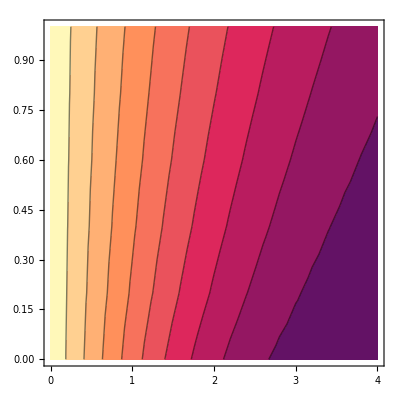

```mathematica
ListContourPlot[tbLs]
```

```mathematica
tblsNnorm=Table[tblsN[[i]],{i,1,Length[tblsN]}]
```

```mathematica
ListDensityPlot3D[data,OpacityFunction->(If[#<0.7,1,0]&)]
```

```mathematica
mn=Sqrt[Min[tbls[[All,4]]]]
```

0.021579

```mathematica
tbls2=Table[If[tbls[[i,4]]<mn*1.05,{tbls[[i,1]],tbls[[i,2]],tbls[[i,3]]},Nothing],{i,1,Length[tbls]}]
```

```mathematica
tbls2s={{1.5999999999999999,4.000000000000001,0},{1.7999999999999998,4.000000000000001,0},{1.9999999999999998,3.800000000000001,0},{1.9999999999999998,4.000000000000001,0},{2.1999999999999997,3.800000000000001,0},{2.1999999999999997,4.000000000000001,0},{2.4,3.600000000000001,0},{2.4,3.800000000000001,0},{2.4,4.000000000000001,0},{2.6,3.400000000000001,0},{2.6,3.600000000000001,0},{2.6,3.800000000000001,0},{2.6,4.000000000000001,0},{2.6,4.000000000000001,0.2},{2.8000000000000003,3.400000000000001,0},{2.8000000000000003,3.600000000000001,0},{2.8000000000000003,3.800000000000001,0},{2.8000000000000003,3.800000000000001,0.2},{2.8000000000000003,4.000000000000001,0},{2.8000000000000003,4.000000000000001,0.2},{3.0000000000000004,3.2000000000000006,0},{3.0000000000000004,3.400000000000001,0},{3.0000000000000004,3.600000000000001,0},{3.0000000000000004,3.800000000000001,0},{3.0000000000000004,3.800000000000001,0.2},{3.0000000000000004,4.000000000000001,0},{3.0000000000000004,4.000000000000001,0.2},{3.2000000000000006,3.2000000000000006,0},{3.2000000000000006,3.400000000000001,0},{3.2000000000000006,3.600000000000001,0},{3.2000000000000006,3.600000000000001,0.2},{3.2000000000000006,3.800000000000001,0},{3.2000000000000006,3.800000000000001,0.2},{3.2000000000000006,4.000000000000001,0},{3.2000000000000006,4.000000000000001,0.2},{3.2000000000000006,4.000000000000001,0.4},{3.400000000000001,3.0000000000000004,0},{3.400000000000001,3.2000000000000006,0},{3.400000000000001,3.400000000000001,0},{3.400000000000001,3.600000000000001,0},{3.400000000000001,3.600000000000001,0.2},{3.400000000000001,3.800000000000001,0},{3.400000000000001,3.800000000000001,0.2},{3.400000000000001,4.000000000000001,0.2},{3.400000000000001,4.000000000000001,0.4},{3.600000000000001,3.0000000000000004,0},{3.600000000000001,3.2000000000000006,0},{3.600000000000001,3.400000000000001,0},{3.600000000000001,3.400000000000001,0.2},{3.600000000000001,3.600000000000001,0},{3.600000000000001,3.600000000000001,0.2},{3.600000000000001,3.800000000000001,0.2},{3.600000000000001,3.800000000000001,0.4},{3.600000000000001,4.000000000000001,0.2},{3.600000000000001,4.000000000000001,0.4},{3.800000000000001,2.8000000000000003,0},{3.800000000000001,3.0000000000000004,0},{3.800000000000001,3.2000000000000006,0},{3.800000000000001,3.2000000000000006,0.2},{3.800000000000001,3.400000000000001,0},{3.800000000000001,3.400000000000001,0.2},{3.800000000000001,3.600000000000001,0},{3.800000000000001,3.600000000000001,0.2},{3.800000000000001,3.600000000000001,0.4},{3.800000000000001,3.800000000000001,0.2},{3.800000000000001,3.800000000000001,0.4},{3.800000000000001,4.000000000000001,0.2},{3.800000000000001,4.000000000000001,0.4},{3.800000000000001,4.000000000000001,0.6000000000000001},{4.000000000000001,2.8000000000000003,0},{4.000000000000001,3.0000000000000004,0},{4.000000000000001,3.2000000000000006,0},{4.000000000000001,3.2000000000000006,0.2},{4.000000000000001,3.400000000000001,0},{4.000000000000001,3.400000000000001,0.2},{4.000000000000001,3.600000000000001,0.2},{4.000000000000001,3.600000000000001,0.4},{4.000000000000001,3.800000000000001,0.2},{4.000000000000001,3.800000000000001,0.4},{4.000000000000001,4.000000000000001,0.2},{4.000000000000001,4.000000000000001,0.4},{4.000000000000001,4.000000000000001,0.6000000000000001}};
```

```mathematica
ListPointPlot3D[{tbls2,tbls2s}]
```

-Graphics3D-

```mathematica
ListDensityPlot3D[tbls2,ColorFunction->"TemperatureMap",PlotLegends->Automatic,OpacityFunction->1]
```

-Graphics3D-

```mathematica
ListDensityPlot3D[tbls,ColorFunction->"TemperatureMap",PlotLegends->Automatic,OpacityFunction->0.1]
```

-Graphics3D-

```mathematica
PositionSmallest[tbls[[All,4]]]
```

{1633}

```mathematica
tbls[[1633]]
```

{2.4,4.,0,0.000221577}

```mathematica
ListPlot[tbls[All,4]]
```

```mathematica
model/.Ai->0.002/.lp->400/.α->0.5/.γ->3/.γo->3
```

9.52381×10^-6 ⅇ^(-3 x/80) (-600 ⅇ^(x/80)-2340 ⅇ^(17 x/800)+3150 ⅇ^(x/40))

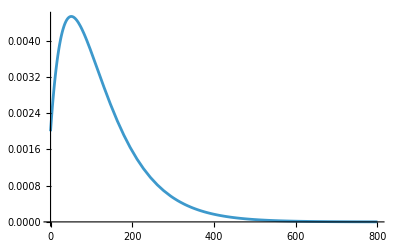

```mathematica
Plot[model/.Ai->0.002/.lp->400/.α->0.5/.γ->3/.γo->3,{x,0,800}]
```

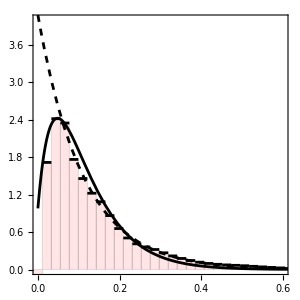

```mathematica
gr4e=Show[DiscretePlot[Interpolation[lst][x*1000]/0.0028,{x,0.00001,0.6,0.022},PlotRange->{{0,0.6},{0,4}},ExtentSize->Full,FillingStyle->Directive[EdgeForm[Black],Opacity[.1],Red],PlotStyle->Black,AspectRatio->1,Frame->True,FrameStyle->Directive[FSize,FontFamily->"Times",Black],FrameTicksStyle->Directive[FTicksSize],PlotLegends->Automatic],
(*Graphics[Text[Style["G1 (γ="<>ToString[γExp["Value"]]<>", γ_b="<>ToString[Round[γBExp["Value"]]]<>", γ_CTCF=1)",FontSize->16,FontFamily->"CMU Serif"],{0.06,2.35},{-1,0}]]*)
Plot[{model/.Ai->0.98/.lp->400/.α->0./.γ->2.6/.γo->3.8/.x->xi*1000},{xi,0,0.8},PlotStyle->{Directive[Black]}],Plot[{Am*Exp[-k*x*1000]/0.0028/.{Am->0.011421696614657459,k->0.009034414712030078}},{x,0,0.8},PlotStyle->{Directive[Black,Dashed]},PlotRange->All]]
```

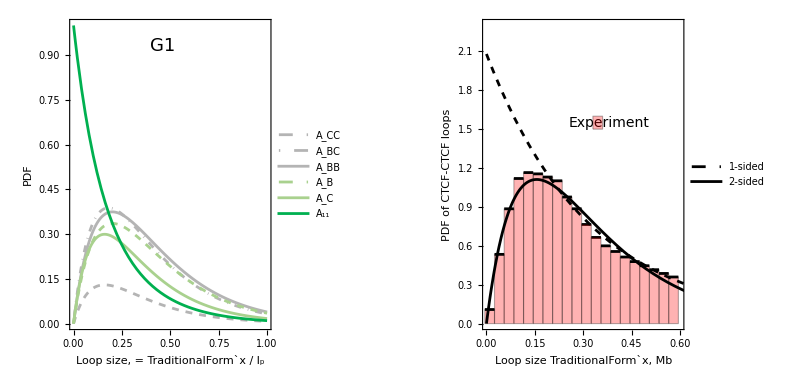

```mathematica
GraphicsRow[{gr4d,gr4e}]
```

## Фит для CTCF - CTCF Loops (Fig 4e)

```mathematica
Aoos
```

```mathematica
lstAoo=Import["C:\\петли\\ЭКСПЕРИМЕНТЫ\\chia-pet\\5k562.txt","Table"];
```

```mathematica
lstN=Import["C:\\петли\\ЭКСПЕРИМЕНТЫ\\chia-pet\\K562_rad21.txt","Table"];
```

```mathematica
modelAoo=Ai*Aoos/.x->x/lp;
```

```mathematica
modelN=Ai*A/.x->x/lp;
```

```mathematica
fit2=FindFit[lstAoo[[130;;Length[lstAoo]]],Am*Exp[-k*x],{{Am,0.001},{k,0.001}},x]
```

{Am→1.38513,k→2.39553}

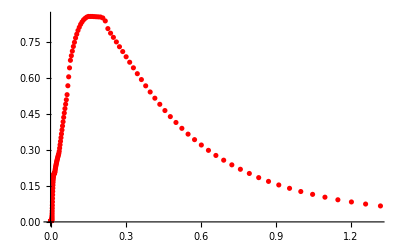

```mathematica
Show[ListPlot[lst,PlotStyle->Red],Plot[Am Exp[-k x]/.{Am->2.5300264137567883,k->0.9291143166956148},{x,21.63363493,901.65956}]]
```

```mathematica
posLeft=0.1+0.14;
posDown=2;
```

```mathematica
w=0.03;
```

```mathematica
FSize=20;
FTicksSize=15;
```

```mathematica
tblsN={};
intAoo=Interpolation[lstAoo];
intN=Interpolation[lstN];
```

InterpolatingFunction::dmval: Input value {0.0000408571} lies outside the range of data in the interpolating function. Extrapolation will be used.

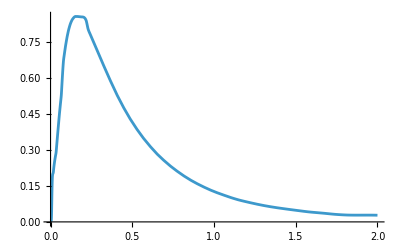

```mathematica
Plot[intAoo[s],{s,0,2}]
```

```mathematica
Norma=NIntegrate[intAoo[x],{x,0.01,0.6}]
```

0.349085

```mathematica
tblsAoof={};

NormAoo=nrmseAoo=NIntegrate[f,{x,0.01,0.6}]/(Ai/.ft)^2;
For[γi=3.0,γi<=3.2,γi=γi+0.2,{
For[γoi=0,γoi<=3,γoi=γoi+0.2,{
For[αi=0,αi<=1,αi=αi+0.2,{
ft = FindFit[lstAoo,modelAoo/.lp->0.6/.α->αi/.γ->γi/.γo->γoi,{{α,1.5},{γ,2},{γo,2},{Ai,3}},{x}];
f=(int[x]-(model/.lp->0.6/.α->αi/.γ->γi/.γo->γoi/.ft))^2;
nrmseAoo=NIntegrate[f,{x,0.01,0.6}];
AppendTo[tblsAoof,{γi,γoi,αi, nrmseAoo}];
}];
}];
Print[γi]
}]
```

FindFit::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

General::stop: Further output of FindFit::fmgz will be suppressed during this calculation.

3.

3.2

```mathematica
tblsAoos=Join[tblsAoo,tblsAoof]
```

```mathematica
tblsAoo={{3.2,0,0,0.2279067476531662},{3.2,0,0.2,0.2279067476531662},{3.2,0,0.4,0.2279067476531662},{3.2,0,0.6000000000000001,0.2279067476531662},{3.2,0,0.8,0.2279067476531662},{3.2,0,1.,0.2279067476531662},{3.2,0.2,0,0.0015269947575233874},{3.2,0.2,0.2,0.0005560381678324055},{3.2,0.2,0.4,0.0006767829347805378},{3.2,0.2,0.6000000000000001,0.0016289060698325708},{3.2,0.2,0.8,0.0031738560712369873},{3.2,0.2,1.,0.0051281820080234415},{3.2,0.4,0,0.0005425126970203586},{3.2,0.4,0.2,0.0005981294077583034},{3.2,0.4,0.4,0.0013718089150775168},{3.2,0.4,0.6000000000000001,0.0027439688022958073},{3.2,0.4,0.8,0.00455822183585982},{3.2,0.4,1.,0.0066816880702940075},{3.2,0.6000000000000001,0,0.0007375507071936934},{3.2,0.6000000000000001,0.2,0.0013752771843807562},{3.2,0.6000000000000001,0.4,0.0025618846481757105},{3.2,0.6000000000000001,0.6000000000000001,0.004206758680088821},{3.2,0.6000000000000001,0.8,0.006193473241793094},{3.2,0.6000000000000001,1.,0.00841963232351239},{3.2,0.8,0,0.0020230902468608295},{3.2,0.8,0.2,0.0028295355193974983},{3.2,0.8,0.4,0.004205686554582411},{3.2,0.8,0.6000000000000001,0.00598707944717658},{3.2,0.8,0.8,0.008057246981457194},{3.2,0.8,1.,0.010325262409941397},{3.2,1.,0,0.004278770070852895},{3.2,1.,0.2,0.0048932984683562955},{3.2,1.,0.4,0.006259018477902554},{3.2,1.,0.6000000000000001,0.008054165356702224},{3.2,1.,0.8,0.010127390919002777},{3.2,1.,1.,0.012382265236560422},{3.2,1.2,0,0.007369853980684682},{3.2,1.2,0.2,0.00749445848698914},{3.2,1.2,0.4,0.008676704136202116},{3.2,1.2,0.6000000000000001,0.010377448679987477},{3.2,1.2,0.8,0.012382291635269263},{3.2,1.2,1.,0.014574908558015803},{3.2,1.4,0,0.01115930119281316},{3.2,1.4,0.2,0.010560269986579204},{3.2,1.4,0.4,0.011414024462068875},{3.2,1.4,0.6000000000000001,0.012927142355164269},{3.2,1.4,0.8,0.014801120338928638},{3.2,1.4,1.,0.01688814458671497},{3.2,1.5999999999999999,0,0.01551571346547483},{3.2,1.5999999999999999,0.2,0.014020098671077733},{3.2,1.5999999999999999,0.4,0.014427766313277903},{3.2,1.5999999999999999,0.6000000000000001,0.01567466629950876},{3.2,1.5999999999999999,0.8,0.017364010260988504},{3.2,1.5999999999999999,1.,0.019307681921211663},{3.2,1.7999999999999998,0,0.020318092619423744},{3.2,1.7999999999999998,0.2,0.01780726215387934},{3.2,1.7999999999999998,0.4,0.017676950344516232},{3.2,1.7999999999999998,0.6000000000000001,0.018592944444757623},{3.2,1.7999999999999998,0.8,0.02005217746287523},{3.2,1.7999999999999998,1.,0.021820031374788915},{3.2,1.9999999999999998,0,0.02545827918790937},{3.2,1.9999999999999998,0.2,0.02186015967987001},{3.2,1.9999999999999998,0.4,0.02112330140648905},{3.2,1.9999999999999998,0.6000000000000001,0.02165659701428342},{3.2,1.9999999999999998,0.8,0.02284799563104172},{3.2,1.9999999999999998,1.,0.02441253057955363},{3.2,2.1999999999999997,0,0.030841795029299214},{3.2,2.1999999999999997,0.2,0.026122865591567852},{3.2,2.1999999999999997,0.4,0.024731517604396867},{3.2,2.1999999999999997,0.6000000000000001,0.024842049550913535},{3.2,2.1999999999999997,0.8,0.02573503404152817},{3.2,2.1999999999999997,1.,0.027073351568859923},{3.2,2.4,0,0.036387649014168875},{3.2,2.4,0.2,0.0305453324570203},{3.2,2.4,0.4,0.02846938590896558},{3.2,2.4,0.6000000000000001,0.02812757710408819},{3.2,2.4,0.8,0.028698066541117954},{3.2,2.4,1.,0.02979149492044295},{3.2,2.6,0,0.04202751660588038},{3.2,2.6,0.2,0.035083321021046505},{3.2,2.6,0.4,0.03230778403131667},{3.2,2.6,0.6000000000000001,0.03149329902057322},{3.2,2.6,0.8,0.03172305815618409},{3.2,2.6,1.,0.03255677348302047},{3.2,2.8000000000000003,0,0.04770458241582746},{3.2,2.8000000000000003,0.2,0.03969814809698305},{3.2,2.8000000000000003,0.4,0.03622060072456141},{3.2,2.8000000000000003,0.6000000000000001,0.034921137076768506},{3.2,2.8000000000000003,0.8,0.034797134830129486},{3.2,2.8000000000000003,1.,0.03535978821301258},{3.2,3.0000000000000004,0,0.0533722408099752},{3.2,3.0000000000000004,0.2,0.04435632130011393},{3.2,3.0000000000000004,0.4,0.040184600029539795},{3.2,3.0000000000000004,0.6000000000000001,0.0383947472985476},{3.2,3.0000000000000004,0.8,0.0379085408136058},{3.2,3.0000000000000004,1.,0.03819189821423819},{3.4000000000000004,0,0,0.2279067476531662},{3.4000000000000004,0,0.2,0.2279067476531662},{3.4000000000000004,0,0.4,0.2279067476531662},{3.4000000000000004,0,0.6000000000000001,0.2279067476531662},{3.4000000000000004,0,0.8,0.2279067476531662},{3.4000000000000004,0,1.,0.2279067476531662},{3.4000000000000004,0.2,0,0.000970796339848101},{3.4000000000000004,0.2,0.2,0.00048706415286892796},{3.4000000000000004,0.2,0.4,0.0010795869102178995},{3.4000000000000004,0.2,0.6000000000000001,0.0024623250989934797},{3.4000000000000004,0.2,0.8,0.0043904012889472615},{3.4000000000000004,0.2,1.,0.0066816880702939875},{3.4000000000000004,0.4,0,0.00048502169670280507},{3.4000000000000004,0.4,0.2,0.0009317875792638256},{3.4000000000000004,0.4,0.4,0.0021039417800108717},{3.4000000000000004,0.4,0.6000000000000001,0.0038480520116785013},{3.4000000000000004,0.4,0.8,0.005997904155419171},{3.4000000000000004,0.4,1.,0.008419632323512376},{3.4000000000000004,0.6000000000000001,0,0.001149075780073493},{3.4000000000000004,0.6000000000000001,0.2,0.0020821081520514977},{3.4000000000000004,0.6000000000000001,0.4,0.003596494739539794},{3.4000000000000004,0.6000000000000001,0.6000000000000001,0.005558139466978759},{3.4000000000000004,0.6000000000000001,0.8,0.007836409002413914},{3.4000000000000004,0.6000000000000001,1.,0.010325262409941386},{3.4000000000000004,0.8,0,0.00285830638858235},{3.4000000000000004,0.8,0.2,0.0038742113570438092},{3.4000000000000004,0.8,0.4,0.005513868995020843},{3.4000000000000004,0.8,0.6000000000000001,0.007561921649391688},{3.4000000000000004,0.8,0.8,0.009883740318407615},{3.4000000000000004,0.8,1.,0.0123822652365604},{3.4000000000000004,1.,0,0.005484218876642737},{3.4000000000000004,1.,0.2,0.006237525050898752},{3.4000000000000004,1.,0.4,0.007811094506478545},{3.4000000000000004,1.,0.6000000000000001,0.00982876501755112},{3.4000000000000004,1.,0.8,0.012118225378338928},{3.4000000000000004,1.,1.,0.014574908558015813},{3.4000000000000004,1.2,0,0.008889457559214558},{3.4000000000000004,1.2,0.2,0.009099177128774706},{3.4000000000000004,1.2,0.4,0.010443197370468782},{3.4000000000000004,1.2,0.6000000000000001,0.01232869142133582},{3.4000000000000004,1.2,0.8,0.014518949056056402},{3.4000000000000004,1.2,1.,0.016888144586714983},{3.4000000000000004,1.4,0,0.012938124277267133},{3.4000000000000004,1.4,0.2,0.012387245913806775},{3.4000000000000004,1.4,0.4,0.013366376998606894},{3.4000000000000004,1.4,0.6000000000000001,0.015032838499176674},{3.4000000000000004,1.4,0.8,0.0170659386945253},{3.4000000000000004,1.4,1.,0.01930768192121156},{3.4000000000000004,1.5999999999999999,0,0.01750232619097534},{3.4000000000000004,1.5999999999999999,0.2,0.01603300320357266},{3.4000000000000004,1.5999999999999999,0.4,0.016538839173395953},{3.4000000000000004,1.5999999999999999,0.6000000000000001,0.01791378481449119},{3.4000000000000004,1.5999999999999999,0.8,0.019740291095505486},{3.4000000000000004,1.5999999999999999,1.,0.021820031374788978},{3.4000000000000004,1.7999999999999998,0,0.022465888256040907},{3.4000000000000004,1.7999999999999998,0.2,0.01997235472775402},{3.4000000000000004,1.7999999999999998,0.4,0.019921350265951956},{3.4000000000000004,1.7999999999999998,0.6000000000000001,0.02094576485171924},{3.4000000000000004,1.7999999999999998,0.8,0.022524252349397554},{3.4000000000000004,1.7999999999999998,1.,0.024412530579553664},{3.4000000000000004,1.9999999999999998,0,0.027726053343173494},{3.4000000000000004,1.9999999999999998,0.2,0.0241466651257736},{3.4000000000000004,1.9999999999999998,0.4,0.023477571415452782},{3.4000000000000004,1.9999999999999998,0.6000000000000001,0.024104796063933776},{3.4000000000000004,1.9999999999999998,0.8,0.025401259838847664},{3.4000000000000004,1.9999999999999998,1.,0.027073351568859934},{3.4000000000000004,2.1999999999999997,0,0.033193830327924466},{3.4000000000000004,2.1999999999999997,0.2,0.0285031273965611},{3.4000000000000004,2.1999999999999997,0.4,0.027174223446006496},{3.4000000000000004,2.1999999999999997,0.6000000000000001,0.027368737070624326},{3.4000000000000004,2.1999999999999997,0.8,0.028355954406768816},{3.4000000000000004,2.1999999999999997,1.,0.029791494920443},{3.4000000000000004,2.4,0,0.038793488801871},{3.4000000000000004,2.4,0.2,0.032994807457325304},{3.4000000000000004,2.4,0.4,0.030981125021140206},{3.4000000000000004,2.4,0.6000000000000001,0.030717293102489183},{3.4000000000000004,2.4,0.8,0.031374169432870594},{3.4000000000000004,2.4,1.,0.03255677348302046},{3.4000000000000004,2.6,0,0.04446155968005925},{3.4000000000000004,2.6,0.2,0.037580466841280566},{3.4000000000000004,2.6,0.4,0.03487113873210462},{3.4000000000000004,2.6,0.6000000000000001,0.03413198202320188},{3.4000000000000004,2.6,0.8,0.03444290243914696},{3.4000000000000004,2.6,1.,0.03535978821301255},{3.4000000000000004,2.8000000000000003,0,0.05014558991729434},{3.4000000000000004,2.8000000000000003,0.2,0.04222424243308094},{3.4000000000000004,2.8000000000000003,0.4,0.03882005284485901},{3.4000000000000004,2.8000000000000003,0.6000000000000001,0.037596071795242846},{3.4000000000000004,2.8000000000000003,0.8,0.037550273853809386},{3.4000000000000004,2.8000000000000003,1.,0.03819189821423814},{3.4000000000000004,3.0000000000000004,0,0.05580281557216114},{3.4000000000000004,3.0000000000000004,0.2,0.04689524204179662},{3.4000000000000004,3.0000000000000004,0.4,0.042806420429257294},{3.4000000000000004,3.0000000000000004,0.6000000000000001,0.041094498119982566},{3.4000000000000004,3.0000000000000004,0.8,0.040685476703995235},{3.4000000000000004,3.0000000000000004,1.,0.04104518669842486},{3.6000000000000005,0,0,0.2279067476531662},{3.6000000000000005,0,0.2,0.2279067476531662},{3.6000000000000005,0,0.4,0.2279067476531662},{3.6000000000000005,0,0.6000000000000001,0.2279067476531662},{3.6000000000000005,0,0.8,0.2279067476531662},{3.6000000000000005,0,1.,0.2279067476531662},{3.6000000000000005,0.2,0,0.0006250455496584071},{3.6000000000000005,0.2,0.2,0.0006380591404241076},{3.6000000000000005,0.2,0.4,0.0017009438580676323},{3.6000000000000005,0.2,0.6000000000000001,0.003506111009211235},{3.6000000000000005,0.2,0.8,0.005805311488921534},{3.6000000000000005,0.2,1.,0.008419632323512343},{3.6000000000000005,0.4,0,0.0006274935938930728},{3.6000000000000005,0.4,0.2,0.0014699314134869698},{3.6000000000000005,0.4,0.4,0.0030369510442714138},{3.6000000000000005,0.4,0.6000000000000001,0.0051443463746491565},{3.6000000000000005,0.4,0.8,0.007618259493580857},{3.6000000000000005,0.4,1.,0.01032526240994136},{3.6000000000000005,0.6000000000000001,0,0.0017426235540355856},{3.6000000000000005,0.6000000000000001,0.2,0.002974484696460741},{3.6000000000000005,0.6000000000000001,0.4,0.004812875602717981},{3.6000000000000005,0.6000000000000001,0.6000000000000001,0.007083200356578706},{3.6000000000000005,0.6000000000000001,0.8,0.00964249483961545},{3.6000000000000005,0.6000000000000001,1.,0.012382265236560422},{3.6000000000000005,0.8,0,0.003853454559689074},{3.6000000000000005,0.8,0.2,0.005083666444104613},{3.6000000000000005,0.8,0.4,0.0069841506384356045},{3.6000000000000005,0.8,0.6000000000000001,0.009292008590688253},{3.6000000000000005,0.8,0.8,0.011856289254370012},{3.6000000000000005,0.8,1.,0.014574908558015803},{3.6000000000000005,1.,0,0.0068258582816433586},{3.6000000000000005,1.,0.2,0.007725187990408633},{3.6000000000000005,1.,0.4,0.009505693108410684},{3.6000000000000005,1.,0.6000000000000001,0.011740627927894024},{3.6000000000000005,1.,0.8,0.014238644069440302},{3.6000000000000005,1.,1.,0.016888144586714962},{3.6000000000000005,1.2,0,0.010521612580655823},{3.6000000000000005,1.2,0.2,0.010826323643179836},{3.6000000000000005,1.2,0.4,0.012333217954650024},{3.6000000000000005,1.2,0.6000000000000001,0.014399932376622364},{3.6000000000000005,1.2,0.8,0.01676948272445618},{3.6000000000000005,1.2,1.,0.019307681921211555},{3.6000000000000005,1.4,0,0.014807099380656781},{3.6000000000000005,1.4,0.2,0.01431660375535976},{3.6000000000000005,1.4,0.4,0.01542418446339547},{3.6000000000000005,1.4,0.6000000000000001,0.017242167687609347},{3.6000000000000005,1.4,0.8,0.019429784080683327},{3.6000000000000005,1.4,1.,0.021820031374788964},{3.6000000000000005,1.5999999999999999,0,0.01955859764738399},{3.6000000000000005,1.5999999999999999,0.2,0.018129608770931376},{3.6000000000000005,1.5999999999999999,0.4,0.018738441605454945},{3.6000000000000005,1.5999999999999999,0.6000000000000001,0.02024119026759775},{3.6000000000000005,1.5999999999999999,0.8,0.022201667411576313},{3.6000000000000005,1.5999999999999999,1.,0.02441253057955368},{3.6000000000000005,1.7999999999999998,0,0.024665081577161116},{3.6000000000000005,1.7999999999999998,0.2,0.022204061963078076},{3.6000000000000005,1.7999999999999998,0.4,0.02223863364025749},{3.6000000000000005,1.7999999999999998,0.6000000000000001,0.023372613285091503},{3.6000000000000005,1.7999999999999998,0.8,0.025068438554068942},{3.6000000000000005,1.7999999999999998,1.,0.027073351568859892},{3.6000000000000005,1.9999999999999998,0,0.03002928931977295},{3.6000000000000005,1.9999999999999998,0.2,0.026484394563244293},{3.6000000000000005,1.9999999999999998,0.4,0.02589041961391068},{3.6000000000000005,1.9999999999999998,0.6000000000000001,0.02661387975917521},{3.6000000000000005,1.9999999999999998,0.8,0.028014605356138842},{3.6000000000000005,1.9999999999999998,1.,0.029791494920442925},{3.6000000000000005,2.1999999999999997,0,0.03556765892377261},{3.6000000000000005,2.1999999999999997,0.2,0.030920927911115222},{3.6000000000000005,2.1999999999999997,0.4,0.029662552100362123},{3.6000000000000005,2.1999999999999997,0.6000000000000001,0.029944279391682514},{3.6000000000000005,2.1999999999999997,0.8,0.031025869299055348},{3.6000000000000005,2.1999999999999997,1.,0.03255677348302046},{3.6000000000000005,2.4,0,0.04120957245844018},{3.6000000000000005,2.4,0.2,0.03546978843647632},{3.6000000000000005,2.4,0.4,0.03352685251895771},{3.6000000000000005,2.4,0.6000000000000001,0.03334492307965551},{3.6000000000000005,2.4,0.8,0.034089099035849134},{3.6000000000000005,2.4,1.,0.03535978821301259},{3.6000000000000005,2.6,0,0.04689622012302496},{3.6000000000000005,2.6,0.2,0.04009264532960013},{3.6000000000000005,2.6,0.4,0.037458113080993526},{3.6000000000000005,2.6,0.6000000000000001,0.03679868651297543},{3.6000000000000005,2.6,0.8,0.037192290582389306},{3.6000000000000005,2.6,1.,0.03819189821423816},{3.6000000000000005,2.8000000000000003,0,0.05257929580556963},{3.6000000000000005,2.8000000000000003,0.2,0.04475633870168235},{3.6000000000000005,2.8000000000000003,0.4,0.041433949076009835},{3.6000000000000005,2.8000000000000003,0.6000000000000001,0.0402901320526171},{3.6000000000000005,2.8000000000000003,0.8,0.04032451802422714},{3.6000000000000005,2.8000000000000003,1.,0.04104518669842484},{3.6000000000000005,3.0000000000000004,0,0.058219661096390755},{3.6000000000000005,3.0000000000000004,0.2,0.0494324480323528},{3.6000000000000005,3.0000000000000004,0.4,0.04543461984913039},{3.6000000000000005,3.0000000000000004,0.6000000000000001,0.04380541619722178},{3.6000000000000005,3.0000000000000004,0.8,0.043475877854476166},{3.6000000000000005,3.0000000000000004,1.,0.043912424263264145},{3.8000000000000007,0,0,0.2279067476531662},{3.8000000000000007,0,0.2,0.2279067476531662},{3.8000000000000007,0,0.4,0.2279067476531662},{3.8000000000000007,0,0.6000000000000001,0.2279067476531662},{3.8000000000000007,0,0.8,0.2279067476531662},{3.8000000000000007,0,1.,0.2279067476531662},{3.8000000000000007,0.2,0,0.00048561317918461764},{3.8000000000000007,0.2,0.2,0.0010005811692443988},{3.8000000000000007,0.2,0.4,0.002529068870170775},{3.8000000000000007,0.2,0.6000000000000001,0.004746102535768993},{3.8000000000000007,0.2,0.8,0.00740283380503159},{3.8000000000000007,0.2,1.,0.010325262409941353},{3.8000000000000007,0.4,0,0.0009623835593916869},{3.8000000000000007,0.4,0.2,0.0022021447576348555},{3.8000000000000007,0.4,0.4,0.004158083797775831},{3.8000000000000007,0.4,0.6000000000000001,0.006618399928263297},{3.8000000000000007,0.4,0.8,0.00940368895205186},{3.8000000000000007,0.4,1.,0.012382265236560412},{3.8000000000000007,0.6000000000000001,0,0.002508685879922931},{3.8000000000000007,0.6000000000000001,0.2,0.004040930044495795},{3.8000000000000007,0.6000000000000001,0.4,0.006197886965525481},{3.8000000000000007,0.6000000000000001,0.6000000000000001,0.008767566594405484},{3.8000000000000007,0.6000000000000001,0.8,0.011596516465853236},{3.8000000000000007,0.6000000000000001,1.,0.014574908558015826},{3.8000000000000007,0.8,0,0.004998188099593581},{3.8000000000000007,0.8,0.2,0.006446068935166574},{3.8000000000000007,0.8,0.4,0.008603449291240108},{3.8000000000000007,0.8,0.6000000000000001,0.011163322454872402},{3.8000000000000007,0.8,0.8,0.013960237034216547},{3.8000000000000007,0.8,1.,0.01688814458671499},{3.8000000000000007,1.,0,0.008293307743108437},{3.8000000000000007,1.,0.2,0.00934461808300688},{3.8000000000000007,1.,0.4,0.011330118548039827},{3.8000000000000007,1.,0.6000000000000001,0.013776298176362682},{3.8000000000000007,1.,0.8,0.016474672266125368},{3.8000000000000007,1.,1.,0.01930768192121165},{3.8000000000000007,1.2,0,0.012256437217617426},{3.8000000000000007,1.2,0.2,0.012664750755091082},{3.8000000000000007,1.2,0.4,0.014334687364241419},{3.8000000000000007,1.2,0.6000000000000001,0.016578420583458195},{3.8000000000000007,1.2,0.8,0.019120684473532372},{3.8000000000000007,1.2,1.,0.02182003137478897},{3.8000000000000007,1.4,0,0.01675716335762347},{3.8000000000000007,1.4,0.2,0.01633795019665957},{3.8000000000000007,1.4,0.4,0.017576137326749574},{3.8000000000000007,1.4,0.6000000000000001,0.019543176726067226},{3.8000000000000007,1.4,0.8,0.02188026695008171},{3.8000000000000007,1.4,1.,0.02441253057955362},{3.8000000000000007,1.5999999999999999,0,0.021676447042947924},{3.8000000000000007,1.5999999999999999,0.2,0.020300409817192777},{3.8000000000000007,1.5999999999999999,0.4,0.02101612268979962},{3.8000000000000007,1.5999999999999999,0.6000000000000001,0.022645780120159133},{3.8000000000000007,1.5999999999999999,0.8,0.024736594380669833},{3.8000000000000007,1.5999999999999999,1.,0.02707335156885992},{3.8000000000000007,1.7999999999999998,0,0.026908628981134265},{3.8000000000000007,1.7999999999999998,0.2,0.024493826739249713},{3.8000000000000007,1.7999999999999998,0.4,0.024619250100230645},{3.8000000000000007,1.7999999999999998,0.6000000000000001,0.025863259644944653},{3.8000000000000007,1.7999999999999998,0.8,0.02767404166305042},{3.8000000000000007,1.7999999999999998,1.,0.029791494920442953},{3.8000000000000007,1.9999999999999998,0,0.0323619639284486},{3.8000000000000007,1.9999999999999998,0.2,0.028865747552609393},{3.8000000000000007,1.9999999999999998,0.4,0.02835320257272824},{3.8000000000000007,1.9999999999999998,0.6000000000000001,0.029174488529533922},{3.8000000000000007,1.9999999999999998,0.8,0.03067817815548735},{3.8000000000000007,1.9999999999999998,1.,0.03255677348302045},{3.8000000000000007,2.1999999999999997,0,0.03795821736996627},{3.8000000000000007,2.1999999999999997,0.2,0.03336959562007922},{3.8000000000000007,2.1999999999999997,0.4,0.03218874777795514},{3.8000000000000007,2.1999999999999997,0.6000000000000001,0.03256016798732533},{3.8000000000000007,2.1999999999999997,0.8,0.03373574321460728},{3.8000000000000007,2.1999999999999997,1.,0.03535978821301256},{3.8000000000000007,2.4,0,0.043631711496384916},{3.8000000000000007,2.4,0.2,0.03796448169772288},{3.8000000000000007,2.4,0.4,0.0360996631410281},{3.8000000000000007,2.4,0.6000000000000001,0.03600277745724092},{3.8000000000000007,2.4,0.8,0.03683460786833395},{3.8000000000000007,2.4,1.,0.038191898214238136},{3.8000000000000007,2.6,0,0.04932808905799743},{3.8000000000000007,2.6,0.2,0.042614875627863306},{3.8000000000000007,2.6,0.4,0.04006260357048772},{3.8000000000000007,2.6,0.6000000000000001,0.039486501129239876},{3.8000000000000007,2.6,0.8,0.03996372658144972},{3.8000000000000007,2.6,1.,0.041045186698424836},{3.8000000000000007,2.8000000000000003,0,0.05500297377451779},{3.8000000000000007,2.8000000000000003,0.2,0.047290196932924765},{3.8000000000000007,2.8000000000000003,0.4,0.04405693193937356},{3.8000000000000007,2.8000000000000003,0.6000000000000001,0.042997138472737215},{3.8000000000000007,2.8000000000000003,0.8,0.04311308231005211},{3.8000000000000007,2.8000000000000003,1.,0.04391242426326409},{3.8000000000000007,3.0000000000000004,0,0.0606206404114174},{3.8000000000000007,3.0000000000000004,0.2,0.05196436614814608},{3.8000000000000007,3.0000000000000004,0.4,0.04806452769916842},{3.8000000000000007,3.0000000000000004,0.6000000000000001,0.04652200483462701},{3.8000000000000007,3.0000000000000004,0.8,0.04627362739596962},{3.8000000000000007,3.0000000000000004,1.,0.04678703061213054},{4.000000000000001,0,0,0.2279067476531662},{4.000000000000001,0,0.2,0.2279067476531662},{4.000000000000001,0,0.4,0.2279067476531662},{4.000000000000001,0,0.6000000000000001,0.2279067476531662},{4.000000000000001,0,0.8,0.2279067476531662},{4.000000000000001,0,1.,0.2279067476531662},{4.000000000000001,0.2,0,0.0005468694048100793},{4.000000000000001,0.2,0.2,0.001565098219429417},{4.000000000000001,0.2,0.4,0.0035515405255251192},{4.000000000000001,0.2,0.6000000000000001,0.006167920968968589},{4.000000000000001,0.2,0.8,0.0091673572697317},{4.000000000000001,0.2,1.,0.01238226523656042},{4.000000000000001,0.4,0,0.0014812812107715832},{4.000000000000001,0.4,0.2,0.0031174308630911385},{4.000000000000001,0.4,0.4,0.005454339660431463},{4.000000000000001,0.4,0.6000000000000001,0.008255829920370782},{4.000000000000001,0.4,0.8,0.011338940399555849},{4.000000000000001,0.4,1.,0.014574908558015824},{4.000000000000001,0.6000000000000001,0,0.0034373900052403882},{4.000000000000001,0.6000000000000001,0.2,0.0052697820651285785},{4.000000000000001,0.6000000000000001,0.4,0.007738439607984541},{4.000000000000001,0.6000000000000001,0.6000000000000001,0.010597150376258406},{4.000000000000001,0.6000000000000001,0.8,0.0136837598177271},{4.000000000000001,0.6000000000000001,1.,0.016888144586714997},{4.000000000000001,0.8,0,0.0062821583260511136},{4.000000000000001,0.8,0.2,0.007949692330186312},{4.000000000000001,0.8,0.4,0.0103589537170803},{4.000000000000001,0.8,0.6000000000000001,0.013162291669330773},{4.000000000000001,0.8,0.8,0.016181537465313676},{4.000000000000001,0.8,1.,0.01930768192121156},{4.000000000000001,1.,0,0.009876426473935523},{4.000000000000001,1.,0.2,0.011084453294320687},{4.000000000000001,1.,0.4,0.01327210027314921},{4.000000000000001,1.,0.6000000000000001,0.015922876986907055},{4.000000000000001,1.,0.8,0.018813020569968048},{4.000000000000001,1.,1.,0.02182003137478897},{4.000000000000001,1.2,0,0.014084435131970283},{4.000000000000001,1.2,0.2,0.014603748425714385},{4.000000000000001,1.2,0.4,0.01643605331206208},{4.000000000000001,1.2,0.6000000000000001,0.018852033864648923},{4.000000000000001,1.2,0.8,0.021560077342269033},{4.000000000000001,1.2,1.,0.02441253057955364},{4.000000000000001,1.4,0,0.01877971284938598},{4.000000000000001,1.4,0.2,0.018441403653491343},{4.000000000000001,1.4,0.4,0.019811511483933907},{4.000000000000001,1.4,0.6000000000000001,0.02192458167766244},{4.000000000000001,1.4,0.8,0.024405751756097327},{4.000000000000001,1.4,1.,0.027073351568859937},{4.000000000000001,1.5999999999999999,0,0.023848277491488976},{4.000000000000001,1.5999999999999999,0.2,0.02253644556670697},{4.000000000000001,1.5999999999999999,0.4,0.023362044029331817},{4.000000000000001,1.5999999999999999,0.6000000000000001,0.0251171373008641},{4.000000000000001,1.5999999999999999,0.8,0.027334285840612413},{4.000000000000001,1.5999999999999999,1.,0.029791494920443026},{4.000000000000001,1.7999999999999998,0,0.029189961658305084},{4.000000000000001,1.7999999999999998,0.2,0.026833640028335076},{4.000000000000001,1.7999999999999998,0.4,0.027054264990038015},{4.000000000000001,1.7999999999999998,0.6000000000000001,0.028408157051914233},{4.000000000000001,1.7999999999999998,0.8,0.030331116634671147},{4.000000000000001,1.7999999999999998,1.,0.03255677348302049},{4.000000000000001,1.9999999999999998,0,0.034718499196377116},{4.000000000000001,1.9999999999999998,0.2,0.03128365465209926},{4.000000000000001,1.9999999999999998,0.4,0.030857878524192965},{4.000000000000001,1.9999999999999998,0.6000000000000001,0.03177793010974293},{4.000000000000001,1.9999999999999998,0.8,0.03338285379195623},{4.000000000000001,1.9999999999999998,1.,0.035359788213012576},{4.000000000000001,2.1999999999999997,0,0.04036084659372252},{4.000000000000001,2.1999999999999997,0.2,0.03584295970751229},{4.000000000000001,2.1999999999999997,0.4,0.03474563037971203},{4.000000000000001,2.1999999999999997,0.6000000000000001,0.035208535938166204},{4.000000000000001,2.1999999999999997,0.8,0.0364772427917804},{4.000000000000001,2.1999999999999997,1.,0.03819189821423814},{4.000000000000001,2.4,0,0.04605607603820223},{4.000000000000001,2.4,0.2,0.04047355614391863},{4.000000000000001,2.4,0.4,0.03869319357785731},{4.000000000000001,2.4,0.6000000000000001,0.03868377589077386},{4.000000000000001,2.4,0.8,0.03960311780907775},{4.000000000000001,2.4,1.,0.0410451866984248},{4.000000000000001,2.6,0,0.05175406971506006},{4.000000000000001,2.6,0.2,0.04514259751570963},{4.000000000000001,2.6,0.4,0.042679010318321636},{4.000000000000001,2.6,0.6000000000000001,0.04218908714282081},{4.000000000000001,2.6,0.8,0.042750347522314124},{4.000000000000001,2.6,1.,0.04391242426326413},{4.000000000000001,2.8000000000000003,0,0.05741416498764563},{4.000000000000001,2.8000000000000003,0.2,0.049821954754022645},{4.000000000000001,2.8000000000000003,0.4,0.046684107049450925},{4.000000000000001,2.8000000000000003,0.6000000000000001,0.0457114453764387},{4.000000000000001,2.8000000000000003,0.8,0.045909776480429085},{4.000000000000001,2.8000000000000003,1.,0.04678703061213052},{4.000000000000001,3.0000000000000004,0,0.0630038427366298},{4.000000000000001,3.0000000000000004,0.2,0.054487758637701084},{4.000000000000001,3.0000000000000004,0.4,0.05069189548831508},{4.000000000000001,3.0000000000000004,0.6000000000000001,0.04923926121187574},{4.000000000000001,3.0000000000000004,0.8,0.049073164097719335},{4.000000000000001,3.0000000000000004,1.,0.04966303560989082},{0,0,0,0.2279067476531662},{0,0,0.2,0.2279067476531662},{0,0,0.4,0.2279067476531662},{0,0,0.6000000000000001,0.2279067476531662},{0,0,0.8,0.2279067476531662},{0,0,1.,0.03298732824187603},{0,0.2,0,0.03298732824187603},{0,0.2,0.2,0.02914066111747763},{0,0.2,0.4,0.025285741362951725},{0,0.2,0.6000000000000001,0.021655736805143256},{0,0.2,0.8,0.01835338087596244},{0,0.2,1.,0.015421182756319507},{0,0.4,0,0.02729521505777165},{0,0.4,0.2,0.024441039040120287},{0,0.4,0.4,0.02125959076641337},{0,0.4,0.6000000000000001,0.018172022516987484},{0,0.4,0.8,0.015340176418869457},{0,0.4,1.,0.012826273535614654},{0,0.6000000000000001,0,0.0215001940273144},{0,0.6000000000000001,0.2,0.019746952451516874},{0,0.6000000000000001,0.4,0.017320211218684052},{0,0.6000000000000001,0.6000000000000001,0.014827250398210458},{0,0.6000000000000001,0.8,0.012494751937090856},{0,0.6000000000000001,1.,0.010411332666688772},{0,0.8,0,0.01587954826497878},{0,0.8,0.2,0.015229172163964393},{0,0.8,0.4,0.013583118055673646},{0,0.8,0.6000000000000001,0.011700259496579114},{0,0.8,0.8,0.009870489264791645},{0,0.8,1.,0.008212082766873914},{0,1.,0,0.01079387405973936},{0,1.,0.2,0.011083695915418215},{0,1.,0.4,0.010166622245992369},{0,1.,0.6000000000000001,0.008865603652394785},{0,1.,0.8,0.00751507187866795},{0,1.,1.,0.0062590363338773675},{0,1.2,0,0.006554490868991192},{0,1.2,0.2,0.0074848613900746},{0,1.2,0.4,0.007173775803769548},{0,1.2,0.6000000000000001,0.006386269961826388},{0,1.2,0.8,0.005467525986069663},{0,1.2,1.,0.004576340640189166},{0,1.4,0,0.003373498333383215},{0,1.4,0.2,0.004564185875047134},{0,1.4,0.4,0.004683910855515612},{0,1.4,0.6000000000000001,0.004310388717591542},{0,1.4,0.8,0.09115609490553286},{0,1.4,1.,0.0031814521440468578},{0,1.5999999999999999,0,0.0013586363100900748},{0,1.5999999999999999,0.2,0.0024049577846947242},{0,1.5999999999999999,0.4,0.0027503255637693932},{0,1.5999999999999999,0.6000000000000001,0.0026705444777711017},{0,1.5999999999999999,0.8,0.002402950502295337},{0,1.5999999999999999,1.,0.0020853508225325396},{0,1.7999999999999998,0,0.000528806778937892},{0,1.7999999999999998,0.2,0.0010454989178637453},{0,1.7999999999999998,0.4,0.0014015886883364974},{0,1.7999999999999998,0.6000000000000001,0.001484660782754036},{0,1.7999999999999998,0.8,0.0014154291970085561},{0,1.7999999999999998,1.,0.001293081065278814},{0,1.9999999999999998,0,0.000836440504810005},{0,1.9999999999999998,0.2,0.00048649089354085487},{0,1.9999999999999998,0.4,0.0006447308212604631},{0,1.9999999999999998,0.6000000000000001,0.0007577384579532529},{0,1.9999999999999998,0.8,0.0007965669742516687},{0,1.9999999999999998,1.,0.0008044673359415996},{0,2.1999999999999997,0,0.0021895906368861787},{0,2.1999999999999997,0.2,0.0006995760142939347},{0,2.1999999999999997,0.4,0.0004692010685210251},{0,2.1999999999999997,0.6000000000000001,0.00048396585369225447},{0,2.1999999999999997,0.8,0.0005416179151918031},{0,2.1999999999999997,1.,0.0006149003452111107},{0,2.4,0,0.004470631276940741},{0,2.4,0.2,0.0016356765431420899},{0,2.4,0.4,0.0008509059237400841},{0,2.4,0.6000000000000001,0.0006488945553970065},{0,2.4,0.8,0.0006402713912970478},{0,2.4,1.,0.000716124983634192},{0,2.6,0,0.007550645309523009},{0,2.6,0.2,0.003232268103232571},{0,2.6,0.4,0.0017559466288777526},{0,2.6,0.6000000000000001,0.0012314978224658162},{0,2.6,0.8,0.0010778608915064248},{0,2.6,1.,0.0010969870634726542},{0,2.8000000000000003,0,0.011299688587984157},{0,2.8000000000000003,0.2,0.005419323785879736},{0,2.8000000000000003,0.4,0.0031438677928309422},{0,2.8000000000000003,0.6000000000000001,0.0022060134278898244},{0,2.8000000000000003,0.8,0.0018364606941197567},{0,2.8000000000000003,1.,0.0017441141974598668},{0,3.0000000000000004,0,0.01559358122983585},{0,3.0000000000000004,0.2,0.008123918535267853},{0,3.0000000000000004,0.4,0.004970353202813474},{0,3.0000000000000004,0.6000000000000001,0.0035435281433288507},{0,3.0000000000000004,0.8,0.0028958469635808233},{0,3.0000000000000004,1.,0.0026425187526248105},{0.2,0,0,0.2279067476531662},{0.2,0,0.2,0.2279067476531662},{0.2,0,0.4,0.2279067476531662},{0.2,0,0.6000000000000001,0.2279067476531662},{0.2,0,0.8,0.2279067476531662},{0.2,0,1.,0.2279067476531662},{0.2,0.2,0,0.030459440127395578},{0.2,0.2,0.2,0.02646996865891474},{0.2,0.2,0.4,0.022537342909835775},{0.2,0.2,0.6000000000000001,0.018899551929240085},{0.2,0.2,0.8,0.015652400159503716},{0.2,0.2,1.,0.012826273535614672},{0.2,0.4,0,0.024713558921195176},{0.2,0.4,0.2,0.02177097501152534},{0.2,0.4,0.4,0.018569600989762892},{0.2,0.4,0.6000000000000001,0.0155255554879515},{0.2,0.4,0.8,0.012789554726407118},{0.2,0.4,1.,0.010411332666688764},{0.2,0.6000000000000001,0,0.018960589081762104},{0.2,0.6000000000000001,0.2,0.017163876005666222},{0.2,0.6000000000000001,0.4,0.014763011373658654},{0.2,0.6000000000000001,0.6000000000000001,0.012350967543974347},{0.2,0.6000000000000001,0.8,0.010141660302408538},{0.2,0.6000000000000001,1.,0.008212082766873916},{0.2,0.8,0,0.013536831531029749},{0.2,0.8,0.2,0.012840256710478034},{0.2,0.8,0.4,0.011237078677539123},{0.2,0.8,0.6000000000000001,0.009451910756932354},{0.2,0.8,0.8,0.007757174990870534},{0.2,0.8,1.,0.006259036333877371},{0.2,1.,0,0.008793112998222233},{0.2,1.,0.2,0.008987897066202982},{0.2,1.,0.4,0.008101116342206217},{0.2,1.,0.6000000000000001,0.006894278412667657},{0.2,1.,0.8,0.0056761650322189995},{0.2,1.,1.,0.004576340640189183},{0.2,1.2,0,0.005001707391726044},{0.2,1.2,0.2,0.0057590614557063765},{0.2,1.2,0.4,0.00544289065893348},{0.2,1.2,0.6000000000000001,0.004729652371924645},{0.2,1.2,0.8,0.0039289496152019494},{0.2,1.2,1.,0.0031814521440468517},{0.2,1.4,0,0.002329084540962211},{0.2,1.4,0.2,0.003258872770848918},{0.2,1.4,0.4,0.0033245016174751818},{0.2,1.4,0.6000000000000001,0.0029941079865247627},{0.2,1.4,0.8,0.0025359712806542916},{0.2,1.4,1.,0.0020853508225325453},{0.2,1.5999999999999999,0,0.0008420144682533909},{0.2,1.5999999999999999,0.2,0.0015453018307912342},{0.2,1.5999999999999999,0.4,0.0017826572931382392},{0.2,1.5999999999999999,0.6000000000000001,0.0017087995739450603},{0.2,1.5999999999999999,0.8,0.0015084204303436708},{0.2,1.5999999999999999,1.,0.0012930810652788162},{0.2,1.7999999999999998,0,0.0005274621422272252},{0.2,1.7999999999999998,0.2,0.0006350769764786876},{0.2,1.7999999999999998,0.4,0.0008313540285475344},{0.2,1.7999999999999998,0.6000000000000001,0.000881542350817631},{0.2,1.7999999999999998,0.8,0.0008492784684524722},{0.2,1.7999999999999998,1.,0.0008044673359415996},{0.2,1.9999999999999998,0,0.0013156031465401136},{0.2,1.9999999999999998,0.2,0.0005119592240361043},{0.2,1.9999999999999998,0.4,0.0004656516693710745},{0.2,1.9999999999999998,0.6000000000000001,0.000508860698802781},{0.2,1.9999999999999998,0.8,0.0005545501523229095},{0.2,1.9999999999999998,1.,0.0006149003452111098},{0.2,2.1999999999999997,0,0.003100800395657013},{0.2,2.1999999999999997,0.2,0.0011353225955998214},{0.2,2.1999999999999997,0.4,0.0006657276608209504},{0.2,2.1999999999999997,0.6000000000000001,0.0005781612091682251},{0.2,2.1999999999999997,0.8,0.0006145348628722284},{0.2,2.1999999999999997,1.,0.0007161249836341943},{0.2,2.4,0,0.005758545510733143},{0.2,2.4,0.2,0.0024479594011711683},{0.2,2.4,0.4,0.0014007368505853353},{0.2,2.4,0.6000000000000001,0.001069823238288082},{0.2,2.4,0.8,0.0010150436064246659},{0.2,2.4,1.,0.0010969870634726625},{0.2,2.6,0,0.009158040911886704},{0.2,2.6,0.2,0.004382639766206809},{0.2,2.6,0.4,0.0026322319229338392},{0.2,2.6,0.6000000000000001,0.0019590920438520886},{0.2,2.6,0.8,0.0017385085653774076},{0.2,2.6,1.,0.0017441141974598598},{0.2,2.8000000000000003,0,0.013170881282660796},{0.2,2.8000000000000003,0.2,0.0068673118121995785},{0.2,2.8000000000000003,0.4,0.004317044665189129},{0.2,2.8000000000000003,0.6000000000000001,0.0032177208932228584},{0.2,2.8000000000000003,0.8,0.002764959220121305},{0.2,2.8000000000000003,1.,0.002642518752624821},{0.2,3.0000000000000004,0,0.017676577314917848},{0.2,3.0000000000000004,0.2,0.0098290215864078},{0.2,3.0000000000000004,0.4,0.00640961609655658},{0.2,3.0000000000000004,0.6000000000000001,0.004815347645731394},{0.2,3.0000000000000004,0.8,0.004072856939173131},{0.2,3.0000000000000004,1.,0.003776119251273605},{0.4,0,0,0.2279067476531662},{0.4,0,0.2,0.2279067476531662},{0.4,0,0.4,0.2279067476531662},{0.4,0,0.6000000000000001,0.2279067476531662},{0.4,0,0.8,0.2279067476531662},{0.4,0,1.,0.2279067476531662},{0.4,0.2,0,0.027923091309665922},{0.4,0.2,0.2,0.02380837554807261},{0.4,0.2,0.4,0.0198331982733828},{0.4,0.2,0.6000000000000001,0.016231910685767237},{0.4,0.2,0.8,0.013086575529219983},{0.4,0.2,1.,0.010411332666688774},{0.4,0.4,0,0.02215113603444121},{0.4,0.4,0.2,0.019151983257610694},{0.4,0.4,0.4,0.015971105583617737},{0.4,0.4,0.6000000000000001,0.013013764631797382},{0.4,0.4,0.8,0.010415717790632193},{0.4,0.4,1.,0.00821208276687393},{0.4,0.6000000000000001,0,0.0165037864787944},{0.4,0.6000000000000001,0.2,0.014689186472429406},{0.4,0.6000000000000001,0.4,0.012348626353357489},{0.4,0.6000000000000001,0.6000000000000001,0.010053863110582822},{0.4,0.6000000000000001,0.8,0.008002732522628859},{0.4,0.6000000000000001,1.,0.00625903633387737},{0.4,0.8,0,0.011341517061704009},{0.4,0.8,0.2,0.010614587621983779},{0.4,0.8,0.4,0.009079959769211457},{0.4,0.8,0.6000000000000001,0.007420771265556645},{0.4,0.8,0.8,0.005888703829288286},{0.4,0.8,1.,0.004576340640189173},{0.4,1.,0,0.006989259525578677},{0.4,1.,0.2,0.007098886259333371},{0.4,1.,0.4,0.006260800950926372},{0.4,1.,0.6000000000000001,0.005169444422852796},{0.4,1.,0.8,0.004105076064890062},{0.4,1.,1.,0.00318145214404685},{0.4,1.2,0,0.0036754507523915183},{0.4,1.2,0.2,0.004269158211345334},{0.4,1.2,0.4,0.003962071135908911},{0.4,1.2,0.6000000000000001,0.0033394677955732163},{0.4,1.2,0.8,0.0026734049458230335},{0.4,1.2,1.,0.0020853508225325453},{0.4,1.4,0,0.001522068537943062},{0.4,1.4,0.2,0.0022043467293560767},{0.4,1.4,0.4,0.0022289236464982953},{0.4,1.4,0.6000000000000001,0.001955300916535454},{0.4,1.4,0.8,0.0016059099199840455},{0.4,1.4,1.,0.0012930810652788125},{0.4,1.5999999999999999,0,0.0005585864393295578},{0.4,1.5999999999999999,0.2,0.0009390082425293659},{0.4,1.5999999999999999,0.4,0.0010827573567594646},{0.4,1.5999999999999999,0.6000000000000001,0.0010276748720684844},{0.4,1.5999999999999999,0.8,0.0009064784100542481},{0.4,1.5999999999999999,1.,0.0008044673359416001},{0.4,1.7999999999999998,0,0.0007443251117160028},{0.4,1.7999999999999998,0.2,0.0004708381147909294},{0.4,1.7999999999999998,0.4,0.0005247140823646994},{0.4,1.7999999999999998,0.6000000000000001,0.0005555602153067442},{0.4,1.7999999999999998,0.8,0.0005718818359058843},{0.4,1.7999999999999998,1.,0.0006149003452111101},{0.4,1.9999999999999998,0,0.001991158203270987},{0.4,1.9999999999999998,0.2,0.0007692953988909196},{0.4,1.9999999999999998,0.4,0.0005396921305868619},{0.4,1.9999999999999998,0.6000000000000001,0.0005283260463763343},{0.4,1.9999999999999998,0.8,0.0005930452402678764},{0.4,1.9999999999999998,1.,0.0007161249836341871},{0.4,2.1999999999999997,0,0.0041829832255733685},{0.4,2.1999999999999997,0.2,0.0017838496097505017},{0.4,2.1999999999999997,0.4,0.0011002995943375925},{0.4,2.1999999999999997,0.6000000000000001,0.0009278562664210634},{0.4,2.1999999999999997,0.8,0.0009562716717548341},{0.4,2.1999999999999997,1.,0.0010969870634726599},{0.4,2.4,0,0.007190827958704555},{0.4,2.4,0.2,0.0034511378746579506},{0.4,2.4,0.4,0.002170434666961187},{0.4,2.4,0.6000000000000001,0.0017304898540027767},{0.4,2.4,0.8,0.0016443641926123785},{0.4,2.4,1.,0.0017441141974598644},{0.4,2.6,0,0.01088370011755796},{0.4,2.6,0.2,0.005700781440376628},{0.4,2.6,0.4,0.0037083507085716896},{0.4,2.6,0.6000000000000001,0.0029087195432133655},{0.4,2.6,0.8,0.0026376168532487297},{0.4,2.6,1.,0.0026425187526248105},{0.4,2.8000000000000003,0,0.015135817996649922},{0.4,2.8000000000000003,0.2,0.008459869261196375},{0.4,2.8000000000000003,0.4,0.005669168855496584},{0.4,2.8000000000000003,0.6000000000000001,0.0044326268036785485},{0.4,2.8000000000000003,0.8,0.003914664772466507},{0.4,2.8000000000000003,1.,0.0037761192512735867},{0.4,3.0000000000000004,0,0.01983100783935823},{0.4,3.0000000000000004,0.2,0.011656246919504924},{0.4,3.0000000000000004,0.4,0.008006861662886703},{0.4,3.0000000000000004,0.6000000000000001,0.006271057708444531},{0.4,3.0000000000000004,0.8,0.005453195346316628},{0.4,3.0000000000000004,1.,0.005128182008023442},{0.6000000000000001,0,0,0.2279067476531662},{0.6000000000000001,0,0.2,0.2279067476531662},{0.6000000000000001,0,0.4,0.2279067476531662},{0.6000000000000001,0,0.6000000000000001,0.2279067476531662},{0.6000000000000001,0,0.8,0.2279067476531662},{0.6000000000000001,0,1.,0.2279067476531662},{0.6000000000000001,0.2,0,0.025382480085480587},{0.6000000000000001,0.2,0.2,0.02117495018316224},{0.6000000000000001,0.2,0.4,0.017202747115639832},{0.6000000000000001,0.2,0.6000000000000001,0.013687787666437978},{0.6000000000000001,0.2,0.8,0.010692592542432324},{0.6000000000000001,0.2,1.,0.00821208276687391},{0.6000000000000001,0.4,0,0.01963234940280526},{0.6000000000000001,0.4,0.2,0.016613774477737816},{0.6000000000000001,0.4,0.4,0.013497222143483952},{0.6000000000000001,0.4,0.6000000000000001,0.010670736822987824},{0.6000000000000001,0.4,0.8,0.008251688260733846},{0.6000000000000001,0.4,1.,0.0062590363338773805},{0.6000000000000001,0.6000000000000001,0,0.014157044133291804},{0.6000000000000001,0.6000000000000001,0.2,0.012352415153142313},{0.6000000000000001,0.6000000000000001,0.4,0.010107228506537995},{0.6000000000000001,0.6000000000000001,0.6000000000000001,0.00796520188393767},{0.6000000000000001,0.6000000000000001,0.8,0.006105100757354322},{0.6000000000000001,0.6000000000000001,1.,0.004576340640189165},{0.6000000000000001,0.8,0,0.0093151799039195},{0.6000000000000001,0.8,0.2,0.008575947458604986},{0.6000000000000001,0.8,0.4,0.007135624602005543},{0.6000000000000001,0.8,0.6000000000000001,0.0056294029297321475},{0.6000000000000001,0.8,0.8,0.004285392811042189},{0.6000000000000001,0.8,1.,0.003181452144046848},{0.6000000000000001,1.,0,0.0053952760337680535},{0.6000000000000001,1.,0.2,0.0054325812656050914},{0.6000000000000001,1.,0.4,0.004662021712882145},{0.6000000000000001,1.,0.6000000000000001,0.0037064357334618157},{0.6000000000000001,1.,0.8,0.0028152379777775277},{0.6000000000000001,1.,1.,0.002085350822532543},{0.6000000000000001,1.2,0,0.002580200713090948},{0.6000000000000001,1.2,0.2,0.003023127553659351},{0.6000000000000001,1.2,0.4,0.0027402470577326905},{0.6000000000000001,1.2,0.6000000000000001,0.0022241295771305686},{0.6000000000000001,1.2,0.8,0.001707896098666281},{0.6000000000000001,1.2,1.,0.0012930810652788131},{0.6000000000000001,1.4,0,0.0009499666324864356},{0.6000000000000001,1.4,0.2,0.0014016237428726645},{0.6000000000000001,1.4,0.4,0.0013995081797592928},{0.6000000000000001,1.4,0.6000000000000001,0.0011962286060914601},{0.6000000000000001,1.4,0.8,0.0009681753616503894},{0.6000000000000001,1.4,1.,0.0008044673359415998},{0.6000000000000001,1.5999999999999999,0,0.0005008378819485955},{0.6000000000000001,1.5999999999999999,0.2,0.0005815495337198649},{0.6000000000000001,1.5999999999999999,0.4,0.0006474974730594367},{0.6000000000000001,1.5999999999999999,0.6000000000000001,0.0006242589535491905},{0.6000000000000001,1.5999999999999999,0.8,0.000593629796000449},{0.6000000000000001,1.5999999999999999,1.,0.0006149003452111095},{0.6000000000000001,1.7999999999999998,0,0.001168690545167412},{0.6000000000000001,1.7999999999999998,0.2,0.0005441943115244545},{0.6000000000000001,1.7999999999999998,0.4,0.0004742969382351242},{0.6000000000000001,1.7999999999999998,0.6000000000000001,0.0004996611197085738},{0.6000000000000001,1.7999999999999998,0.8,0.0005758258444282},{0.6000000000000001,1.7999999999999998,1.,0.0007161249836341896},{0.6000000000000001,1.9999999999999998,0,0.0028507374897106313},{0.6000000000000001,1.9999999999999998,0.2,0.0012472046232499447},{0.6000000000000001,1.9999999999999998,0.4,0.0008563879519596478},{0.6000000000000001,1.9999999999999998,0.6000000000000001,0.0008059245307619345},{0.6000000000000001,1.9999999999999998,0.8,0.0009015732802422981},{0.6000000000000001,1.9999999999999998,1.,0.0010969870634726566},{0.6000000000000001,2.1999999999999997,0,0.005423265925841759},{0.6000000000000001,2.1999999999999997,0.2,0.0026322932236601576},{0.6000000000000001,2.1999999999999997,0.4,0.0017603745275630326},{0.6000000000000001,2.1999999999999997,0.6000000000000001,0.001520571157905273},{0.6000000000000001,2.1999999999999997,0.8,0.001554059213939039},{0.6000000000000001,2.1999999999999997,1.,0.0017441141974598683},{0.6000000000000001,2.4,0,0.008754912383482876},{0.6000000000000001,2.4,0.2,0.004631678519541201},{0.6000000000000001,2.4,0.4,0.0031462275941951602},{0.6000000000000001,2.4,0.6000000000000001,0.00261690930639335},{0.6000000000000001,2.4,0.8,0.002513853723677377},{0.6000000000000001,2.4,1.,0.002642518752624806},{0.6000000000000001,2.6,0,0.012715887118489262},{0.6000000000000001,2.6,0.2,0.007173164110482892},{0.6000000000000001,2.6,0.4,0.004969982638658246},{0.6000000000000001,2.6,0.6000000000000001,0.004065526990096575},{0.6000000000000001,2.6,0.8,0.0037597753987320126},{0.6000000000000001,2.6,1.,0.0037761192512736066},{0.6000000000000001,2.8000000000000003,0,0.017183893711453804},{0.6000000000000001,2.8000000000000003,0.2,0.010183949785395803},{0.6000000000000001,2.8000000000000003,0.4,0.007185896995130779},{0.6000000000000001,2.8000000000000003,0.6000000000000001,0.005835524326763206},{0.6000000000000001,2.8000000000000003,0.8,0.005269617652132682},{0.6000000000000001,2.8000000000000003,1.,0.005128182008023445},{0.6000000000000001,3.0000000000000004,0,0.022047536342511834},{0.6000000000000001,3.0000000000000004,0.2,0.013593348457235492},{0.6000000000000001,3.0000000000000004,0.4,0.009748113238923151},{0.6000000000000001,3.0000000000000004,0.6000000000000001,0.007895501841853647},{0.6000000000000001,3.0000000000000004,0.8,0.007020744189734218},{0.6000000000000001,3.0000000000000004,1.,0.006681688070293964},{0.8,0,0,0.2279067476531662},{0.8,0,0.2,0.2279067476531662},{0.8,0,0.4,0.2279067476531662},{0.8,0,0.6000000000000001,0.2279067476531662},{0.8,0,0.8,0.2279067476531662},{0.8,0,1.,0.2279067476531662},{0.8,0.2,0,0.02285270760417041},{0.8,0.2,0.2,0.01859588275174413},{0.8,0.2,0.4,0.014678536019000085},{0.8,0.2,0.6000000000000001,0.011301769455136118},{0.8,0.2,0.8,0.0085039843197047},{0.8,0.2,1.,0.006259036333877372},{0.8,0.4,0,0.01718397309359314},{0.8,0.4,0.2,0.01418664385518592},{0.8,0.4,0.4,0.01117947369945192},{0.8,0.4,0.6000000000000001,0.008526979712484279},{0.8,0.4,0.8,0.006325312438901304},{0.8,0.4,1.,0.00457634064018916},{0.8,0.6000000000000001,0,0.011945591224037908},{0.8,0.6000000000000001,0.2,0.01018022602722708},{0.8,0.6000000000000001,0.4,0.00806496599699345},{0.8,0.6000000000000001,0.6000000000000001,0.006109122605995038},{0.8,0.6000000000000001,0.8,0.004469871113438983},{0.8,0.6000000000000001,1.,0.0031814521440468417},{0.8,0.8,0,0.007475724251012924},{0.8,0.8,0.2,0.006743869219526766},{0.8,0.8,0.4,0.005422997731607395},{0.8,0.8,0.6000000000000001,0.004094784260379383},{0.8,0.8,0.8,0.0029614553334996593},{0.8,0.8,1.,0.00208535082253254},{0.8,1.,0,0.0040203662959456005},{0.8,1.,0.2,0.004000508495688169},{0.8,1.,0.4,0.0033161988321074084},{0.8,1.,0.6000000000000001,0.0025152166213618056},{0.8,1.,0.8,0.0018143760849142585},{0.8,1.,1.,0.001293081065278815},{0.8,1.2,0,0.0017173228352616863},{0.8,1.2,0.2,0.002025067270219974},{0.8,1.2,0.4,0.0017819470750395782},{0.8,1.2,0.6000000000000001,0.0013872686826525676},{0.8,1.2,0.8,0.0010343767959421482},{0.8,1.2,1.,0.0008044673359415995},{0.8,1.4,0,0.0006080644569697569},{0.8,1.4,0.2,0.0008486323329516676},{0.8,1.4,0.4,0.0008349433487212529},{0.8,1.4,0.6000000000000001,0.0007151301509531179},{0.8,1.4,0.8,0.0006198099933020696},{0.8,1.4,1.,0.0006149003452111079},{0.8,1.5999999999999999,0,0.0006598840594407491},{0.8,1.5999999999999999,0.2,0.00046615411765788277},{0.8,1.5999999999999999,0.4,0.0004709248695013526},{0.8,1.5999999999999999,0.6000000000000001,0.0004924228156036998},{0.8,1.5999999999999999,0.8,0.000562899332096285},{0.8,1.5999999999999999,1.,0.0007161249836341905},{0.8,1.7999999999999998,0,0.0017892025153365607},{0.8,1.7999999999999998,0.2,0.0008450887616514323},{0.8,1.7999999999999998,0.4,0.0006706849324519444},{0.8,1.7999999999999998,0.6000000000000001,0.0007043449457475327},{0.8,1.7999999999999998,0.8,0.0008509761440108042},{0.8,1.7999999999999998,1.,0.0010969870634726588},{0.8,1.9999999999999998,0,0.0038818666028589766},{0.8,1.9999999999999998,0.2,0.001933575968509969},{0.8,1.9999999999999998,0.4,0.0014039162203619963},{0.8,1.9999999999999998,0.6000000000000001,0.0013296937437059786},{0.8,1.9999999999999998,0.8,0.0014676249462202032},{0.8,1.9999999999999998,1.,0.0017441141974598668},{0.8,2.1999999999999997,0,0.006809046946170129},{0.8,2.1999999999999997,0.2,0.0036674883471478196},{0.8,2.1999999999999997,0.4,0.0026326261388456306},{0.8,2.1999999999999997,0.6000000000000001,0.0023426723325235222},{0.8,2.1999999999999997,0.8,0.0023937035057335545},{0.8,2.1999999999999997,1.,0.0026425187526248083},{0.8,2.4,0,0.010438742109956645},{0.8,2.4,0.2,0.005976130324537752},{0.8,2.4,0.4,0.00431402005703281},{0.8,2.4,0.6000000000000001,0.0037144412465570337},{0.8,2.4,0.8,0.003608223802997584},{0.8,2.4,1.,0.003776119251273585},{0.8,2.6,0,0.014643505230343773},{0.8,2.6,0.2,0.008786610667544091},{0.8,2.6,0.4,0.006402837560767314},{0.8,2.6,0.6000000000000001,0.005414408045882188},{0.8,2.6,0.8,0.005089093516569681},{0.8,2.6,1.,0.005128182008023469},{0.8,2.8000000000000003,0,0.019305193429596454},{0.8,2.8000000000000003,0.2,0.01202703475914061},{0.8,2.8000000000000003,0.4,0.008853177029600963},{0.8,2.8000000000000003,0.6000000000000001,0.007411268611409401},{0.8,2.8000000000000003,0.8,0.00681372567968668},{0.8,2.8000000000000003,1.,0.006681688070293999},{0.8,3.0000000000000004,0,0.024317513558102816},{0.8,3.0000000000000004,0.2,0.015628710343668167},{0.8,3.0000000000000004,0.4,0.011619868727911403},{0.8,3.0000000000000004,0.6000000000000001,0.009673824379220923},{0.8,3.0000000000000004,0.8,0.008759528583684954},{0.8,3.0000000000000004,1.,0.008419632323512354},{1.,0,0,0.2279067476531662},{1.,0,0.2,0.2279067476531662},{1.,0,0.4,0.2279067476531662},{1.,0,0.6000000000000001,0.2279067476531662},{1.,0,0.8,0.2279067476531662},{1.,0,1.,0.2279067476531662},{1.,0.2,0,0.020355618481144772},{1.,0.2,0.2,0.01610055664105325},{1.,0.2,0.4,0.01229289217886812},{1.,0.2,0.6000000000000001,0.009105470797012669},{1.,0.2,0.8,0.006549293737897298},{1.,0.2,1.,0.004576340640189166},{1.,0.4,0,0.014832927169134608},{1.,0.4,0.2,0.01189935470335649},{1.,0.4,0.4,0.009046045382368357},{1.,0.4,0.6000000000000001,0.0066081542000206205},{1.,0.4,0.8,0.0046584805302843976},{1.,0.4,1.,0.0031814521440468556},{1.,0.6000000000000001,0,0.009891753915842788},{1.,0.6000000000000001,0.2,0.008195537061815923},{1.,0.6000000000000001,0.4,0.006243283032751613},{1.,0.6000000000000001,0.6000000000000001,0.0045042452355453675},{1.,0.6000000000000001,0.8,0.003112040423322693},{1.,0.6000000000000001,1.,0.0020853508225325435},{1.,0.8,0,0.005837289074811404},{1.,0.8,0.2,0.005133507945444426},{1.,0.8,0.4,0.0039560401709937115},{1.,0.8,0.6000000000000001,0.0028284579145806702},{1.,0.8,0.8,0.0019253456559199561},{1.,0.8,1.,0.0012930810652788149},{1.,1.,0,0.0028702556731647496},{1.,1.,0.2,0.002810074793709652},{1.,1.,0.4,0.0022301650907953965},{1.,1.,0.6000000000000001,0.0016008312296450229},{1.,1.,0.8,0.0011050890681157883},{1.,1.,1.,0.0008044673359415995},{1.,1.2,0,0.0010854753213763255},{1.,1.2,0.2,0.0012756410335302754},{1.,1.2,0.4,0.0010878044838424767},{1.,1.2,0.6000000000000001,0.0008283242667268196},{1.,1.2,0.8,0.0006504374928467829},{1.,1.2,1.,0.0006149003452111072},{1.,1.4,0,0.0004898168412681471},{1.,1.4,0.2,0.000540693347275482},{1.,1.4,0.4,0.0005308255841672679},{1.,1.4,0.6000000000000001,0.0005068505409125855},{1.,1.4,0.8,0.0005542876718896347},{1.,1.4,1.,0.00071612498363419},{1.,1.5999999999999999,0,0.001025802300719278},{1.,1.5999999999999999,0.2,0.000584248268815599},{1.,1.5999999999999999,0.4,0.0005447883043707768},{1.,1.5999999999999999,0.6000000000000001,0.0006234225857610264},{1.,1.5999999999999999,0.8,0.0008045074735163791},{1.,1.5999999999999999,1.,0.001096987063472665},{1.,1.7999999999999998,0,0.002594101316133467},{1.,1.7999999999999998,0.2,0.0013623665482901271},{1.,1.7999999999999998,0.4,0.0011028786202581442},{1.,1.7999999999999998,0.6000000000000001,0.0011582079463881025},{1.,1.7999999999999998,0.8,0.0013850923670539947},{1.,1.7999999999999998,1.,0.0017441141974598724},{1.,1.9999999999999998,0,0.005072130402902792},{1.,1.9999999999999998,0.2,0.002815772351055308},{1.,1.9999999999999998,0.4,0.002169482491537032},{1.,1.9999999999999998,0.6000000000000001,0.002086386946495576},{1.,1.9999999999999998,0.8,0.0022771996723074546},{1.,1.9999999999999998,1.,0.0026425187526248083},{1.,2.1999999999999997,0,0.008328093785869494},{1.,2.1999999999999997,0.2,0.004876181731346611},{1.,2.1999999999999997,0.4,0.0037032527987009714},{1.,2.1999999999999997,0.6000000000000001,0.003379761704895398},{1.,2.1999999999999997,0.8,0.0034600448831158762},{1.,2.1999999999999997,1.,0.003776119251273595},{1.,2.4,0,0.01223081531555877},{1.,2.4,0.2,0.007471271061635481},{1.,2.4,0.4,0.005659628604388534},{1.,2.4,0.6000000000000001,0.005008103482159897},{1.,2.4,0.8,0.0049116583819284},{1.,2.4,1.,0.0051281820080234415},{1.,2.6,0,0.016656105060527365},{1.,2.6,0.2,0.010528387816849543},{1.,2.6,0.4,0.007992827918127466},{1.,2.6,0.6000000000000001,0.00694024809176968},{1.,2.6,0.8,0.006609509410659379},{1.,2.6,1.,0.006681688070294007},{1.,2.8000000000000003,0,0.021490475753546238},{1.,2.8000000000000003,0.2,0.013977182904281734},{1.,2.8000000000000003,0.4,0.01065736750859711},{1.,2.8000000000000003,0.6000000000000001,0.009144961632947524},{1.,2.8000000000000003,0.8,0.00853100894410532},{1.,2.8000000000000003,1.,0.0084196323235124},{1.,3.0000000000000004,0,0.02663294613712332},{1.,3.0000000000000004,0.2,0.017751365145659826},{1.,3.0000000000000004,0.4,0.013609176993232223},{1.,3.0000000000000004,0.6000000000000001,0.011591604657114752},{1.,3.0000000000000004,0.8,0.010653905363718259},{1.,3.0000000000000004,1.,0.010325262409941343},{1.2,0,0,0.2279067476531662},{1.2,0,0.2,0.2279067476531662},{1.2,0,0.4,0.2279067476531662},{1.2,0,0.6000000000000001,0.2279067476531662},{1.2,0,0.8,0.2279067476531662},{1.2,0,1.,0.2279067476531662},{1.2,0.2,0,0.017916547566786276},{1.2,0.2,0.2,0.013718684567558643},{1.2,0.2,0.4,0.010075699730238934},{1.2,0.2,0.6000000000000001,0.007126004090279552},{1.2,0.2,0.8,0.004851188903912334},{1.2,0.2,1.,0.003181452144046852},{1.2,0.4,0,0.012604712802170303},{1.2,0.4,0.2,0.009777760926594183},{1.2,0.4,0.4,0.0071207866691553965},{1.2,0.4,0.6000000000000001,0.00493450879041842},{1.2,0.4,0.8,0.003266975087942817},{1.2,0.4,1.,0.0020853508225325466},{1.2,0.6000000000000001,0,0.00801446838421581},{1.2,0.6000000000000001,0.2,0.00641709290191979},{1.2,0.6000000000000001,0.4,0.004658701052881297},{1.2,0.6000000000000001,0.6000000000000001,0.0031637126585440556},{1.2,0.6000000000000001,0.8,0.002040799220635953},{1.2,0.6000000000000001,1.,0.001293081065278812},{1.2,0.8,0,0.00441034061227624},{1.2,0.8,0.2,0.0037557540490784033},{1.2,0.8,0.4,0.0027439807787501356},{1.2,0.8,0.6000000000000001,0.0018369218190918343},{1.2,0.8,0.8,0.0011803173881442198},{1.2,0.8,1.,0.0008044673359415997},{1.2,1.,0,0.0019475340851799277},{1.2,1.,0.2,0.001864943561279681},{1.2,1.,0.4,0.0014066229748616206},{1.2,1.,0.6000000000000001,0.000963967485556863},{1.2,1.,0.8,0.0006855264374695945},{1.2,1.,1.,0.0006149003452111083},{1.2,1.2,0,0.0006810116959642877},{1.2,1.2,0.2,0.0007725444054040186},{1.2,1.2,0.4,0.0006550961649934815},{1.2,1.2,0.6000000000000001,0.0005431653665086793},{1.2,1.2,0.8,0.0005500121200386903},{1.2,1.2,1.,0.0007161249836341938},{1.2,1.4,0,0.0005872135955530231},{1.2,1.4,0.2,0.00047097743689031855},{1.2,1.4,0.4,0.00048019423751853677},{1.2,1.4,0.6000000000000001,0.0005634495072958352},{1.2,1.4,0.8,0.0007621939561270783},{1.2,1.4,1.,0.0010969870634726553},{1.2,1.5999999999999999,0,0.0015879219230791426},{1.2,1.5999999999999999,0.2,0.0009258558006530915},{1.2,1.5999999999999999,0.4,0.0008590215733117931},{1.2,1.5999999999999999,0.6000000000000001,0.001006455659399107},{1.2,1.5999999999999999,0.8,0.0013064920963842066},{1.2,1.5999999999999999,1.,0.0017441141974598698},{1.2,1.7999999999999998,0,0.0035714305379960266},{1.2,1.7999999999999998,0.2,0.0020840976224104713},{1.2,1.7999999999999998,0.4,0.0017587079034669438},{1.2,1.7999999999999998,0.6000000000000001,0.0018484268435434929},{1.2,1.7999999999999998,0.8,0.002164375479446073},{1.2,1.7999999999999998,1.,0.002642518752624821},{1.2,1.9999999999999998,0,0.006409305844392026},{1.2,1.9999999999999998,0.2,0.003880875361032836},{1.2,1.9999999999999998,0.4,0.003139654003095665},{1.2,1.9999999999999998,0.6000000000000001,0.0030618789507190574},{1.2,1.9999999999999998,0.8,0.0033152734371505407},{1.2,1.9999999999999998,1.,0.0037761192512735945},{1.2,2.1999999999999997,0,0.009968616131436887},{1.2,2.1999999999999997,0.2,0.006245206208851197},{1.2,2.1999999999999997,0.4,0.004958236372171239},{1.2,2.1999999999999997,0.6000000000000001,0.004617006128761017},{1.2,2.1999999999999997,0.8,0.004737347685829366},{1.2,2.1999999999999997,1.,0.0051281820080234415},{1.2,2.4,0,0.014120213780615135},{1.2,2.4,0.2,0.009104222303252292},{1.2,2.4,0.4,0.007168974450469711},{1.2,2.4,0.6000000000000001,0.006482831326492684},{1.2,2.4,0.8,0.006408130732044764},{1.2,2.4,1.,0.00668168807029398},{1.2,2.6,0,0.018743882476209384},{1.2,2.6,0.2,0.012386274014983129},{1.2,2.6,0.4,0.009726205054483529},{1.2,2.6,0.6000000000000001,0.008628121893029502},{1.2,2.6,0.8,0.008305041875297781},{1.2,2.6,1.,0.00841963232351238},{1.2,2.8000000000000003,0,0.023731151083165564},{1.2,2.8000000000000003,0.2,0.01602306245891697},{1.2,2.8000000000000003,0.4,0.012585327898219449},{1.2,2.8000000000000003,0.6000000000000001,0.011022097296488427},{1.2,2.8000000000000003,0.8,0.010405794492540388},{1.2,2.8000000000000003,1.,0.010325262409941366},{1.2,3.0000000000000004,0,0.028986463424900872},{1.2,3.0000000000000004,0.2,0.019951000004194752},{1.2,3.0000000000000004,0.4,0.015703691722305003},{1.2,3.0000000000000004,0.6000000000000001,0.013634958476855849},{1.2,3.0000000000000004,0.8,0.012688709059383912},{1.2,3.0000000000000004,1.,0.012382265236560396},{1.4,0,0,0.2279067476531662},{1.4,0,0.2,0.2279067476531662},{1.4,0,0.4,0.2279067476531662},{1.4,0,0.6000000000000001,0.2279067476531662},{1.4,0,0.8,0.2279067476531662},{1.4,0,1.,0.2279067476531662},{1.4,0.2,0,0.01556186932693487},{1.4,0.2,0.2,0.0114783237321454},{1.4,0.2,0.4,0.008053032816057288},{1.4,0.2,0.6000000000000001,0.005385222329995007},{1.4,0.2,0.8,0.0034262395761646153},{1.4,0.2,1.,0.0020853508225325457},{1.4,0.4,0,0.01052237581768174},{1.4,0.4,0.2,0.007843998133034562},{1.4,0.4,0.4,0.005422760731570994},{1.4,0.4,0.6000000000000001,0.0035208019780577117},{1.4,0.4,0.8,0.002160729793124666},{1.4,0.4,1.,0.001293081065278818},{1.4,0.6000000000000001,0,0.006329081681054326},{1.4,0.6000000000000001,0.2,0.004859363244628758},{1.4,0.6000000000000001,0.4,0.0033229173446044894},{1.4,0.6000000000000001,0.6000000000000001,0.0020955139146534},{1.4,0.6000000000000001,0.8,0.0012600657930404112},{1.4,0.6000000000000001,1.,0.0008044673359415995},{1.4,0.8,0,0.003201889948369696},{1.4,0.8,0.2,0.0026175057522722384},{1.4,0.8,0.4,0.0017917075950383806},{1.4,0.8,0.6000000000000001,0.0011221601947056352},{1.4,0.8,0.8,0.0007250900210320321},{1.4,0.8,1.,0.0006149003452111119},{1.4,1.,0,0.0012520288385941686},{1.4,1.,0.2,0.0011654658630494772},{1.4,1.,0.4,0.0008446605822233961},{1.4,1.,0.6000000000000001,0.0006015686297755021},{1.4,1.,0.8,0.0005500931957956314},{1.4,1.,1.,0.0007161249836341856},{1.4,1.2,0,0.0004983651371788429},{1.4,1.2,0.2,0.0005109665317220998},{1.4,1.2,0.4,0.00047827973962824734},{1.4,1.2,0.6000000000000001,0.0005247035242418562},{1.4,1.2,0.8,0.0007240617343306217},{1.4,1.2,1.,0.0010969870634726544},{1.4,1.4,0,0.0008911077840483048},{1.4,1.4,0.2,0.0006309286333078794},{1.4,1.4,0.4,0.0006740315353536974},{1.4,1.4,0.6000000000000001,0.0008747692990898023},{1.4,1.4,0.8,0.001231854377732358},{1.4,1.4,1.,0.0017441141974598661},{1.4,1.5999999999999999,0,0.002335073608602407},{1.4,1.5999999999999999,0.2,0.0014799526235947408},{1.4,1.5999999999999999,0.4,0.0014021774366584842},{1.4,1.5999999999999999,0.6000000000000001,0.0016291602401356882},{1.4,1.5999999999999999,0.8,0.002055263950585266},{1.4,1.5999999999999999,1.,0.002642518752624814},{1.4,1.7999999999999998,0,0.004709208353325686},{1.4,1.7999999999999998,0.2,0.0029978539655467623},{1.4,1.7999999999999998,0.4,0.0026251897209771365},{1.4,1.7999999999999998,0.6000000000000001,0.0027611813471370554},{1.4,1.7999999999999998,0.8,0.003173944150431641},{1.4,1.7999999999999998,1.,0.0037761192512736023},{1.4,1.9999999999999998,0,0.007881466653089256},{1.4,1.9999999999999998,0.2,0.005115888974256847},{1.4,1.9999999999999998,0.4,0.0043006419268942124},{1.4,1.9999999999999998,0.6000000000000001,0.004241511833089451},{1.4,1.9999999999999998,0.8,0.004566196850830729},{1.4,1.9999999999999998,1.,0.005128182008023439},{1.4,2.1999999999999997,0,0.011719318719180534},{1.4,2.1999999999999997,0.2,0.007761620750905354},{1.4,2.1999999999999997,0.4,0.0063835557737330975},{1.4,2.1999999999999997,0.6000000000000001,0.006039411691097319},{1.4,2.1999999999999997,0.8,0.006209625055896658},{1.4,2.1999999999999997,1.,0.006681688070293976},{1.4,2.4,0,0.01609661825751788},{1.4,2.4,0.2,0.010862537595801419},{1.4,2.4,0.4,0.008828237770335532},{1.4,2.4,0.6000000000000001,0.008123688471379651},{1.4,2.4,0.8,0.008081662188361316},{1.4,2.4,1.,0.008419632323512364},{1.4,2.6,0,0.02089766867430704},{1.4,2.6,0.2,0.014348607345523085},{1.4,2.6,0.4,0.011589664403315318},{1.4,2.6,0.6000000000000001,0.010463450028751917},{1.4,2.6,0.8,0.010159991158496353},{1.4,2.6,1.,0.010325262409941352},{1.4,2.8000000000000003,0,0.026019255982518787},{1.4,2.8000000000000003,0.2,0.01815396908216323},{1.4,2.8000000000000003,0.4,0.014624484396648008},{1.4,2.8000000000000003,0.6000000000000001,0.01302867237618951},{1.4,2.8000000000000003,0.8,0.012422867603262161},{1.4,2.8000000000000003,1.,0.012382265236560393},{1.4,3.0000000000000004,0,0.031371283244083135},{1.4,3.0000000000000004,0.2,0.022217953218246277},{1.4,3.0000000000000004,0.4,0.017891706597218535},{1.4,3.0000000000000004,0.6000000000000001,0.01579061190602713},{1.4,3.0000000000000004,0.8,0.014849361478249468},{1.4,3.0000000000000004,1.,0.014574908558015819},{1.5999999999999999,0,0,0.2279067476531662},{1.5999999999999999,0,0.2,0.2279067476531662},{1.5999999999999999,0,0.4,0.2279067476531662},{1.5999999999999999,0,0.6000000000000001,0.2279067476531662},{1.5999999999999999,0,0.8,0.2279067476531662},{1.5999999999999999,0,1.,0.2279067476531662},{1.5999999999999999,0.2,0,0.013317225916767086},{1.5999999999999999,0.2,0.2,0.009404589629731555},{1.5999999999999999,0.2,0.4,0.006246430628174479},{1.5999999999999999,0.2,0.6000000000000001,0.0038995075733193442},{1.5999999999999999,0.2,0.8,0.0022851289662118687},{1.5999999999999999,0.2,1.,0.0012930810652788144},{1.5999999999999999,0.4,0,0.008605881800806642},{1.5999999999999999,0.4,0.2,0.006116098959993353},{1.5999999999999999,0.4,0.4,0.003966180358358763},{1.5999999999999999,0.4,0.6000000000000001,0.002376547330091491},{1.5999999999999999,0.4,0.8,0.0013443371190923724},{1.5999999999999999,0.4,1.,0.0008044673359415998},{1.5999999999999999,0.6000000000000001,0,0.00484735996530614},{1.5999999999999999,0.6000000000000001,0.2,0.003532667088404691},{1.5999999999999999,0.6000000000000001,0.4,0.0022431106767211214},{1.5999999999999999,0.6000000000000001,0.6000000000000001,0.0013029754397240864},{1.5999999999999999,0.6000000000000001,0.8,0.000769140461435673},{1.5999999999999999,0.6000000000000001,1.,0.0006149003452111088},{1.5999999999999999,0.8,0,0.0022157886190665365},{1.5999999999999999,0.8,0.2,0.0017220381951944604},{1.5999999999999999,0.8,0.4,0.001100248167407427},{1.5999999999999999,0.8,0.6000000000000001,0.0006822404984034514},{1.5999999999999999,0.8,0.8,0.0005545506565218263},{1.5999999999999999,0.8,1.,0.0007161249836341939},{1.5999999999999999,1.,0,0.0007811838522357772},{1.5999999999999999,1.,0.2,0.0007091311322260948},{1.5999999999999999,1.,0.4,0.0005402839025746767},{1.5999999999999999,1.,0.6000000000000001,0.0005074469369682582},{1.5999999999999999,1.,0.8,0.0006901363835725336},{1.5999999999999999,1.,1.,0.0010969870634726711},{1.5999999999999999,1.2,0,0.0005304055832323683},{1.5999999999999999,1.2,0.2,0.000484030089848816},{1.5999999999999999,1.2,0.4,0.0005495060079484371},{1.5999999999999999,1.2,0.6000000000000001,0.0007634707215795417},{1.5999999999999999,1.2,0.8,0.0011612090590510948},{1.5999999999999999,1.2,1.,0.0017441141974598503},{1.5999999999999999,1.4,0,0.0013915056168287564},{1.5999999999999999,1.4,0.2,0.0010106476476914753},{1.5999999999999999,1.4,0.4,0.0011017175604011037},{1.5999999999999999,1.4,0.6000000000000001,0.0014289489795705306},{1.5999999999999999,1.4,0.8,0.0019498978604168906},{1.5999999999999999,1.4,1.,0.0026425187526248127},{1.5999999999999999,1.5999999999999999,0,0.0032558011168533573},{1.5999999999999999,1.5999999999999999,0.2,0.0022347760860152036},{1.5999999999999999,1.5999999999999999,0.4,0.0021618094014568463},{1.5999999999999999,1.5999999999999999,0.6000000000000001,0.0024780543174519895},{1.5999999999999999,1.5999999999999999,0.8,0.0030360915822741884},{1.5999999999999999,1.5999999999999999,1.,0.003776119251273605},{1.5999999999999999,1.7999999999999998,0,0.005995567161979884},{1.5999999999999999,1.7999999999999998,0.2,0.004090944004196411},{1.5999999999999999,1.7999999999999998,0.4,0.003688834145182809},{1.5999999999999999,1.7999999999999998,0.6000000000000001,0.003882016238332755},{1.5999999999999999,1.7999999999999998,0.8,0.004398241273745383},{1.5999999999999999,1.7999999999999998,1.,0.005128182008023438},{1.5999999999999999,1.9999999999999998,0,0.0094770639554601},{1.5999999999999999,1.9999999999999998,0.2,0.0065079064702585655},{1.5999999999999999,1.9999999999999998,0.4,0.0056385367319305305},{1.5999999999999999,1.9999999999999998,0.6000000000000001,0.005610384472482025},{1.5999999999999999,1.9999999999999998,0.8,0.006014027848549969},{1.5999999999999999,1.9999999999999998,1.,0.006681688070293974},{1.5999999999999999,2.1999999999999997,0,0.013569437400284691},{1.5999999999999999,2.1999999999999997,0.2,0.00941282082583849},{1.5999999999999999,2.1999999999999997,0.4,0.007965360208306054},{1.5999999999999999,2.1999999999999997,0.6000000000000001,0.007632048172658966},{1.5999999999999999,2.1999999999999997,0.8,0.007860904810916499},{1.5999999999999999,2.1999999999999997,1.,0.00841963232351238},{1.5999999999999999,2.4,0,0.018150313129378173},{1.5999999999999999,2.4,0.2,0.012734267870552282},{1.5999999999999999,2.4,0.4,0.010623978737400525},{1.5999999999999999,2.4,0.6000000000000001,0.009916035146111219},{1.5999999999999999,2.4,0.8,0.009916529281400013},{1.5999999999999999,2.4,1.,0.010325262409941367},{1.5999999999999999,2.6,0,0.023108914249040803},{1.5999999999999999,2.6,0.2,0.016404316770684036},{1.5999999999999999,2.6,0.4,0.013570424162635004},{1.5999999999999999,2.6,0.6000000000000001,0.012432119700784734},{1.5999999999999999,2.6,0.8,0.012159095629734247},{1.5999999999999999,2.6,1.,0.012382265236560431},{1.5999999999999999,2.8000000000000003,0,0.028347424958035453},{1.5999999999999999,2.8000000000000003,0.2,0.02035983223522099},{1.5999999999999999,2.8000000000000003,0.4,0.016762875262486942},{1.5999999999999999,2.8000000000000003,0.6000000000000001,0.015151268443079137},{1.5999999999999999,2.8000000000000003,0.8,0.014567585929182576},{1.5999999999999999,2.8000000000000003,1.,0.014574908558015812},{1.5999999999999999,3.0000000000000004,0,0.033781177417540234},{1.5999999999999999,3.0000000000000004,0.2,0.024543203349742467},{1.5999999999999999,3.0000000000000004,0.4,0.020162175126523674},{1.5999999999999999,3.0000000000000004,0.6000000000000001,0.018045951963693765},{1.5999999999999999,3.0000000000000004,0.8,0.017121950626407364},{1.5999999999999999,3.0000000000000004,1.,0.016888144586714986},{1.7999999999999998,0,0,0.2279067476531662},{1.7999999999999998,0,0.2,0.2279067476531662},{1.7999999999999998,0,0.4,0.2279067476531662},{1.7999999999999998,0,0.6000000000000001,0.2279067476531662},{1.7999999999999998,0,0.8,0.2279067476531662},{1.7999999999999998,0,1.,0.2279067476531662},{1.7999999999999998,0.2,0,0.011206309518998179},{1.7999999999999998,0.2,0.2,0.007518907394456034},{1.7999999999999998,0.2,0.4,0.004672636573799149},{1.7999999999999998,0.2,0.6000000000000001,0.002679926709468884},{1.7999999999999998,0.2,0.8,0.0014331329741105966},{1.7999999999999998,0.2,1.,0.0008044673359416007},{1.7999999999999998,0.4,0,0.0068718033333061935},{1.7999999999999998,0.4,0.2,0.004607914480782369},{1.7999999999999998,0.4,0.4,0.0027606048156858794},{1.7999999999999998,0.4,0.6000000000000001,0.0015064573648709252},{1.7999999999999998,0.4,0.8,0.0008176889734397023},{1.7999999999999998,0.4,1.,0.0006149003452111113},{1.7999999999999998,0.6000000000000001,0,0.0035776403720778854},{1.7999999999999998,0.6000000000000001,0.2,0.0024434455410922663},{1.7999999999999998,0.6000000000000001,0.4,0.0014223712312042283},{1.7999999999999998,0.6000000000000001,0.6000000000000001,0.0007853384984945225},{1.7999999999999998,0.6000000000000001,0.8,0.0005634034724630282},{1.7999999999999998,0.6000000000000001,1.,0.0007161249836341878},{1.7999999999999998,0.8,0,0.0014530670604390695},{1.7999999999999998,0.8,0.2,0.0010694231430408998},{1.7999999999999998,0.8,0.4,0.0006672879961709874},{1.7999999999999998,0.8,0.6000000000000001,0.0005119252162268548},{1.7999999999999998,0.8,0.8,0.0006604428897279985},{1.7999999999999998,0.8,1.,0.0010969870634726596},{1.7999999999999998,1.,0,0.0005304290909075816},{1.7999999999999998,1.,0.2,0.0004910129184155408},{1.7999999999999998,1.,0.4,0.0004869367547350607},{1.7999999999999998,1.,0.6000000000000001,0.0006728700918651566},{1.7999999999999998,1.,0.8,0.0010945855731975197},{1.7999999999999998,1.,1.,0.0017441141974598446},{1.7999999999999998,1.2,0,0.0007687646234632175},{1.7999999999999998,1.2,0.2,0.0006831986677234064},{1.7999999999999998,1.2,0.4,0.0008590925900716862},{1.7999999999999998,1.2,0.6000000000000001,0.0012481475914060125},{1.7999999999999998,1.2,0.8,0.0018483097183891594},{1.7999999999999998,1.2,1.,0.002642518752624814},{1.7999999999999998,1.4,0,0.002077818806075048},{1.7999999999999998,1.4,0.2,0.00159923221407843},{1.7999999999999998,1.4,0.4,0.0017514353487234958},{1.7999999999999998,1.4,0.6000000000000001,0.002212879585596875},{1.7999999999999998,1.4,0.8,0.0029017501523570365},{1.7999999999999998,1.4,1.,0.0037761192512735724},{1.7999999999999998,1.5999999999999999,0,0.004338538691274318},{1.7999999999999998,1.5999999999999999,0.2,0.0031780908111217676},{1.7999999999999998,1.5999999999999999,0.4,0.003124801837542472},{1.7999999999999998,1.5999999999999999,0.6000000000000001,0.0035389141877742586},{1.7999999999999998,1.5999999999999999,0.8,0.004233516314653054},{1.7999999999999998,1.5999999999999999,1.,0.005128182008023446},{1.7999999999999998,1.7999999999999998,0,0.007418865590102773},{1.7999999999999998,1.7999999999999998,0.2,0.005350608007392453},{1.7999999999999998,1.7999999999999998,0.4,0.0049359022399827},{1.7999999999999998,1.7999999999999998,0.6000000000000001,0.005196146416474256},{1.7999999999999998,1.7999999999999998,0.8,0.005821374621973694},{1.7999999999999998,1.7999999999999998,1.,0.006681688070293981},{1.7999999999999998,1.9999999999999998,0,0.011184986551083928},{1.7999999999999998,1.9999999999999998,0.2,0.008044244897839132},{1.7999999999999998,1.9999999999999998,0.4,0.007139501287800309},{1.7999999999999998,1.9999999999999998,0.6000000000000001,0.007153590963643094},{1.7999999999999998,1.9999999999999998,0.8,0.007642804780491412},{1.7999999999999998,1.9999999999999998,1.,0.008419632323512387},{1.7999999999999998,2.1999999999999997,0,0.015508761413986282},{1.7999999999999998,2.1999999999999997,0.2,0.011186623239069902},{1.7999999999999998,2.1999999999999997,0.4,0.009690107031559684},{1.7999999999999998,2.1999999999999997,0.6000000000000001,0.009380229336466267},{1.7999999999999998,2.1999999999999997,0.8,0.009675442939639308},{1.7999999999999998,2.1999999999999997,1.,0.010325262409941352},{1.7999999999999998,2.4,0,0.02027218260189888},{1.7999999999999998,2.4,0.2,0.01470800774180456},{1.7999999999999998,2.4,0.4,0.012543229990262897},{1.7999999999999998,2.4,0.6000000000000001,0.011845659192022427},{1.7999999999999998,2.4,0.8,0.011897425894616879},{1.7999999999999998,2.4,1.,0.012382265236560412},{1.7999999999999998,2.6,0,0.025369668809058214},{1.7999999999999998,2.6,0.2,0.018542939748787502},{1.7999999999999998,2.6,0.4,0.015656281620889473},{1.7999999999999998,2.6,0.6000000000000001,0.014520575156850946},{1.7999999999999998,2.6,0.8,0.014287650572991042},{1.7999999999999998,2.6,1.,0.014574908558015805},{1.7999999999999998,2.8000000000000003,0,0.030708860635426084},{1.7999999999999998,2.8000000000000003,0.2,0.022631212371585375},{1.7999999999999998,2.8000000000000003,0.4,0.01898917919287271},{1.7999999999999998,2.8000000000000003,0.6000000000000001,0.01737710944062454},{1.7999999999999998,2.8000000000000003,0.8,0.01682596229258371},{1.7999999999999998,2.8000000000000003,1.,0.01688814458671494},{1.7999999999999998,3.0000000000000004,0,0.036210437589829114},{1.7999999999999998,3.0000000000000004,0.2,0.026918352594555675},{1.7999999999999998,3.0000000000000004,0.4,0.022504718040007025},{1.7999999999999998,3.0000000000000004,0.6000000000000001,0.02038905820690026},{1.7999999999999998,3.0000000000000004,0.8,0.01949328410108796},{1.7999999999999998,3.0000000000000004,1.,0.019307681921211618},{1.9999999999999998,0,0,0.2279067476531662},{1.9999999999999998,0,0.2,0.2279067476531662},{1.9999999999999998,0,0.4,0.2279067476531662},{1.9999999999999998,0,0.6000000000000001,0.2279067476531662},{1.9999999999999998,0,0.8,0.2279067476531662},{1.9999999999999998,0,1.,0.2279067476531662},{1.9999999999999998,0.2,0,0.009250084395096359},{1.9999999999999998,0.2,0.2,0.005838664039668168},{1.9999999999999998,0.2,0.4,0.0033436597727082226},{1.9999999999999998,0.2,0.6000000000000001,0.0017326196453072238},{1.9999999999999998,0.2,0.8,0.0008707457413019893},{1.9999999999999998,0.2,1.,0.0006149003452111101},{1.9999999999999998,0.4,0,0.005333237255222324},{1.9999999999999998,0.4,0.2,0.0033292478156925535},{1.9999999999999998,0.4,0.4,0.001811302009317271},{1.9999999999999998,0.4,0.6000000000000001,0.0009109960106071163},{1.9999999999999998,0.4,0.8,0.0005766698012222595},{1.9999999999999998,0.4,1.,0.0007161249836341891},{1.9999999999999998,0.6000000000000001,0,0.0025250770400999955},{1.9999999999999998,0.6000000000000001,0.2,0.0015946246601204282},{1.9999999999999998,0.6000000000000001,0.4,0.0008601944766810584},{1.9999999999999998,0.6000000000000001,0.6000000000000001,0.0005383656432957213},{1.9999999999999998,0.6000000000000001,0.8,0.0006350056262110647},{1.9999999999999998,0.6000000000000001,1.,0.001096987063472659},{1.9999999999999998,0.8,0,0.0009122902105685597},{1.9999999999999998,0.8,0.2,0.0006569661785779852},{1.9999999999999998,0.8,0.4,0.00048769179706029266},{1.9999999999999998,0.8,0.6000000000000001,0.0006032647052260668},{1.9999999999999998,0.8,0.8,0.0010320129180271215},{1.9999999999999998,0.8,1.,0.0017441141974598709},{1.9999999999999998,1.,0,0.0004935295364891164},{1.9999999999999998,1.,0.2,0.0005041933597357898},{1.9999999999999998,1.,0.4,0.0006759899305175457},{1.9999999999999998,1.,0.6000000000000001,0.0010871023039799382},{1.9999999999999998,1.,0.8,0.0017505317518363495},{1.9999999999999998,1.,1.,0.0026425187526248083},{1.9999999999999998,1.2,0,0.001204125970791744},{1.9999999999999998,1.2,0.2,0.00109864558850551},{1.9999999999999998,1.2,0.4,0.0013959510936820492},{1.9999999999999998,1.2,0.6000000000000001,0.0019660343731587944},{1.9999999999999998,1.2,0.8,0.002770954126757496},{1.9999999999999998,1.2,1.,0.003776119251273603},{1.9999999999999998,1.4,0,0.002939081343578766},{1.9999999999999998,1.4,0.2,0.0023850743563060797},{1.9999999999999998,1.4,0.4,0.0026105249313858616},{1.9999999999999998,1.4,0.6000000000000001,0.0032125990905432036},{1.9999999999999998,1.4,0.8,0.004072057285602499},{1.9999999999999998,1.4,1.,0.005128182008023434},{1.9999999999999998,1.5999999999999999,0,0.005571757702388793},{1.9999999999999998,1.5999999999999999,0.2,0.004297413870986741},{1.9999999999999998,1.5999999999999999,0.4,0.004277650878005295},{1.9999999999999998,1.5999999999999999,0.6000000000000001,0.004797095242162954},{1.9999999999999998,1.5999999999999999,0.8,0.005631700924851454},{1.9999999999999998,1.5999999999999999,1.,0.006681688070293987},{1.9999999999999998,1.7999999999999998,0,0.008967776578432712},{1.9999999999999998,1.7999999999999998,0.2,0.006764178489155841},{1.9999999999999998,1.7999999999999998,0.4,0.006352619885945605},{1.9999999999999998,1.7999999999999998,0.6000000000000001,0.006688709614676577},{1.9999999999999998,1.7999999999999998,0.8,0.007427397237674669},{1.9999999999999998,1.7999999999999998,1.,0.00841963232351238},{1.9999999999999998,1.9999999999999998,0,0.01299460410068248},{1.9999999999999998,1.9999999999999998,0.2,0.009712551270840761},{1.9999999999999998,1.9999999999999998,0.4,0.008789926514049948},{1.9999999999999998,1.9999999999999998,0.6000000000000001,0.008856413431069493},{1.9999999999999998,1.9999999999999998,0.8,0.00943676636509912},{1.9999999999999998,1.9999999999999998,1.,0.010325262409941378},{1.9999999999999998,2.1999999999999997,0,0.017527644446434083},{1.9999999999999998,2.1999999999999997,0.2,0.013071329270480495},{1.9999999999999998,2.1999999999999997,0.4,0.011544668961230329},{1.9999999999999998,2.1999999999999997,0.6000000000000001,0.011269654666896212},{1.9999999999999998,2.1999999999999997,0.8,0.01163789134415453},{1.9999999999999998,2.1999999999999997,1.,0.012382265236560396},{1.9999999999999998,2.4,0,0.02245370030231593},{1.9999999999999998,2.4,0.2,0.016772925914861774},{1.9999999999999998,2.4,0.4,0.014573564829439856},{1.9999999999999998,2.4,0.6000000000000001,0.013898875356953463},{1.9999999999999998,2.4,0.8,0.014009586797635743},{1.9999999999999998,2.4,1.,0.014574908558015838},{1.9999999999999998,2.6,0,0.02767255740714769},{1.9999999999999998,2.6,0.2,0.020754628794466753},{1.9999999999999998,2.6,0.4,0.0178356508453654},{1.9999999999999998,2.6,0.6000000000000001,0.016715882496014686},{1.9999999999999998,2.6,0.8,0.01653159493899659},{1.9999999999999998,2.6,1.,0.01688814458671495},{1.9999999999999998,2.8000000000000003,0,0.03309730311365448},{1.9999999999999998,2.8000000000000003,0.2,0.024959290907750214},{1.9999999999999998,2.8000000000000003,0.4,0.021292729835653577},{1.9999999999999998,2.8000000000000003,0.6000000000000001,0.019694099050794403},{1.9999999999999998,2.8000000000000003,0.8,0.019184721331531714},{1.9999999999999998,2.8000000000000003,1.,0.01930768192121163},{1.9999999999999998,3.0000000000000004,0,0.038653841765195256},{1.9999999999999998,3.0000000000000004,0.2,0.029335605867327166},{1.9999999999999998,3.0000000000000004,0.4,0.02490962073344267},{1.9999999999999998,3.0000000000000004,0.6000000000000001,0.022808718725381275},{1.9999999999999998,3.0000000000000004,0.8,0.02195092148680032},{1.9999999999999998,3.0000000000000004,1.,0.02182003137478892},{2.1999999999999997,0,0,0.2279067476531662},{2.1999999999999997,0,0.2,0.2279067476531662},{2.1999999999999997,0,0.4,0.2279067476531662},{2.1999999999999997,0,0.6000000000000001,0.2279067476531662},{2.1999999999999997,0,0.8,0.2279067476531662},{2.1999999999999997,0,1.,0.2279067476531662},{2.1999999999999997,0.2,0,0.007466348584116367},{2.1999999999999997,0.2,0.2,0.004377149854325858},{2.1999999999999997,0.2,0.4,0.0022670491803161857},{2.1999999999999997,0.2,0.6000000000000001,0.0010593207380807318},{2.1999999999999997,0.2,0.8,0.0005943669619414955},{2.1999999999999997,0.2,1.,0.000716124983634192},{2.1999999999999997,0.4,0,0.00399988576381873},{2.1999999999999997,0.4,0.2,0.0022861271475533586},{2.1999999999999997,0.4,0.4,0.0011197050128018897},{2.1999999999999997,0.4,0.6000000000000001,0.0005869759082289604},{2.1999999999999997,0.4,0.8,0.0006138483307258541},{2.1999999999999997,0.4,1.,0.001096987063472663},{2.1999999999999997,0.6000000000000001,0,0.001691943621462699},{2.1999999999999997,0.6000000000000001,0.2,0.0009860250563825269},{2.1999999999999997,0.6000000000000001,0.4,0.0005529962078728547},{2.1999999999999997,0.6000000000000001,0.6000000000000001,0.0005549377612453889},{2.1999999999999997,0.6000000000000001,0.8,0.0009735196361077608},{2.1999999999999997,0.6000000000000001,1.,0.0017441141974598574},{2.1999999999999997,0.8,0,0.0005899120075149085},{2.1999999999999997,0.8,0.2,0.0004796383446613288},{2.1999999999999997,0.8,0.4,0.0005540040963560635},{2.1999999999999997,0.8,0.6000000000000001,0.0009461500094258221},{2.1999999999999997,0.8,0.8,0.001656595888736491},{2.1999999999999997,0.8,1.,0.002642518752624811},{2.1999999999999997,1.,0,0.0006629071495735752},{2.1999999999999997,1.,0.2,0.0007401562225443901},{2.1999999999999997,1.,0.4,0.0010971886298042056},{2.1999999999999997,1.,0.6000000000000001,0.0017378905518999155},{2.1999999999999997,1.,0.8,0.0026437376036377775},{2.1999999999999997,1.,1.,0.003776119251273598},{2.1999999999999997,1.2,0,0.001826481262923413},{2.1999999999999997,1.2,0.2,0.001719581649345398},{2.1999999999999997,1.2,0.4,0.0021479646577534945},{2.1999999999999997,1.2,0.6000000000000001,0.0029034622474934223},{2.1999999999999997,1.2,0.8,0.003913899438999469},{2.1999999999999997,1.2,1.,0.005128182008023441},{2.1999999999999997,1.4,0,0.003964133323636272},{2.1999999999999997,1.4,0.2,0.003356116160307354},{2.1999999999999997,1.4,0.4,0.0036657876464546114},{2.1999999999999997,1.4,0.6000000000000001,0.004413629121654766},{2.1999999999999997,1.4,0.8,0.005445042333385398},{2.1999999999999997,1.4,1.,0.006681688070294005},{2.1999999999999997,1.5999999999999999,0,0.006944086061060018},{2.1999999999999997,1.5999999999999999,0.2,0.005580202775337243},{2.1999999999999997,1.5999999999999999,0.4,0.005606699743717263},{2.1999999999999997,1.5999999999999999,0.6000000000000001,0.006237799311911617},{2.1999999999999997,1.5999999999999999,0.8,0.007214717419029475},{2.1999999999999997,1.5999999999999999,1.,0.00841963232351236},{2.1999999999999997,1.7999999999999998,0,0.010631354984364629},{2.1999999999999997,1.7999999999999998,0.2,0.008319209672976188},{2.1999999999999997,1.7999999999999998,0.4,0.007925352162619846},{2.1999999999999997,1.7999999999999998,0.6000000000000001,0.008344972128040322},{2.1999999999999997,1.7999999999999998,0.8,0.009200533937882433},{2.1999999999999997,1.7999999999999998,1.,0.010325262409941362},{2.1999999999999997,1.9999999999999998,0,0.01489579610122841},{2.1999999999999997,1.9999999999999998,0.2,0.011500884409446915},{2.1999999999999997,1.9999999999999998,0.4,0.01057655430037527},{2.1999999999999997,1.9999999999999998,0.6000000000000001,0.010704474832999291},{2.1999999999999997,1.9999999999999998,0.8,0.011380525111261256},{2.1999999999999997,1.9999999999999998,1.,0.012382265236560398},{2.1999999999999997,2.1999999999999997,0,0.019617006670291783},{2.1999999999999997,2.1999999999999997,0.2,0.015055769535722881},{2.1999999999999997,2.1999999999999997,0.4,0.013516415047870711},{2.1999999999999997,2.1999999999999997,0.6000000000000001,0.01328651791786837},{2.1999999999999997,2.1999999999999997,0.8,0.013733426204659616},{2.1999999999999997,2.1999999999999997,1.,0.014574908558015819},{2.1999999999999997,2.4,0,0.02468691384128941},{2.1999999999999997,2.4,0.2,0.018918782518129798},{2.1999999999999997,2.4,0.4,0.01670314501764905},{2.1999999999999997,2.4,0.6000000000000001,0.01606259767892559},{2.1999999999999997,2.4,0.8,0.01623887844023442},{2.1999999999999997,2.4,1.,0.01688814458671495},{2.1999999999999997,2.6,0,0.0300107548037035},{2.1999999999999997,2.6,0.2,0.023030149184464766},{2.1999999999999997,2.6,0.4,0.02009758499703305},{2.1999999999999997,2.6,0.6000000000000001,0.019005773121245448},{2.1999999999999997,2.6,0.8,0.0188775713209425},{2.1999999999999997,2.6,1.,0.019307681921211566},{2.1999999999999997,2.8000000000000003,0,0.0355069991032356},{2.1999999999999997,2.8000000000000003,0.2,0.02733585462857433},{2.1999999999999997,2.8000000000000003,0.4,0.02366351909816002},{2.1999999999999997,2.8000000000000003,0.6000000000000001,0.022090841484044037},{2.1999999999999997,2.8000000000000003,0.8,0.02163133459756855},{2.1999999999999997,2.8000000000000003,1.,0.021820031374788985},{2.1999999999999997,3.0000000000000004,0,0.04110662186773928},{2.1999999999999997,3.0000000000000004,0.2,0.03178774679303727},{2.1999999999999997,3.0000000000000004,0.4,0.027367822876847137},{2.1999999999999997,3.0000000000000004,0.6000000000000001,0.025294433572151314},{2.1999999999999997,3.0000000000000004,0.8,0.024483189699518668},{2.1999999999999997,3.0000000000000004,1.,0.024412530579553646},{2.4,0,0,0.2279067476531662},{2.4,0,0.2,0.2279067476531662},{2.4,0,0.4,0.2279067476531662},{2.4,0,0.6000000000000001,0.2279067476531662},{2.4,0,0.8,0.2279067476531662},{2.4,0,1.,0.2279067476531662},{2.4,0.2,0,0.005869550922648016},{2.4,0.2,0.2,0.0031437001290090345},{2.4,0.2,0.4,0.001446297675224308},{2.4,0.2,0.6000000000000001,0.000657942668580402},{2.4,0.2,0.8,0.0005969940816645105},{2.4,0.2,1.,0.0010969870634726555},{2.4,0.4,0,0.0028782490873751967},{2.4,0.4,0.2,0.0014811629660781982},{2.4,0.4,0.4,0.0006839117478483841},{2.4,0.4,0.6000000000000001,0.0005281570910730003},{2.4,0.4,0.8,0.0009191337940545357},{2.4,0.4,1.,0.0017441141974598616},{2.4,0.6000000000000001,0,0.0010779641805316743},{2.4,0.6000000000000001,0.2,0.0006147871099775529},{2.4,0.6000000000000001,0.4,0.000494619494804286},{2.4,0.6000000000000001,0.6000000000000001,0.000825617180764785},{2.4,0.6000000000000001,0.8,0.001566533740094152},{2.4,0.6000000000000001,1.,0.002642518752624817},{2.4,0.8,0,0.00048061627491084285},{2.4,0.8,0.2,0.0005304868946405159},{2.4,0.8,0.4,0.0008569144684371331},{2.4,0.8,0.6000000000000001,0.001528813750775687},{2.4,0.8,0.8,0.002520134498579749},{2.4,0.8,1.,0.0037761192512736083},{2.4,1.,0,0.0010299323047825333},{2.4,1.,0.2,0.0011891428719257727},{2.4,1.,0.4,0.001739052683988803},{2.4,1.,0.6000000000000001,0.0026118921359349566},{2.4,1.,0.8,0.003759077955675522},{2.4,1.,1.,0.005128182008023434},{2.4,1.2,0,0.0026253522602618035},{2.4,1.2,0.2,0.002534541643529806},{2.4,1.2,0.4,0.0031023158217786564},{2.4,1.2,0.6000000000000001,0.004046146123896731},{2.4,1.2,0.8,0.005261434441818518},{2.4,1.2,1.,0.006681688070293997},{2.4,1.4,0,0.0051417747854937326},{2.4,1.4,0.2,0.004500066703635276},{2.4,1.4,0.4,0.0049037436305639824},{2.4,1.4,0.6000000000000001,0.0058012572390077795},{2.4,1.4,0.8,0.0070048006497640865},{2.4,1.4,1.,0.0084196323235124},{2.4,1.5999999999999999,0,0.008444403797722103},{2.4,1.5999999999999999,0.2,0.007014010040995507},{2.4,1.5999999999999999,0.4,0.007098332763142959},{2.4,1.5999999999999999,0.6000000000000001,0.007846293690512148},{2.4,1.5999999999999999,0.8,0.008966780180824755},{2.4,1.5999999999999999,1.,0.010325262409941367},{2.4,1.7999999999999998,0,0.012399087786853712},{2.4,1.7999999999999998,0.2,0.010003579942917626},{2.4,1.7999999999999998,0.4,0.009640742944396563},{2.4,1.7999999999999998,0.6000000000000001,0.010150493082870206},{2.4,1.7999999999999998,0.8,0.011125360511590708},{2.4,1.7999999999999998,1.,0.01238226523656042},{2.4,1.9999999999999998,0,0.01687896914489812},{2.4,1.9999999999999998,0.2,0.013397776014574786},{2.4,1.9999999999999998,0.4,0.01248657217974168},{2.4,1.9999999999999998,0.6000000000000001,0.012683857151171265},{2.4,1.9999999999999998,0.8,0.013459200606547891},{2.4,1.9999999999999998,1.,0.014574908558015801},{2.4,2.1999999999999997,0,0.021768329622449494},{2.4,2.1999999999999997,0.2,0.017129333608166437},{2.4,2.1999999999999997,0.4,0.015593269424443935},{2.4,2.1999999999999997,0.6000000000000001,0.015417587431406003},{2.4,2.1999999999999997,0.8,0.015947842900289808},{2.4,2.1999999999999997,1.,0.016888144586714976},{2.4,2.4,0,0.02696442562203229},{2.4,2.4,0.2,0.021135935794303527},{2.4,2.4,0.4,0.018920751621680706},{2.4,2.4,0.6000000000000001,0.01832438934170296},{2.4,2.4,0.8,0.018571862333875516},{2.4,2.4,1.,0.019307681921211642},{2.4,2.6,0,0.03237795838354806},{2.4,2.6,0.2,0.025360869678013206},{2.4,2.6,0.4,0.022431786110758602},{2.4,2.6,0.6000000000000001,0.02137866959815949},{2.4,2.6,0.8,0.02131296382102474},{2.4,2.6,1.,0.021820031374788985},{2.4,2.8000000000000003,0,0.03793267131674082},{2.4,2.8000000000000003,0.2,0.029753275905755338},{2.4,2.8000000000000003,0.4,0.0260921915304347},{2.4,2.8000000000000003,0.6000000000000001,0.024556648843256375},{2.4,2.8000000000000003,0.8,0.02415403811663664},{2.4,2.8000000000000003,1.,0.02441253057955366},{2.4,3.0000000000000004,0,0.04356443254009461},{2.4,3.0000000000000004,0.2,0.034268111580949445},{2.4,3.0000000000000004,0.4,0.02987090196816777},{2.4,3.0000000000000004,0.6000000000000001,0.02783640821854917},{2.4,3.0000000000000004,0.8,0.02707918467314079},{2.4,3.0000000000000004,1.,0.027073351568859906},{2.6,0,0,0.2279067476531662},{2.6,0,0.2,0.2279067476531662},{2.6,0,0.4,0.2279067476531662},{2.6,0,0.6000000000000001,0.2279067476531662},{2.6,0,0.8,0.2279067476531662},{2.6,0,1.,0.2279067476531662},{2.6,0.2,0,0.004470794223445791},{2.6,0.2,0.2,0.0021439682850866717},{2.6,0.2,0.4,0.0008813154185786618},{2.6,0.2,0.6000000000000001,0.0005231738389031182},{2.6,0.2,0.8,0.0008688829614866935},{2.6,0.2,1.,0.0017441141974598652},{2.6,0.4,0,0.001971889265720189},{2.6,0.4,0.2,0.0009139486953919843},{2.6,0.4,0.4,0.0004991919736055262},{2.6,0.4,0.6000000000000001,0.0007258187408528472},{2.6,0.4,0.8,0.0014803765819467207},{2.6,0.4,1.,0.0026425187526248153},{2.6,0.6000000000000001,0,0.0006806520370366358},{2.6,0.6000000000000001,0.2,0.000475790086408104},{2.6,0.6000000000000001,0.4,0.0006768144770216524},{2.6,0.6000000000000001,0.6000000000000001,0.0013391624165531748},{2.6,0.6000000000000001,0.8,0.002400178529564166},{2.6,0.6000000000000001,1.,0.003776119251273619},{2.6,0.8,0,0.0005776358649121423},{2.6,0.8,0.2,0.0008010155801404309},{2.6,0.8,0.4,0.0013856791375105092},{2.6,0.8,0.6000000000000001,0.002338273651982984},{2.6,0.8,0.8,0.0036076279326335147},{2.6,0.8,1.,0.005128182008023447},{2.6,1.,0,0.0015851833633538262},{2.6,1.,0.2,0.0018404687788825009},{2.6,1.,0.4,0.0025892278520108333},{2.6,1.,0.6000000000000001,0.003695043621209081},{2.6,1.,0.8,0.005080912852670732},{2.6,1.,1.,0.006681688070294001},{2.6,1.2,0,0.00358998136015793},{2.6,1.2,0.2,0.0035316311421518336},{2.6,1.2,0.4,0.00424576670851649},{2.6,1.2,0.6000000000000001,0.005379482126949273},{2.6,1.2,0.8,0.006797682336154474},{2.6,1.2,1.,0.008419632323512373},{2.6,1.4,0,0.006460892676702605},{2.6,1.4,0.2,0.005804583405430721},{2.6,1.4,0.4,0.006310846320908175},{2.6,1.4,0.6000000000000001,0.00736076961815757},{2.6,1.4,0.8,0.008735539753797622},{2.6,1.4,1.,0.010325262409941353},{2.6,1.5999999999999999,0,0.010061917987720102},{2.6,1.5999999999999999,0.2,0.008586608156122909},{2.6,1.5999999999999999,0.4,0.008739132601238132},{2.6,1.5999999999999999,0.6000000000000001,0.009608087266570961},{2.6,1.5999999999999999,0.8,0.01087243103942864},{2.6,1.5999999999999999,1.,0.012382265236560394},{2.6,1.7999999999999998,0,0.014260929645736406},{2.6,1.7999999999999998,0.2,0.011805570968508467},{2.6,1.7999999999999998,0.4,0.011485824223375725},{2.6,1.7999999999999998,0.6000000000000001,0.012091252660307203},{2.6,1.7999999999999998,0.8,0.013186942023943176},{2.6,1.7999999999999998,1.,0.014574908558015815},{2.6,1.9999999999999998,0,0.018935064615821798},{2.6,1.9999999999999998,0.2,0.015392274208554017},{2.6,1.9999999999999998,0.4,0.014507683897976851},{2.6,1.9999999999999998,0.6000000000000001,0.014781190008814154},{2.6,1.9999999999999998,0.8,0.01565851865085725},{2.6,1.9999999999999998,1.,0.016888144586714966},{2.6,2.1999999999999997,0,0.023973645481939927},{2.6,2.1999999999999997,0.2,0.019281987063150364},{2.6,2.1999999999999997,0.4,0.01776375143822717},{2.6,2.1999999999999997,0.6000000000000001,0.017650262722081072},{2.6,2.1999999999999997,0.8,0.018267622874006597},{2.6,2.1999999999999997,1.,0.019307681921211642},{2.6,2.4,0,0.029279370950309285},{2.6,2.4,0.2,0.02341534023993401},{2.6,2.4,0.4,0.021215801910255305},{2.6,2.4,0.6000000000000001,0.02067249388549004},{2.6,2.4,0.8,0.020995835755456934},{2.6,2.4,1.,0.021820031374788957},{2.6,2.6,0,0.03476836037842853},{2.6,2.6,0.2,0.027738747826255617},{2.6,2.6,0.4,0.024828604786466257},{2.6,2.6,0.6000000000000001,0.023823697193040436},{2.6,2.6,0.8,0.02382591788728831},{2.6,2.6,1.,0.024412530579553653},{2.6,2.8000000000000003,0,0.04036948846624301},{2.6,2.8000000000000003,0.2,0.032204489870055704},{2.6,2.8000000000000003,0.4,0.028570031715695984},{2.6,2.8000000000000003,0.6000000000000001,0.027081537765069826},{2.6,2.8000000000000003,0.8,0.026741835871615455},{2.6,2.8000000000000003,1.,0.02707335156885992},{2.6,3.0000000000000004,0,0.04602332132639052},{2.6,3.0000000000000004,0.2,0.0367705615724651},{2.6,3.0000000000000004,0.4,0.03241105232325613},{2.6,3.0000000000000004,0.6000000000000001,0.030425539227287964},{2.6,3.0000000000000004,0.8,0.029728762279297334},{2.6,3.0000000000000004,1.,0.029791494920443005},{2.8000000000000003,0,0,0.2279067476531662},{2.8000000000000003,0,0.2,0.2279067476531662},{2.8000000000000003,0,0.4,0.2279067476531662},{2.8000000000000003,0,0.6000000000000001,0.2279067476531662},{2.8000000000000003,0,0.8,0.2279067476531662},{2.8000000000000003,0,1.,0.2279067476531662},{2.8000000000000003,0.2,0,0.0032779691406090586},{2.8000000000000003,0.2,0.2,0.0013802781242139126},{2.8000000000000003,0.2,0.4,0.0005689291579737344},{2.8000000000000003,0.2,0.6000000000000001,0.0006470568831964714},{2.8000000000000003,0.2,0.8,0.0013981553369924486},{2.8000000000000003,0.2,1.,0.002642518752624812},{2.8000000000000003,0.4,0,0.0012817343214957407},{2.8000000000000003,0.4,0.2,0.0005814752574139196},{2.8000000000000003,0.4,0.4,0.0005584774745966412},{2.8000000000000003,0.4,0.6000000000000001,0.0011692868272580594},{2.8000000000000003,0.4,0.8,0.002283903201590966},{2.8000000000000003,0.4,1.,0.003776119251273592},{2.8000000000000003,0.6000000000000001,0,0.0004956421189821916},{2.8000000000000003,0.6000000000000001,0.2,0.0005620506684809376},{2.8000000000000003,0.6000000000000001,0.4,0.0010896794703238399},{2.8000000000000003,0.6000000000000001,0.6000000000000001,0.002082987309346215},{2.8000000000000003,0.6000000000000001,0.8,0.0034595843704651663},{2.8000000000000003,0.6000000000000001,1.,0.005128182008023424},{2.8000000000000003,0.8,0,0.0008730452100570811},{2.8000000000000003,0.8,0.2,0.0012815291534878709},{2.8000000000000003,0.8,0.4,0.0021284952324468506},{2.8000000000000003,0.8,0.6000000000000001,0.003360717657185911},{2.8000000000000003,0.8,0.8,0.004903513166683758},{2.8000000000000003,0.8,1.,0.006681688070293993},{2.8000000000000003,1.,0,0.002318674574804968},{2.8000000000000003,1.,0.2,0.002682800433539707},{2.8000000000000003,1.,0.4,0.0036347890353566016},{2.8000000000000003,1.,0.6000000000000001,0.0049728737706230776},{2.8000000000000003,1.,0.8,0.006593397957714183},{2.8000000000000003,1.,1.,0.008419632323512352},{2.8000000000000003,1.2,0,0.004709492854441891},{2.8000000000000003,1.2,0.2,0.00469873602924135},{2.8000000000000003,1.2,0.4,0.005564894768469355},{2.8000000000000003,1.2,0.6000000000000001,0.006888794290809139},{2.8000000000000003,1.2,0.8,0.008506847447796437},{2.8000000000000003,1.2,1.,0.010325262409941367},{2.8000000000000003,1.4,0,0.007910564013568317},{2.8000000000000003,1.4,0.2,0.007257421344660821},{2.8000000000000003,1.4,0.4,0.007873658250694679},{2.8000000000000003,1.4,0.6000000000000001,0.009077639441337585},{2.8000000000000003,1.4,0.8,0.010621770363406023},{2.8000000000000003,1.4,1.,0.012382265236560415},{2.8000000000000003,1.5999999999999999,0,0.011786219943527054},{2.8000000000000003,1.5999999999999999,0.2,0.010286088641804287},{2.8000000000000003,1.5999999999999999,0.4,0.010516005190611329},{2.8000000000000003,1.5999999999999999,0.6000000000000001,0.01150906917690096},{2.8000000000000003,1.5999999999999999,0.8,0.012916682682711473},{2.8000000000000003,1.5999999999999999,1.,0.014574908558015808},{2.8000000000000003,1.7999999999999998,0,0.016207326240826065},{2.8000000000000003,1.7999999999999998,0.2,0.013713926893431734},{2.8000000000000003,1.7999999999999998,0.4,0.013448099399243674},{2.8000000000000003,1.7999999999999998,0.6000000000000001,0.014153749385564319},{2.8000000000000003,1.7999999999999998,0.8,0.015370936249509082},{2.8000000000000003,1.7999999999999998,1.,0.016888144586714966},{2.8000000000000003,1.9999999999999998,0,0.02105555866978895},{2.8000000000000003,1.9999999999999998,0.2,0.017473972417172197},{2.8000000000000003,1.9999999999999998,0.4,0.01662815963626494},{2.8000000000000003,1.9999999999999998,0.6000000000000001,0.016983714319028648},{2.8000000000000003,1.9999999999999998,0.8,0.01796488168320516},{2.8000000000000003,1.9999999999999998,1.,0.01930768192121167},{2.8000000000000003,2.1999999999999997,0,0.02622552205403027},{2.8000000000000003,2.1999999999999997,0.2,0.021504278255448168},{2.8000000000000003,2.1999999999999997,0.4,0.020017000351700384},{2.8000000000000003,2.1999999999999997,0.6000000000000001,0.01997261133259824},{2.8000000000000003,2.1999999999999997,0.8,0.020679977242968352},{2.8000000000000003,2.1999999999999997,1.,0.021820031374788957},{2.8000000000000003,2.4,0,0.03162539430399849},{2.8000000000000003,2.4,0.2,0.025748537972440064},{2.8000000000000003,2.4,0.4,0.023578354923292036},{2.8000000000000003,2.4,0.6000000000000001,0.02309585116923965},{2.8000000000000003,2.4,0.8,0.023498853920294514},{2.8000000000000003,2.4,1.,0.024412530579553667},{2.8000000000000003,2.6,0,0.03717661990920051},{2.8000000000000003,2.6,0.2,0.030156311187842174},{2.8000000000000003,2.6,0.4,0.02727903187975552},{2.8000000000000003,2.6,0.6000000000000001,0.026330683910143905},{2.8000000000000003,2.6,0.8,0.026405345643689578},{2.8000000000000003,2.6,1.,0.02707335156885991},{2.8000000000000003,2.8000000000000003,0,0.04281303613099533},{2.8000000000000003,2.8000000000000003,0.2,0.03468296947422843},{2.8000000000000003,2.8000000000000003,0.4,0.03108894629519247},{2.8000000000000003,2.8000000000000003,0.6000000000000001,0.029656217637620243},{2.8000000000000003,2.8000000000000003,0.8,0.029384492156940098},{2.8000000000000003,2.8000000000000003,1.,0.029791494920442974},{2.8000000000000003,3.0000000000000004,0,0.048479700329877876},{2.8000000000000003,3.0000000000000004,0.2,0.0392894550992799},{2.8000000000000003,3.0000000000000004,0.4,0.034981060739879145},{2.8000000000000003,3.0000000000000004,0.6000000000000001,0.03305339398677759},{2.8000000000000003,3.0000000000000004,0.8,0.03242252092020173},{2.8000000000000003,3.0000000000000004,1.,0.03255677348302046},{3.,0,0,0.2279067476531662},{3.,0,0.2,0.2279067476531662},{3.,0,0.4,0.2279067476531662},{3.,0,0.6000000000000001,0.2279067476531662},{3.,0,0.8,0.2279067476531662},{3.,0,1.,0.2279067476531662},{3.,0.2,0,0.0022959751119836485},{3.,0.2,0.2,0.0008520164587405218},{3.,0.2,0.4,0.0005033775731577843},{3.,0.2,0.6000000000000001,0.001019528057825073},{3.,0.2,0.8,0.0021713417909372083},{3.,0.2,1.,0.003776119251273592},{3.,0.4,0,0.0008064000163088854},{3.,0.4,0.2,0.00047853902062421213},{3.,0.4,0.4,0.0008528201203834121},{3.,0.4,0.6000000000000001,0.001846408393444617},{3.,0.4,0.8,0.00331498216043657},{3.,0.4,1.,0.005128182008023435},{3.,0.6000000000000001,0,0.0005170070452633146},{3.,0.6000000000000001,0.2,0.0008650918544783759},{3.,0.6000000000000001,0.4,0.001722057303376975},{3.,0.6000000000000001,0.6000000000000001,0.003043562274639295},{3.,0.6000000000000001,0.8,0.004729270972469679},{3.,0.6000000000000001,1.,0.0066816880702939875},{3.,0.8,0,0.001358023851105038},{3.,0.8,0.2,0.0019614398202048204},{3.,0.8,0.4,0.0030728271456216052},{3.,0.8,0.6000000000000001,0.004581832510791365},{3.,0.8,0.8,0.006391983059106218},{3.,0.8,1.,0.008419632323512357},{3.,1.,0,0.003220053532609335},{3.,1.,0.2,0.003704394056201086},{3.,1.,0.4,0.004862497911786139},{3.,1.,0.6000000000000001,0.006430764582869343},{3.,1.,0.8,0.008280738178808743},{3.,1.,1.,0.010325262409941362},{3.,1.2,0,0.005973027615748234},{3.,1.2,0.2,0.006023697871949622},{3.,1.2,0.4,0.007046288034046102},{3.,1.2,0.6000000000000001,0.008559535597108155},{3.,1.2,0.8,0.010373412322025894},{3.,1.2,1.,0.012382265236560431},{3.,1.4,0,0.009480138189332755},{3.,1.4,0.2,0.008846554152090902},{3.,1.4,0.4,0.009578992548500493},{3.,1.4,0.6000000000000001,0.010937676377546906},{3.,1.4,0.8,0.012648455010854948},{3.,1.4,1.,0.014574908558015817},{3.,1.5999999999999999,0,0.013607327315986382},{3.,1.5999999999999999,0.2,0.012100938700721703},{3.,1.5999999999999999,0.4,0.01241627666668668},{3.,1.5999999999999999,0.6000000000000001,0.013535615145388048},{3.,1.5999999999999999,0.8,0.015085126477747391},{3.,1.5999999999999999,1.,0.016888144586714962},{3.,1.7999999999999998,0,0.018229227509535807},{3.,1.7999999999999998,0.2,0.015717896652961104},{3.,1.7999999999999998,0.4,0.015515604428653781},{3.,1.7999999999999998,0.6000000000000001,0.01632507118416911},{3.,1.7999999999999998,0.8,0.017663667740507673},{3.,1.7999999999999998,1.,0.019307681921211624},{3.,1.9999999999999998,0,0.02323245606726354},{3.,1.9999999999999998,0.2,0.019633026121287773},{3.,1.9999999999999998,0.4,0.01883686923963036},{3.,1.9999999999999998,0.6000000000000001,0.019279325087872404},{3.,1.9999999999999998,0.8,0.020365415369183675},{3.,1.9999999999999998,1.,0.021820031374788933},{3.,2.1999999999999997,0,0.02851704454577751},{3.,2.1999999999999997,0.2,0.0237873368194363},{3.,2.1999999999999997,0.4,0.022342787398303875},{3.,2.1999999999999997,0.6000000000000001,0.02237338948018},{3.,2.1999999999999997,0.8,0.02317287136891037},{3.,2.1999999999999997,1.,0.024412530579553657},{3.,2.4,0,0.03399662445690892},{3.,2.4,0.2,0.028127644828586252},{3.,2.4,0.4,0.02599910796094634},{3.,2.4,0.6000000000000001,0.025584101022582965},{3.,2.4,0.8,0.026069737212137373},{3.,2.4,1.,0.027073351568859913},{3.,2.6,0,0.03959783524782318},{3.,2.6,0.2,0.03260663554481969},{3.,2.6,0.4,0.029774683961178813},{3.,2.6,0.6000000000000001,0.02889015143507893},{3.,2.6,0.8,0.02904091972379417},{3.,2.6,1.,0.029791494920442953},{3.,2.8000000000000003,0,0.04525928868506928},{3.,2.8000000000000003,0.2,0.037182699210166544},{3.,2.8000000000000003,0.4,0.03364144198684366},{3.,2.8000000000000003,0.6000000000000001,0.032272072333180614},{3.,2.8000000000000003,0.8,0.032072515298859655},{3.,2.8000000000000003,1.,0.03255677348302048},{3.,3.0000000000000004,0,0.05093031939244459},{3.,3.0000000000000004,0.2,0.04181961915815541},{3.,3.0000000000000004,0.4,0.03757427985523522},{3.,3.0000000000000004,0.6000000000000001,0.03571218604297058},{3.,3.0000000000000004,0.8,0.03515177783524346},{3.,3.0000000000000004,1.,0.035359788213012604},{3.2,0,0,0.2279067476531662},{3.2,0,0.2,0.2279067476531662},{3.2,0,0.4,0.2279067476531662},{3.2,0,0.6000000000000001,0.2279067476531662},{3.2,0,0.8,0.2279067476531662},{3.2,0,1.,0.2279067476531662},{3.2,0.2,0,0.0015269947575233874},{3.2,0.2,0.2,0.0005560381678324055},{3.2,0.2,0.4,0.0006767829347805378},{3.2,0.2,0.6000000000000001,0.0016289060698325708},{3.2,0.2,0.8,0.0031738560712369873},{3.2,0.2,1.,0.0051281820080234415},{3.2,0.4,0,0.0005425126970203586},{3.2,0.4,0.2,0.0005981294077583034},{3.2,0.4,0.4,0.0013718089150775168},{3.2,0.4,0.6000000000000001,0.0027439688022958073},{3.2,0.4,0.8,0.00455822183585982},{3.2,0.4,1.,0.0066816880702940075},{3.2,0.6000000000000001,0,0.0007375507071936934},{3.2,0.6000000000000001,0.2,0.0013752771843807562},{3.2,0.6000000000000001,0.4,0.0025618846481757105},{3.2,0.6000000000000001,0.6000000000000001,0.004206758680088821},{3.2,0.6000000000000001,0.8,0.006193473241793094},{3.2,0.6000000000000001,1.,0.00841963232351239},{3.2,0.8,0,0.0020230902468608295},{3.2,0.8,0.2,0.0028295355193974983},{3.2,0.8,0.4,0.004205686554582411},{3.2,0.8,0.6000000000000001,0.00598707944717658},{3.2,0.8,0.8,0.008057246981457194},{3.2,0.8,1.,0.010325262409941397},{3.2,1.,0,0.004278770070852895},{3.2,1.,0.2,0.0048932984683562955},{3.2,1.,0.4,0.006259018477902554},{3.2,1.,0.6000000000000001,0.008054165356702224},{3.2,1.,0.8,0.010127390919002777},{3.2,1.,1.,0.012382265236560422},{3.2,1.2,0,0.007369853980684682},{3.2,1.2,0.2,0.00749445848698914},{3.2,1.2,0.4,0.008676704136202116},{3.2,1.2,0.6000000000000001,0.010377448679987477},{3.2,1.2,0.8,0.012382291635269263},{3.2,1.2,1.,0.014574908558015803},{3.2,1.4,0,0.01115930119281316},{3.2,1.4,0.2,0.010560269986579204},{3.2,1.4,0.4,0.011414024462068875},{3.2,1.4,0.6000000000000001,0.012927142355164269},{3.2,1.4,0.8,0.014801120338928638},{3.2,1.4,1.,0.01688814458671497},{3.2,1.5999999999999999,0,0.01551571346547483},{3.2,1.5999999999999999,0.2,0.014020098671077733},{3.2,1.5999999999999999,0.4,0.014427766313277903},{3.2,1.5999999999999999,0.6000000000000001,0.01567466629950876},{3.2,1.5999999999999999,0.8,0.017364010260988504},{3.2,1.5999999999999999,1.,0.019307681921211663},{3.2,1.7999999999999998,0,0.020318092619423744},{3.2,1.7999999999999998,0.2,0.01780726215387934},{3.2,1.7999999999999998,0.4,0.017676950344516232},{3.2,1.7999999999999998,0.6000000000000001,0.018592944444757623},{3.2,1.7999999999999998,0.8,0.02005217746287523},{3.2,1.7999999999999998,1.,0.021820031374788915},{3.2,1.9999999999999998,0,0.02545827918790937},{3.2,1.9999999999999998,0.2,0.02186015967987001},{3.2,1.9999999999999998,0.4,0.02112330140648905},{3.2,1.9999999999999998,0.6000000000000001,0.02165659701428342},{3.2,1.9999999999999998,0.8,0.02284799563104172},{3.2,1.9999999999999998,1.,0.02441253057955363},{3.2,2.1999999999999997,0,0.030841795029299214},{3.2,2.1999999999999997,0.2,0.026122865591567852},{3.2,2.1999999999999997,0.4,0.024731517604396867},{3.2,2.1999999999999997,0.6000000000000001,0.024842049550913535},{3.2,2.1999999999999997,0.8,0.02573503404152817},{3.2,2.1999999999999997,1.,0.027073351568859923},{3.2,2.4,0,0.036387649014168875},{3.2,2.4,0.2,0.0305453324570203},{3.2,2.4,0.4,0.02846938590896558},{3.2,2.4,0.6000000000000001,0.02812757710408819},{3.2,2.4,0.8,0.028698066541117954},{3.2,2.4,1.,0.02979149492044295},{3.2,2.6,0,0.04202751660588038},{3.2,2.6,0.2,0.035083321021046505},{3.2,2.6,0.4,0.03230778403131667},{3.2,2.6,0.6000000000000001,0.03149329902057322},{3.2,2.6,0.8,0.03172305815618409},{3.2,2.6,1.,0.03255677348302047},{3.2,2.8000000000000003,0,0.04770458241582746},{3.2,2.8000000000000003,0.2,0.03969814809698305},{3.2,2.8000000000000003,0.4,0.03622060072456141},{3.2,2.8000000000000003,0.6000000000000001,0.034921137076768506},{3.2,2.8000000000000003,0.8,0.034797134830129486},{3.2,2.8000000000000003,1.,0.03535978821301258},{3.2,3.0000000000000004,0,0.0533722408099752},{3.2,3.0000000000000004,0.2,0.04435632130011393},{3.2,3.0000000000000004,0.4,0.040184600029539795},{3.2,3.0000000000000004,0.6000000000000001,0.0383947472985476},{3.2,3.0000000000000004,0.8,0.0379085408136058},{3.2,3.0000000000000004,1.,0.03819189821423819}};
```

```mathematica
tblsAoo[[All,1]]=Round[tblsAoo[[All,1]],0.01];
```

```mathematica
tabs={};
res={};
For[γi=0.,γi<=4,γi=γi+0.2,{
PosN=Flatten[Position[tblsN,{γi,_,_,_}]];
PosAoo=Flatten[Position[tblsAoo,{Round[γi,0.01],_,_,_}]];
tbNg=Table[tblsN[[PosN[[i]]]],{i,1,Length[PosN]}];
tbAg=Table[tblsAoo[[PosAoo[[i]]]],{i,1,Length[PosAoo]}];
nrmseMin=Min[tbNg[[All,4]]]+Min[tbAg[[All,4]]];
AppendTo[res,{γi,tbNg[[PositionSmallest[tbNg[[All,4]]]]],tbAg[[PositionSmallest[tbAg[[All,4]]]]]}];
AppendTo[tabs,{γi,Min[tbNg[[All,4]]],Min[tbAg[[All,4]]]}]
}]
```

```mathematica
res
```

{{0.,{},{{0.,2.2,0.4,0.000469201}}},{0.2,{{0.2,4.,0,0.000299727}},{{0.2,2.,0.4,0.000465652}}},{0.4,{{0.4,4.,0,0.000284843}},{{0.4,1.8,0.2,0.000470838}}},{0.6,{{0.6,4.,0,0.000271702}},{{0.6,1.8,0.4,0.000474297}}},{0.8,{{0.8,4.,0,0.000260238}},{{0.8,1.6,0.2,0.000466154}}},{1.,{{1.,4.,0,0.000250388}},{{1.,1.4,0,0.000489817}}},{1.2,{{1.2,4.,0,0.000242092}},{{1.2,1.4,0.2,0.000470977}}},{1.4,{{1.4,4.,0,0.000235286}},{{1.4,1.2,0.4,0.00047828}}},{1.6,{{1.6,4.,0,0.000229912}},{{1.6,1.2,0.2,0.00048403}}},{1.8,{{1.8,4.,0,0.00022591}},{{1.8,1.,0.4,0.000486937}}},{2.,{{2.,4.,0,0.000223224}},{{2.,0.8,0.4,0.000487692}}},{2.2,{{2.2,4.,0,0.000221798}},{{2.2,0.8,0.2,0.000479638}}},{2.4,{{2.4,4.,0,0.000221577}},{{2.4,0.8,0,0.000480616}}},{2.6,{{2.6,3.8,0,0.000221748}},{{2.6,0.6,0.2,0.00047579}}},{2.8,{{2.8,3.8,0,0.00022176}},{{2.8,0.6,0,0.000495642}}},{3.,{{3.,3.6,0,0.000221772}},{{3.,0.4,0.2,0.000478539}}},{3.2,{{3.2,3.6,0,0.000222031}},{{3.2,0.4,0,0.000542513},{3.2,0.4,0,0.000542513}}},{3.4,{{3.4,3.4,0,0.000221881}},{{3.4,0.4,0,0.000485022}}},{3.6,{{3.6,3.4,0,0.000222399}},{{3.6,0.2,0,0.000625046}}},{3.8,{{3.8,3.2,0,0.000222089}},{{3.8,0.2,0,0.000485613}}},{4.,{{4.,3.,0,0.000222501}},{{4.,0.2,0,0.000546869}}}}

```mathematica
Sqrt[0.000475790086408104]
```

0.0218126

```mathematica
Sqrt[]
```

```mathematica
tabs
```

{{0.,∞,0.000469201},{0.2,0.000299727,0.000465652},{0.4,0.000284843,0.000470838},{0.6,0.000271702,0.000474297},{0.8,0.000260238,0.000466154},{1.,0.000250388,0.000489817},{1.2,0.000242092,0.000470977},{1.4,0.000235286,0.00047828},{1.6,0.000229912,0.00048403},{1.8,0.00022591,0.000486937},{2.,0.000223224,0.000487692},{2.2,0.000221798,0.000479638},{2.4,0.000221577,0.000480616},{2.6,0.000221748,0.00047579},{2.8,0.00022176,0.000495642},{3.,0.000221772,0.000478539},{3.2,0.000222031,0.000542513},{3.4,0.000221881,0.000485022},{3.6,0.000222399,0.000625046},{3.8,0.000222089,0.000485613},{4.,0.000222501,0.000546869}}

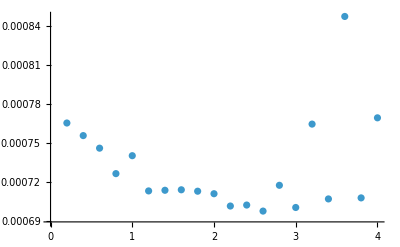

```mathematica
ListPlot[tabs]
```

```mathematica
tbls2=Table[If[tbls[[i,4]]<mn*1.04,{tbls[[i,1]],tbls[[i,2]],tbls[[i,3]]},Nothing],{i,1,Length[tbls]}]
```

{{0,2.2,0.4},{0,2.2,0.6},{0.2,2.,0.4},{0.4,1.8,0.2},{0.6,1.8,0.4},{0.8,1.6,0.2},{0.8,1.6,0.4},{1.2,1.4,0.2},{1.2,1.4,0.4},{1.4,1.2,0.4},{1.6,1.2,0.2},{2.2,0.8,0.2},{2.4,0.8,0},{2.6,0.6,0.2},{3.,0.4,0.2}}

```mathematica
ListPointPlot3D[tbls2]
```

-Graphics3D-

```mathematica
ListDensityPlot3D[tbls2,ColorFunction->"TemperatureMap",PlotLegends->Automatic,OpacityFunction->1]
```

-Graphics3D-

```mathematica
ListDensityPlot3D[tbls,ColorFunction->"TemperatureMap",PlotLegends->Automatic,OpacityFunction->0.1]
```

-Graphics3D-

```mathematica
PositionSmallest[tbls[[All,4]]]
```

{1633}

```mathematica
tbls[[1633]]
```

{2.4,4.,0,0.000221577}

```mathematica
ListPlot[tbls[All,4]]
```

```mathematica
model/.Ai->0.002/.lp->400/.α->0.5/.γ->3/.γo->3
```

9.52381×10^-6 ⅇ^(-3 x/80) (-600 ⅇ^(x/80)-2340 ⅇ^(17 x/800)+3150 ⅇ^(x/40))

```mathematica
Plot[model/.Ai->0.002/.lp->400/.α->0.5/.γ->3/.γo->3,{x,0,800}]
```

-Graphics-

```mathematica
model/.Ai->1/.lp->400/.α->0./.γ->2.6/.γo->3.8
```

-0.000178587 ⅇ^(-0.0141667 x) (-51247.5+2243.16 ⅇ^(-0.0118333 x)+49004.3 ⅇ^(-0.00358333 x))

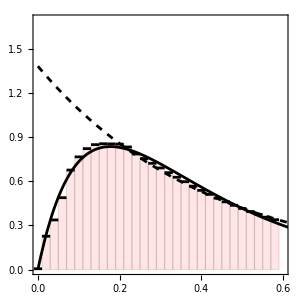

```mathematica
gr4e=Show[DiscretePlot[Interpolation[lstAoo][x],{x,0.00001,0.6,0.02},PlotRange->{{0,0.6},{0,1.7}},ExtentSize->0.02,FillingStyle->Directive[EdgeForm[Black],Opacity[.1],Red],PlotStyle->Black,AspectRatio->1,Frame->True,FrameStyle->Directive[FSize,FontFamily->"Times",Black],FrameTicksStyle->Directive[FTicksSize],PlotLegends->Automatic],
(*Graphics[Text[Style["G1 (γ="<>ToString[γExp["Value"]]<>", γ_b="<>ToString[Round[γBExp["Value"]]]<>", γ_CTCF=1)",FontSize->16,FontFamily->"CMU Serif"],{0.06,2.35},{-1,0}]]*)
Plot[{modelAoo/.Ai->31/.lp->0.6/.α->0.2/.γ->2.6/.γo->0.6/.x->xi},{xi,0,0.8},PlotStyle->{Directive[Black]}],Plot[{Am*Exp[-k*x]/.fit2},{x,0,0.8},PlotStyle->{Directive[Black,Dashed]},PlotRange->All]]
```

```mathematica
GraphicsRow[{gr4d,gr4e}]
```

-Graphics-

## Фит для CTCF - CTCF Loops (Fig 4e)

```mathematica
Aoos
```

```mathematica
lstAoo=Import["C:\\петли\\ЭКСПЕРИМЕНТЫ\\CTCF LOOPS\\CTCF_loops_4.txt","Table"];
```

```mathematica
lstAoo2=Import["C:\\петли\\ЭКСПЕРИМЕНТЫ\\chia-pet\\5k562.txt","Table"];
```

```mathematica
modelAoo=Ai*Aoos/.x->x/lp;
```

```mathematica
fit2=FindFit[lstAoo[[20;;Length[lstAoo]]],Am*Exp[-k*x],{{Am,0.001},{k,0.001}},x]
```

{Am→1.65929,k→2.63313}

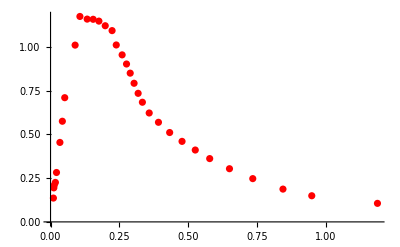

```mathematica
Show[ListPlot[lstAoo,PlotStyle->Red],Plot[Am Exp[-k x]/.{Am->2.5300264137567883,k->0.9291143166956148},{x,21.63363493,901.65956}]]
```

```mathematica
w=0.03;
```

```mathematica
FSize=20;
FTicksSize=15;
```

```mathematica
tblsN={};
intAoo1=Interpolation[lstAoo];
intAoo2=Interpolation[lstAoo2];
```

```mathematica
tblsAoof={};
For[γi=2.6,γi<=2.6,γi=γi+0.2,{
For[γoi=0.4,γoi<=1.6,γoi=γoi+0.2,{
For[αi=0.2,αi<=1,αi=αi+0.2,{
ft1= FindFit[lstAoo,modelAoo/.lp->0.6/.α->αi/.γ->γi/.γo->γoi,{{α,1.5},{γ,2},{γo,2},{Ai,3}},{x}];
ft2 = FindFit[lstAoo2,modelAoo/.lp->0.6/.α->αi/.γ->γi/.γo->γoi,{{α,1.5},{γ,2},{γo,2},{Ai,3}},{x}];
f1=(intAoo1[x]-(modelAoo/.lp->0.6/.α->αi/.γ->γi/.γo->γoi/.ft1))^2;
f2=(intAoo2[x]-(modelAoo/.lp->0.6/.α->αi/.γ->γi/.γo->γoi/.ft2))^2;
nrmseAoo1=NIntegrate[f1,{x,0.01,0.6}];
nrmseAoo2=NIntegrate[f2,{x,0.01,0.6}];
AppendTo[tblsAoof,{γi,γoi,αi, nrmseAoo1,nrmseAoo2}];
}];
}];
Print[γi]
}]
```

2.6

```mathematica
tblsFin=Table[{tblsAoof[[i,2]],tblsAoof[[i,3]],tblsAoof[[i,4]]+tblsAoof[[i,5]]},{i,1,Length[tblsAoof]}]
```

{{0.4,0.2,0.0118721},{0.4,0.4,0.00816566},{0.4,0.6,0.00594929},{0.4,0.8,0.00503927},{0.4,1.,0.00519333},{0.6,0.2,0.00779796},{0.6,0.4,0.00588755},{0.6,0.6,0.00495531},{0.6,0.8,0.0049788},{0.6,1.,0.00581926},{0.8,0.2,0.00541289},{0.8,0.4,0.00479989},{0.8,0.6,0.00484072},{0.8,0.8,0.00558752},{0.8,1.,0.00696517},{1.,0.2,0.00463914},{1.,0.4,0.00484345},{1.,0.6,0.00555883},{1.,0.8,0.00682834},{1.,1.,0.00860147},{1.2,0.2,0.00537469},{1.2,0.4,0.00594919},{1.2,0.6,0.00705895},{1.2,0.8,0.00866268},{1.2,1.,0.0106982},{1.4,0.2,0.00750206},{1.4,0.4,0.00804173},{1.4,0.6,0.00928797},{1.4,0.8,0.0110512},{1.4,1.,0.0132255},{1.6,0.2,0.0108953},{1.6,0.4,0.0110423},{1.6,0.6,0.0121917},{1.6,0.8,0.0139547},{1.6,1.,0.0161538}}

```mathematica
tblsFin2=Table[{tblsAoof[[i,2]],tblsAoof[[i,3]],tblsAoof[[i,5]]},{i,1,Length[tblsAoof]}]
```

{{0.4,0.2,0.000913949},{0.4,0.4,0.000499192},{0.4,0.6,0.000725819},{0.4,0.8,0.00148038},{0.4,1.,0.00264252},{0.6,0.2,0.00047579},{0.6,0.4,0.000676814},{0.6,0.6,0.00133916},{0.6,0.8,0.00240018},{0.6,1.,0.00377612},{0.8,0.2,0.000801016},{0.8,0.4,0.00138568},{0.8,0.6,0.00233827},{0.8,0.8,0.00360763},{0.8,1.,0.00512818},{1.,0.2,0.00184047},{1.,0.4,0.00258923},{1.,0.6,0.00369504},{1.,0.8,0.00508091},{1.,1.,0.00668169},{1.2,0.2,0.00353163},{1.2,0.4,0.00424577},{1.2,0.6,0.00537948},{1.2,0.8,0.00679768},{1.2,1.,0.00841963},{1.4,0.2,0.00580458},{1.4,0.4,0.00631085},{1.4,0.6,0.00736077},{1.4,0.8,0.00873554},{1.4,1.,0.0103253},{1.6,0.2,0.00858661},{1.6,0.4,0.00873913},{1.6,0.6,0.00960809},{1.6,0.8,0.0108724},{1.6,1.,0.0123823}}

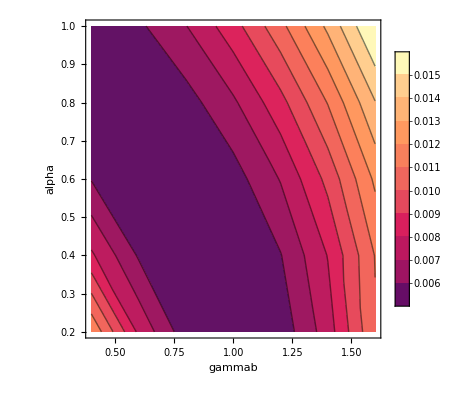

```mathematica
ListContourPlot[tblsFin,Contours->10,FrameLabel->{"gammab","alpha"},PlotLegends->Automatic]
```

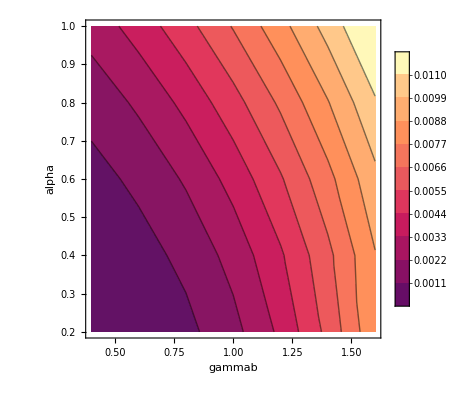

```mathematica
ListContourPlot[tblsFin2,Contours->10,FrameLabel->{"gammab","alpha"},PlotLegends->Automatic]
```

```mathematica
tblsFin[[PositionSmallest[tblsFin[[All,3]]]]]
```

{{1.,0.2,0.00463914}}

```mathematica
Sqrt[0.0016450552218425694]
```

0.0405593

```mathematica
FindFit[lstAoo,modelAoo/.lp->0.6/.α->0.4/.γ->2.4/.γo->1.4,{{α,1.5},{γ,2},{γo,2},{Ai,3}},{x}]
```

{α→0.,γ→0.,γo→0.,Ai→11.7834}

```mathematica
Sqrt[0.000456088]
```

0.0213562

```mathematica
Sqrt[0.000475790086408104]
```

0.0218126

```mathematica
Sqrt[]
```

```mathematica
tabs
```

{{0.,∞,0.000469201},{0.2,0.000299727,0.000465652},{0.4,0.000284843,0.000470838},{0.6,0.000271702,0.000474297},{0.8,0.000260238,0.000466154},{1.,0.000250388,0.000489817},{1.2,0.000242092,0.000470977},{1.4,0.000235286,0.00047828},{1.6,0.000229912,0.00048403},{1.8,0.00022591,0.000486937},{2.,0.000223224,0.000487692},{2.2,0.000221798,0.000479638},{2.4,0.000221577,0.000480616},{2.6,0.000221748,0.00047579},{2.8,0.00022176,0.000495642},{3.,0.000221772,0.000478539},{3.2,0.000222031,0.000542513},{3.4,0.000221881,0.000485022},{3.6,0.000222399,0.000625046},{3.8,0.000222089,0.000485613},{4.,0.000222501,0.000546869}}

```mathematica
ListPlot[tabs]
```

-Graphics-

```mathematica
tbls2=Table[If[tbls[[i,4]]<mn*1.04,{tbls[[i,1]],tbls[[i,2]],tbls[[i,3]]},Nothing],{i,1,Length[tbls]}]
```

{{0,2.2,0.4},{0,2.2,0.6},{0.2,2.,0.4},{0.4,1.8,0.2},{0.6,1.8,0.4},{0.8,1.6,0.2},{0.8,1.6,0.4},{1.2,1.4,0.2},{1.2,1.4,0.4},{1.4,1.2,0.4},{1.6,1.2,0.2},{2.2,0.8,0.2},{2.4,0.8,0},{2.6,0.6,0.2},{3.,0.4,0.2}}

```mathematica
ListPointPlot3D[tbls2]
```

-Graphics3D-

```mathematica
ListDensityPlot3D[tbls2,ColorFunction->"TemperatureMap",PlotLegends->Automatic,OpacityFunction->1]
```

-Graphics3D-

```mathematica
ListDensityPlot3D[tbls,ColorFunction->"TemperatureMap",PlotLegends->Automatic,OpacityFunction->0.1]
```

-Graphics3D-

```mathematica
PositionSmallest[tbls[[All,4]]]
```

{1633}

```mathematica
tbls[[1633]]
```

{2.4,4.,0,0.000221577}

```mathematica
ListPlot[tbls[All,4]]
```

```mathematica
model/.Ai->0.002/.lp->400/.α->0.5/.γ->3/.γo->3
```

9.52381×10^-6 ⅇ^(-3 x/80) (-600 ⅇ^(x/80)-2340 ⅇ^(17 x/800)+3150 ⅇ^(x/40))

```mathematica
Plot[model/.Ai->0.002/.lp->400/.α->0.5/.γ->3/.γo->3,{x,0,800}]
```

-Graphics-

```mathematica
model/.Ai->1/.lp->400/.α->0./.γ->2.6/.γo->3.8
```

-0.000178587 ⅇ^(-0.0141667 x) (-51247.5+2243.16 ⅇ^(-0.0118333 x)+49004.3 ⅇ^(-0.00358333 x))

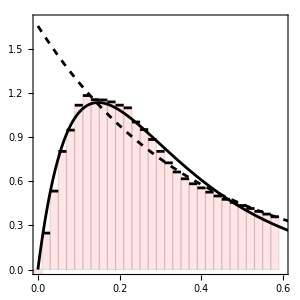

```mathematica
gr4e=Show[DiscretePlot[Interpolation[lstAoo][x],{x,0.00001,0.6,0.02},PlotRange->{{0,0.6},{0,1.7}},ExtentSize->0.02,FillingStyle->Directive[EdgeForm[Black],Opacity[.1],Red],PlotStyle->Black,AspectRatio->1,Frame->True,FrameStyle->Directive[FSize,FontFamily->"Times",Black],FrameTicksStyle->Directive[FTicksSize],PlotLegends->Automatic],
(*Graphics[Text[Style["G1 (γ="<>ToString[γExp["Value"]]<>", γ_b="<>ToString[Round[γBExp["Value"]]]<>", γ_CTCF=1)",FontSize->16,FontFamily->"CMU Serif"],{0.06,2.35},{-1,0}]]*)
Plot[{modelAoo/.Ai->12/.lp->0.6/.α->0.4/.γ->2.4/.γo->1.4/.x->xi},{xi,0,0.8},PlotStyle->{Directive[Black]}],Plot[{Am*Exp[-k*x]/.fit2},{x,0,0.8},PlotStyle->{Directive[Black,Dashed]},PlotRange->All]]
```

```mathematica
GraphicsRow[{gr4d,gr4e}]
```

-Graphics-